## Estimate normal bacteria’s basal growth rate

```mathematica
controlTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[4,2;;]][[1;;280]];
controlData=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[5;;93,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,controlData];
means=Map[Mean[#]&,controlData];
bacteriaControl=Apply[Around,Transpose[{means,stds}],{1}];
bacteriaControl=Transpose[{controlTime,bacteriaControl}];
controlfitdata=Apply[Join,Table[Map[{controlTime[[i]],#}&,controlData[[i]]],{i,1,Length[controlTime]}]];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[bacteriaControl,#[[1]]==3.5&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
para=NonlinearModelFit[Select[controlfitdata,#[[1]]≥3.5&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]
basalr=para[[1,2]][[2,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.906235 ⅇ^(0.880031 t))/(31.3865+1. ⅇ^(0.880031 t))]

0.880031

```mathematica
Length[controlData[[1]]]
```

89

```mathematica
para["ParameterConfidenceIntervals"]
```

{{0.905727,0.906744},{0.874877,0.885185}}

```mathematica
resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
luz19Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[16;;63,2;;]]];
stds=Map[StandardDeviation[#]&,luz19Growth];
means=Map[Mean[#]&,luz19Growth];
luz19GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
luz19GrowthData=Transpose[{resistantTime,luz19GrowthData}];
luz19Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,luz19Growth[[i]]],{i,1,Length[resistantTime]}]];

resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
pyo2Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[76;;107,2;;]]];
stds=Map[StandardDeviation[#]&,pyo2Growth];
means=Map[Mean[#]&,pyo2Growth];
pyo2GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
pyo2GrowthData=Transpose[{resistantTime,pyo2GrowthData}];
pyo2Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,pyo2Growth[[i]]],{i,1,Length[resistantTime]}]];

resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
e215Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[123;;170,2;;]]];
stds=Map[StandardDeviation[#]&,e215Growth];
means=Map[Mean[#]&,e215Growth];
e215GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
e215GrowthData=Transpose[{resistantTime,e215GrowthData}];
e215Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,e215Growth[[i]]],{i,1,Length[resistantTime]}]];

resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
luz19pyo2Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[230;;261,2;;]]];
stds=Map[StandardDeviation[#]&,luz19pyo2Growth];
means=Map[Mean[#]&,luz19pyo2Growth];
luz19pyo2GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
luz19pyo2GrowthData=Transpose[{resistantTime,luz19pyo2GrowthData}];
luz19pyo2Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,luz19pyo2Growth[[i]]],{i,1,Length[resistantTime]}]];

resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
luz19e215Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[280;;309,2;;]]];
stds=Map[StandardDeviation[#]&,luz19e215Growth];
means=Map[Mean[#]&,luz19e215Growth];
luz19e215GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
luz19e215GrowthData=Transpose[{resistantTime,luz19e215GrowthData}];
luz19e215Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,luz19e215Growth[[i]]],{i,1,Length[resistantTime]}]];

resistantTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[4,2;;]];
pyo2e215Growth=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[3]][[183;;217,2;;]]];
stds=Map[StandardDeviation[#]&,pyo2e215Growth];
means=Map[Mean[#]&,pyo2e215Growth];
pyo2e215GrowthData=Apply[Around,Transpose[{means,stds}],{1}];
pyo2e215GrowthData=Transpose[{resistantTime,pyo2e215GrowthData}];
pyo2e215Growthfitdata=Apply[Join,Table[Map[{resistantTime[[i]],#}&,pyo2e215Growth[[i]]],{i,1,Length[resistantTime]}]];
```

```mathematica
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[luz19GrowthData,#[[1]]==3.5&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
luz19para=NonlinearModelFit[Select[luz19Growthfitdata,#[[1]]≥3.5&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]

germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4.5]==Select[pyo2GrowthData,#[[1]]==4.5&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
pyo2para=NonlinearModelFit[Select[pyo2Growthfitdata,#[[1]]≥4.5&],{germGrowth[k,r,t]},{{k,0.998},{r,0.87}},t]

germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.8]==Select[e215GrowthData,#[[1]]==3.8&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
e215para=NonlinearModelFit[Select[e215Growthfitdata,#[[1]]≥3.8&],{germGrowth[k,r,t]},{{k,0.88},{r,0.87}},t]

germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4]==Select[luz19pyo2GrowthData,#[[1]]==4&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
luz19pyo2para=NonlinearModelFit[Select[luz19pyo2Growthfitdata,14>=#[[1]]≥4&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]

germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==Select[luz19e215GrowthData,#[[1]]==3&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
luz19e215para=NonlinearModelFit[Select[luz19e215Growthfitdata,#[[1]]≥3&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]

germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4]==Select[pyo2e215GrowthData,#[[1]]==4&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
pyo2e215para=NonlinearModelFit[Select[pyo2e215Growthfitdata,16>=#[[1]]≥4&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.851347 ⅇ^(0.716094 t))/(19.6397+1. ⅇ^(0.716094 t))]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.934502 ⅇ^(0.730773 t))/(36.223+1. ⅇ^(0.730773 t))]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.837036 ⅇ^(0.752185 t))/(29.4735+1. ⅇ^(0.752185 t))]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.853352 ⅇ^(0.606838 t))/(16.7957+1. ⅇ^(0.606838 t))]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.678533 ⅇ^(0.618321 t))/(13.099+1. ⅇ^(0.618321 t))]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.924543 ⅇ^(0.74521 t))/(30.0751+1. ⅇ^(0.74521 t))]

```mathematica
1/Select[luz19pyo2GrowthData,#[[1]]≥tt&][[All,2,2]]
```

{23.1802,22.4643,21.459,20.0169,18.9475,18.1758,17.2188,16.677,16.0275,15.4322,14.8679,14.5111,13.8193,12.8282,11.1794,9.92907,8.55725,7.64365,7.0719,6.62193,6.53507,6.39654,6.32442,6.2261,6.16465,6.0744,5.98415,5.92947,5.85524,5.85863,5.83686,5.8215,5.88104,5.99365,6.07744,6.15118,6.20522,6.27862,6.30027,6.35423,6.37377,6.47005,6.49374,6.53927,6.61743,6.65106,6.68299,6.77944,6.86534,6.90856,6.98694,7.1098,7.17332,7.2762,7.35883,7.53525,7.94636,8.60375,9.08026,9.3275,9.75166,9.97709,10.0049,10.2165,10.3716,10.4757,10.6792,10.5996,10.6937,10.7781,10.8151,10.9834,10.8909,10.9442,10.8044,10.7244,10.9423,10.8286,10.9402,10.9155,10.9343,10.8246,10.7159,10.7683,10.8538,10.8964,10.9015,10.8618,10.8956,10.9267,10.7899,10.8367,10.7495,10.9327,10.8799,10.797,10.817,10.7771,10.8336,10.8843,10.8462,10.7643,10.8227,10.8551,10.7819,10.6954,10.7929,10.7216,10.7209,10.6996,10.7278,10.6715,10.6476,10.6025,10.8072,10.6626,10.6339,10.6365,10.6008,10.5158,10.4943,10.433,10.3784,10.4009,10.3861,10.3183,10.4229,10.5206,10.5006,10.6152,10.7266,10.7001,10.8108,10.9425,10.9573,11.2968,11.2264,11.4747,11.7158,11.802,11.8337,12.0932,11.9731,12.4478,12.6561,13.0949,13.1322,13.5743,13.751,13.7516,14.2768}

```mathematica
Mean[pyo2Boot[[2;;,1]]]
```

0.0114099

```mathematica
tt=4
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[tt]==Select[luz19pyo2GrowthData,#[[1]]==tt&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
luz19pyo2para=NonlinearModelFit[Select[luz19pyo2Growthfitdata,14>=#[[1]]≥tt&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]
```

4

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.853352 ⅇ^(0.606838 t))/(16.7957+1. ⅇ^(0.606838 t))]

```mathematica
tt=3
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[tt]==Select[luz19e215GrowthData,#[[1]]==tt&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
luz19e215para=NonlinearModelFit[Select[luz19e215Growthfitdata,#[[1]]≥tt&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]
```

3

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.678533 ⅇ^(0.618321 t))/(13.099+1. ⅇ^(0.618321 t))]

```mathematica
luz19r
luz19para["ParameterConfidenceIntervals"]
```

0.716094

{{0.850081,0.852613},{0.709426,0.722761}}

```mathematica
pyo2r
pyo2para["ParameterConfidenceIntervals"]
```

0.730773

{{0.932057,0.936946},{0.717815,0.743731}}

```mathematica
e215r
e215para["ParameterConfidenceIntervals"]
```

0.752185

{{0.835583,0.83849},{0.744134,0.760236}}

```mathematica
luz19pyo2r
luz19pyo2para["ParameterConfidenceIntervals"]
```

0.606838

{{0.845672,0.861033},{0.582699,0.630977}}

```mathematica
luz19pyo2r*0.9
luz19pyo2para["ParameterConfidenceIntervals"]*0.9
```

0.546154

{{0.761105,0.77493},{0.524429,0.567879}}

```mathematica
luz19e215r
luz19e215para["ParameterConfidenceIntervals"]
```

0.618321

{{0.672173,0.684893},{0.58963,0.647013}}

```mathematica
luz19e215r*0.9
luz19e215para["ParameterConfidenceIntervals"]*0.9
```

0.556489

{{0.604955,0.616403},{0.530667,0.582312}}

```mathematica
pyo2e215r
pyo2e215para["ParameterConfidenceIntervals"]
```

0.74521

{{0.921901,0.927185},{0.732781,0.757639}}

```mathematica
matlabColors={RGBColor[0,0.4470,0.7410],RGBColor[0.8500,0.3250,0.0980],RGBColor[0.9290,0.6940,0.1250],RGBColor[0.4940,0.1840,0.5560],RGBColor[0.4660,0.6740,0.1880],RGBColor[0.6350,0.0780,0.1840]};
marker=Graphics[{AbsoluteThickness[4],Line[{{0,0},{1,0}}]},ImageSize->Tiny];
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\PAO1_growth.png",Show[ListLinePlot[bacteriaControl,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,15,3}],{0,0.6,1.2}}],
Plot[Normal[para],
{t,3.5,27.9},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,3.5,27.9},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]
```

C:\Users\zhiyu\Desktop\phage figures\growth_fit\PAO1_growth.png

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\LUZ19_R_growth.png",Show[ListLinePlot[luz19GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[luz19para],
{t,3.5,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[luz19para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,3.5,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\PYO2_R_growth.png",Show[ListLinePlot[pyo2GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
FrameLabel->{"Time (h)","OD_600"},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[pyo2para],
{t,4.5,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[pyo2para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,4.5,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,Thick},{Black,Normal}},{{Black,Normal,Thick},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\E215_growth.png",Show[ListLinePlot[e215GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
FrameLabel->{"Time (h)","OD_600"},
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[e215para],
{t,3.8,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[e215para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,3.8,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\LUZ19_PYO2_growth.png",Show[ListLinePlot[luz19pyo2GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[luz19pyo2para],
{t,4,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,Thick},{Black,Normal}},{{Black,Normal,Thick},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[luz19pyo2para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,4,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\LUZ19_E215_growth.png",Show[ListLinePlot[luz19e215GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
FrameLabel->{"Time (h)","OD_600"},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[luz19e215para],
{t,3,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[luz19e215para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,3,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\growth_fit\\PYO2_E215_growth.png",Show[ListLinePlot[pyo2e215GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[pyo2e215para],
{t,4,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}],
Plot[Evaluate[pyo2e215para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,4,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->Automatic,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial"}]]]
```

C:\Users\zhiyu\Desktop\phage figures\growth_fit\LUZ19_R_growth.png

C:\Users\zhiyu\Desktop\phage figures\growth_fit\PYO2_R_growth.png

C:\Users\zhiyu\Desktop\phage figures\growth_fit\E215_growth.png

C:\Users\zhiyu\Desktop\phage figures\growth_fit\LUZ19_PYO2_growth.png

C:\Users\zhiyu\Desktop\phage figures\growth_fit\LUZ19_E215_growth.png

C:\Users\zhiyu\Desktop\phage figures\growth_fit\PYO2_E215_growth.png

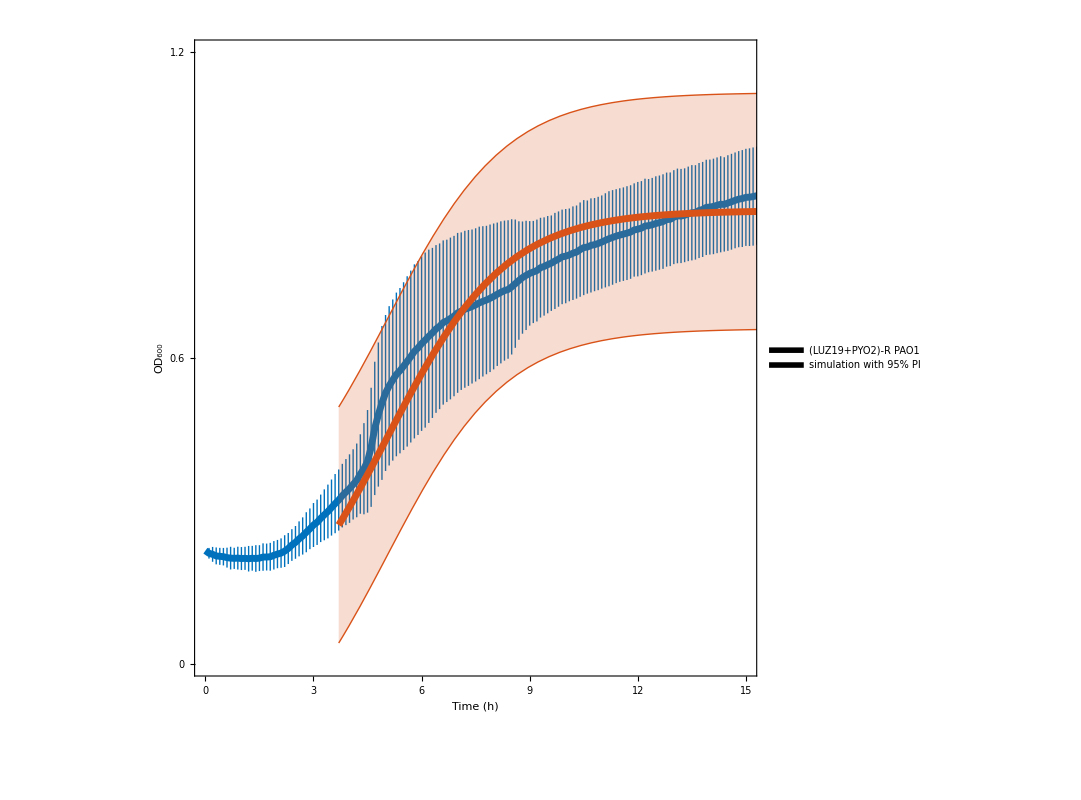

```mathematica
Legended[Show[ListLinePlot[luz19pyo2GrowthData,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,15},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
FrameLabel->{"Time (h)","OD_600"},
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Bold,AbsoluteThickness[3]},None},{{Black,Bold,AbsoluteThickness[3]},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Plot[Normal[luz19pyo2para],
{t,3.7,18},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->All,
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->Automatic,
FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial"}],
Plot[Evaluate[luz19pyo2para["SinglePredictionBands",ConfidenceLevel->0.95]],
{t,3.7,18},
PlotRange->All,
Filling->{1->{2}},
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[1]},{matlabColors[[2]],AbsoluteThickness[1]}},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->Automatic,
FrameStyle->{{{Black,Bold,AbsoluteThickness[3]},None},{{Black,Bold,AbsoluteThickness[3]},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial"}]],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]]},
{"(LUZ19+PYO2)-R PAO1", "simulation with 95% PI"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->35}],
{{0.3,0.01},{0,0}}]]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\single_resistant_data.png",Legended[ListLinePlot[{luz19GrowthData,pyo2GrowthData,e215GrowthData},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[4]},{matlabColors[[2]],AbsoluteThickness[4]},{matlabColors[[3]],AbsoluteThickness[4]}},
PlotRange->{{0,18},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->None,
FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->35},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]]},
{"LUZ19-R PAO1 data", "PYO2-R PAO1 data","E215-R PAO1 data"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->30}],
{{0.35,0.1},{0,0}}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\single_resistant_data.png

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\double_resistant_data.png",Legended[ListLinePlot[{luz19pyo2GrowthData,luz19e215GrowthData,pyo2e215GrowthData},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[4]},{matlabColors[[2]],AbsoluteThickness[4]},{matlabColors[[3]],AbsoluteThickness[4]}},
PlotRange->{{0,18},{0,1.2}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->None,
FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->35},
FrameTicks->{Table[i,{i,0,18,3}],{0,0.6,1.2}}],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]]},
{"LUZ19&PYO2-R PAO1 data", "LUZ19&E215-R PAO1 data","PYO2&E215-R PAO1 data"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->30}],
{{0.35,0.1},{0,0}}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\double_resistant_data.png

```mathematica
basalr=para["BestFitParameters"][[2,2]]
luz19r=luz19para["BestFitParameters"][[2,2]]
pyo2r=pyo2para["BestFitParameters"][[2,2]]
e215r=e215para["BestFitParameters"][[2,2]]
luz19pyo2r=luz19pyo2para["BestFitParameters"][[2,2]]
luz19e215r=luz19e215para["BestFitParameters"][[2,2]]
pyo2e215r=pyo2e215para["BestFitParameters"][[2,2]]
```

0.880031

0.716094

0.730773

0.752185

0.606838

0.618321

0.74521

```mathematica
{
Around[luz19para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]]}
```

{0.8140.011,0.8300.021,0.8550.013,0.690.04,0.700.05,0.8470.020}

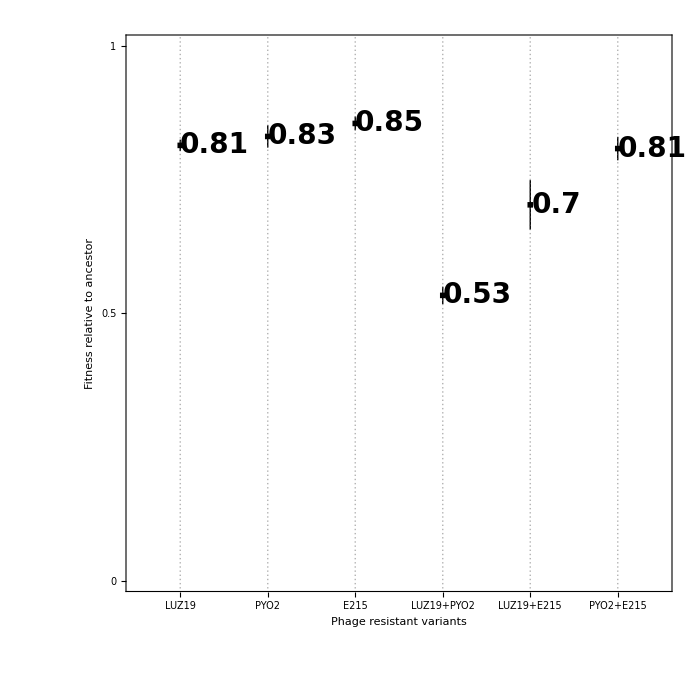

```mathematica
ListPlot[{
Around[luz19para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]]},
PlotTheme->"Detailed",
LabelingFunction->(Placed[DecimalForm[#1[[2]],2],Right]&),
AspectRatio->1,
ImageSize->700,
BaseStyle->{Bold,28},
FrameStyle->{{{Black,Bold,AbsoluteThickness[3]},{Black,Bold,AbsoluteThickness[3]}},{{Black,Bold,AbsoluteThickness[3]},{Black,Bold,AbsoluteThickness[3]}}},
PlotRange->{{0.5,6.5},{0,1}},
PlotMarkers->{Graphics[{Black,Rectangle[]}],0.015},
IntervalMarkersStyle->{Thick,Black},
FrameLabel->{"Phage resistant variants","Fitness relative to ancestor"},
FrameTicks->{{{0,0.5,1},None},{Transpose[{Table[i,{i,1,6,1}],Rotate[#,Pi/6]&/@{"LUZ19","PYO2","E215","LUZ19+PYO2","LUZ19+E215","PYO2+E215"}}],None}}
]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\fitness.png",Legended[BarChart[{Around[para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19pyo2para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[luz19e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]],
Around[pyo2e215para["ParameterConfidenceIntervals",ConfidenceLevel->0.95][[2]]]/para["BestFitParameters"][[2,2]]},
ChartStyle->{matlabColors[[1]],matlabColors[[2]],matlabColors[[2]],matlabColors[[2]],matlabColors[[3]],matlabColors[[3]],matlabColors[[3]]},
PlotTheme->"Detailed",
AspectRatio->1,
ImageSize->800,
BaseStyle->{Bold,28},
GridLines->None,
FrameStyle->{{{Black,Bold,AbsoluteThickness[3]},None},{{Black,Bold,AbsoluteThickness[3]},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial"},
Frame->{True,True,False,False},
PlotRange->{{0.5,7.5},{0,1}},
FrameTicks->{Transpose[{Table[i,{i,1,7,1}],Rotate[#,Pi/6]&/@{"None","LUZ19","PYO2","E215","LUZ19\n+PYO2","LUZ19\n+E215","PYO2\n+E215"}}],{0,0.5,1}},
ImageSize->800,
IntervalMarkersStyle->Thick,
FrameLabel->{"Phage resistant variants","Relative fitness"}
],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]]},
{"ancestral","single resistant", "double resistant"},
LegendFunction->Framed,
LegendMarkerSize->{20,20},
Spacings->0.15,
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->28}],{0.8, 0.92}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\fitness.png

```mathematica
luz19Moi10=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[97;;112,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19Moi10];
means=Map[Mean[#]&,luz19Moi10];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19Moi10fitdata=Apply[Join,Table[Map[{controlTime[[i]],10,#}&,luz19Moi10[[i]]],{i,1,Length[controlTime]}]];
luz19Moi10=Transpose[{controlTime,meanWithSD}];
luz19Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[115;;147,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19Moi1];
means=Map[Mean[#]&,luz19Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19Moi1[[i]]],{i,1,Length[controlTime]}]];
luz19Moi1=Transpose[{controlTime,meanWithSD}];
luz19Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[150;;182,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19Moi01];
means=Map[Mean[#]&,luz19Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.1,#}&,luz19Moi01[[i]]],{i,1,Length[controlTime]}]];
luz19Moi01=Transpose[{controlTime,meanWithSD}];
luz19Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[185;;215,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19Moi001];
means=Map[Mean[#]&,luz19Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.01,#}&,luz19Moi001[[i]]],{i,1,Length[controlTime]}]];
luz19Moi001=Transpose[{controlTime,meanWithSD}];

pyo2Moi10=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[219;;228,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2Moi10];
means=Map[Mean[#]&,pyo2Moi10];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2Moi10fitdata=Apply[Join,Table[Map[{controlTime[[i]],10,#}&,pyo2Moi10[[i]]],{i,1,Length[controlTime]}]];
pyo2Moi10=Transpose[{controlTime,meanWithSD}];
pyo2Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[231;;262,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2Moi1];
means=Map[Mean[#]&,pyo2Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,pyo2Moi1[[i]]],{i,1,Length[controlTime]}]];
pyo2Moi1=Transpose[{controlTime,meanWithSD}];
pyo2Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[265;;295,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2Moi01];
means=Map[Mean[#]&,pyo2Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.1,#}&,pyo2Moi01[[i]]],{i,1,Length[controlTime]}]];
pyo2Moi01=Transpose[{controlTime,meanWithSD}];
pyo2Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[298;;321,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2Moi001];
means=Map[Mean[#]&,pyo2Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.01,#}&,pyo2Moi001[[i]]],{i,1,Length[controlTime]}]];
pyo2Moi001=Transpose[{controlTime,meanWithSD}];

e215Moi10=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[325;;351,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,e215Moi10];
means=Map[Mean[#]&,e215Moi10];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
e215Moi10fitdata=Apply[Join,Table[Map[{controlTime[[i]],10,#}&,e215Moi10[[i]]],{i,1,Length[controlTime]}]];
e215Moi10=Transpose[{controlTime,meanWithSD}];
e215Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[354;;383,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,e215Moi1];
means=Map[Mean[#]&,e215Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
e215Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,e215Moi1[[i]]],{i,1,Length[controlTime]}]];
e215Moi1=Transpose[{controlTime,meanWithSD}];
e215Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[386;;418,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,e215Moi01];
means=Map[Mean[#]&,e215Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
e215Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.1,#}&,e215Moi01[[i]]],{i,1,Length[controlTime]}]];
e215Moi01=Transpose[{controlTime,meanWithSD}];
e215Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[421;;440,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,e215Moi001];
means=Map[Mean[#]&,e215Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
e215Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],0.01,#}&,e215Moi001[[i]]],{i,1,Length[controlTime]}]];
e215Moi001=Transpose[{controlTime,meanWithSD}];

luz19pyo2Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[532;;564,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19pyo2Moi1];
means=Map[Mean[#]&,luz19pyo2Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19pyo2Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19pyo2Moi1[[i]]],{i,1,Length[controlTime]}]];
luz19pyo2Moi1=Transpose[{controlTime,meanWithSD}];
luz19pyo2Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[567;;599,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19pyo2Moi01];
means=Map[Mean[#]&,luz19pyo2Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19pyo2Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19pyo2Moi01[[i]]],{i,1,Length[controlTime]}]];
luz19pyo2Moi01=Transpose[{controlTime,meanWithSD}];
luz19pyo2Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[602;;634,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19pyo2Moi001];
means=Map[Mean[#]&,luz19pyo2Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19pyo2Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19pyo2Moi001[[i]]],{i,1,Length[controlTime]}]];
luz19pyo2Moi001=Transpose[{controlTime,meanWithSD}];

luz19e215Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[638;;687,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19e215Moi1];
means=Map[Mean[#]&,luz19e215Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19e215Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19e215Moi1[[i]]],{i,1,Length[controlTime]}]];
luz19e215Moi1=Transpose[{controlTime,meanWithSD}];
luz19e215Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[690;;719,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19e215Moi01];
means=Map[Mean[#]&,luz19e215Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19e215Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19e215Moi01[[i]]],{i,1,Length[controlTime]}]];
luz19e215Moi01=Transpose[{controlTime,meanWithSD}];
luz19e215Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[722;;754,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,luz19e215Moi001];
means=Map[Mean[#]&,luz19e215Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
luz19e215Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,luz19e215Moi001[[i]]],{i,1,Length[controlTime]}]];
luz19e215Moi001=Transpose[{controlTime,meanWithSD}];

pyo2e215Moi1=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[444;;475,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2e215Moi1];
means=Map[Mean[#]&,pyo2e215Moi1];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2e215Moi1fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,pyo2e215Moi1[[i]]],{i,1,Length[controlTime]}]];
pyo2e215Moi1=Transpose[{controlTime,meanWithSD}];
pyo2e215Moi01=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[478;;510,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2e215Moi01];
means=Map[Mean[#]&,pyo2e215Moi01];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2e215Moi01fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,pyo2e215Moi01[[i]]],{i,1,Length[controlTime]}]];
pyo2e215Moi01=Transpose[{controlTime,meanWithSD}];
pyo2e215Moi001=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[513;;528,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,pyo2e215Moi001];
means=Map[Mean[#]&,pyo2e215Moi001];
meanWithSD=Apply[Around,Transpose[{means,stds}],{1}];
pyo2e215Moi001fitdata=Apply[Join,Table[Map[{controlTime[[i]],1,#}&,pyo2e215Moi001[[i]]],{i,1,Length[controlTime]}]];
pyo2e215Moi001=Transpose[{controlTime,meanWithSD}];
```

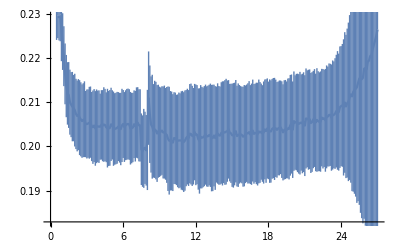

```mathematica
ListLinePlot[Select[luz19e215Moi1,0.5<=#[[1]]<=27&]]
```

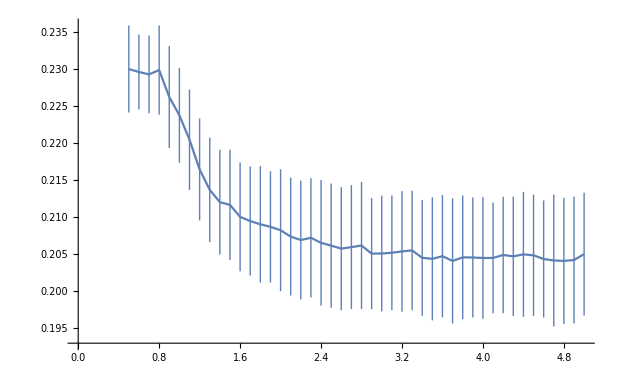

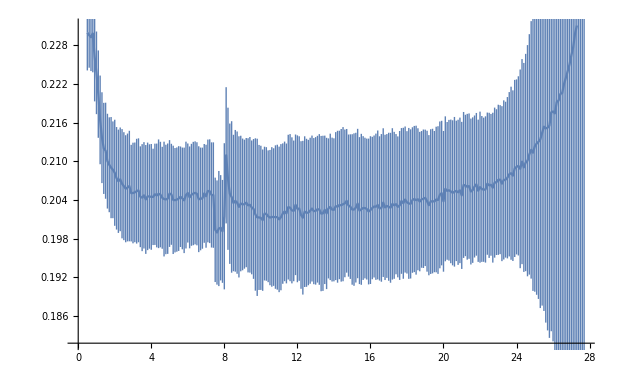

```mathematica
ListLinePlot[Select[luz19e215Moi1,0.5<=#[[1]]<=5&]]
ListLinePlot[Select[luz19e215Moi1,0.5<=#[[1]]<=27.7&]]
luz19e215Moi1Lag=0.5;
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\luz19_e215_fit.csv",Replace[Select[luz19e215Moi1fitdata,luz19e215Moi1Lag<=#[[1]]≤luz19e215Moi1Lag+27&],{x_,y_,z_}->{x-luz19e215Moi11Lag,y,z},{1}]]
```

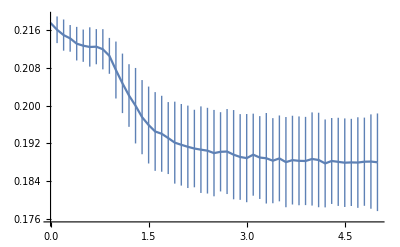

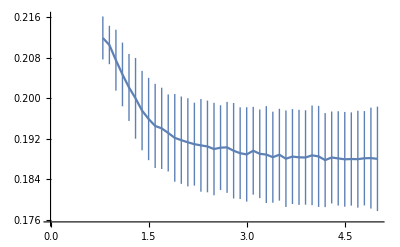

```mathematica
ListLinePlot[Select[luz19pyo2Moi1,0<=#[[1]]<=5&]]
ListLinePlot[Select[luz19pyo2Moi1,0.8<=#[[1]]<=5&]]
luz19pyo2Moi1Lag=0.8;
```

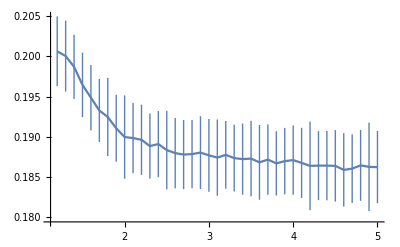

```mathematica
ListLinePlot[Select[pyo2e215Moi1,1.2<=#[[1]]<=5&]]
pyo2e215Moi1Lag=1.2;
```

```mathematica
matlabColors={RGBColor[0,0.4470,0.7410],RGBColor[0.8500,0.3250,0.0980],RGBColor[0.9290,0.6940,0.1250],RGBColor[0.4940,0.1840,0.5560],RGBColor[0.4660,0.6740,0.1880]}
```

{RGBColor[0, 0.447, 0.741],RGBColor[0.85, 0.325, 0.098],RGBColor[0.929, 0.694, 0.125],RGBColor[0.494, 0.184, 0.556],RGBColor[0.466, 0.674, 0.188]}

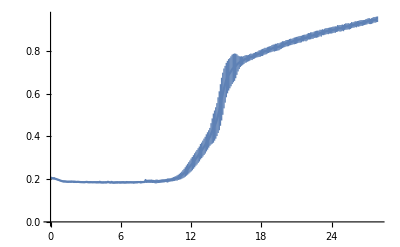

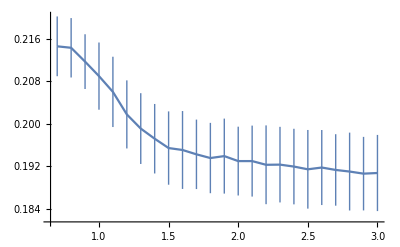

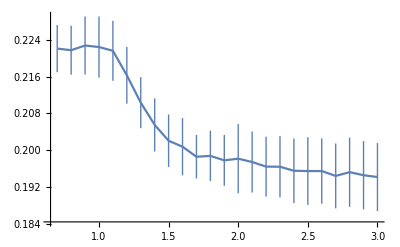

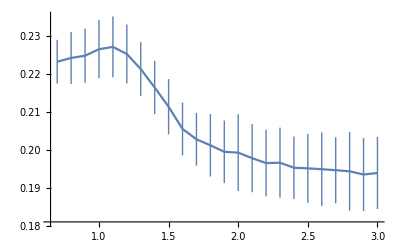

```mathematica
(* lag removal for luz19 *)
ListLinePlot[Select[luz19Moi10,0<=#[[1]]<=50&]]
ListLinePlot[Select[luz19Moi1,0.7<=#[[1]]<=3&]]
ListLinePlot[Select[luz19Moi01,0.7<=#[[1]]<=3&]]
ListLinePlot[Select[luz19Moi001,0.7<=#[[1]]<=3&]]
luz19Moi10Lag=0;
luz19Moi1Lag=0.7; (* 0.7, 0.8 *)
luz19Moi01Lag=0.7; (* 1 *)
luz19Moi001Lag=0.7; (* 1.1 *)
```

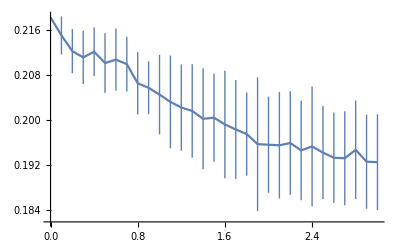

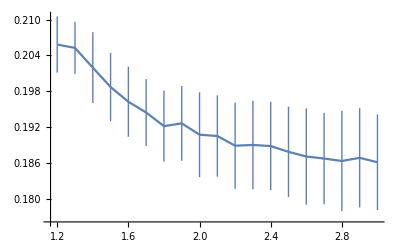

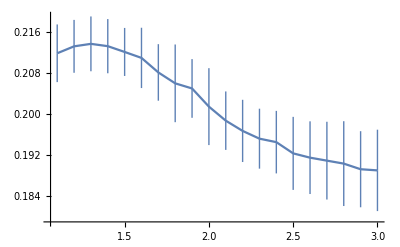

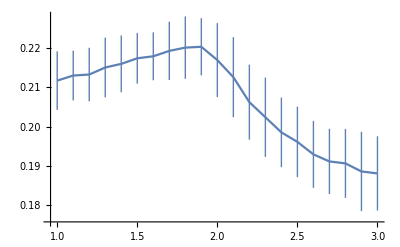

```mathematica
(* lag removal for pyo2 *)
ListLinePlot[Select[pyo2Moi10,0<=#[[1]]<=3&]]
ListLinePlot[Select[pyo2Moi1,1.2<=#[[1]]<=3&]]
ListLinePlot[Select[pyo2Moi01,1.1<=#[[1]]<=3&]]
ListLinePlot[Select[pyo2Moi001,1<=#[[1]]<=3&]]
pyo2Moi10Lag=0;
pyo2Moi1Lag=1.2; (* 1.3 *)
pyo2Moi01Lag=1.1; (* .3 *)
pyo2Moi001Lag=1; (* 1.9 *)
```

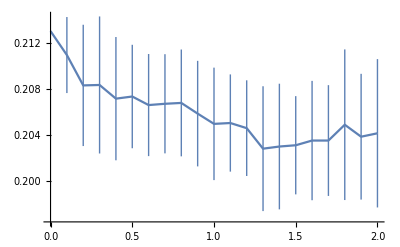

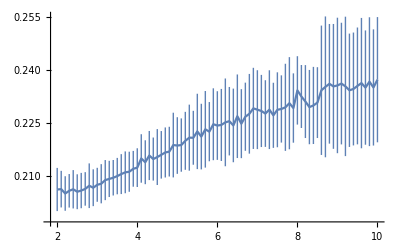

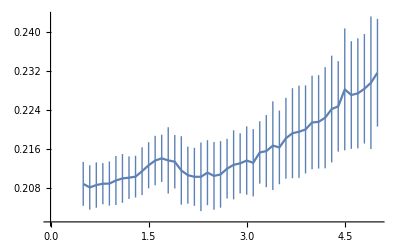

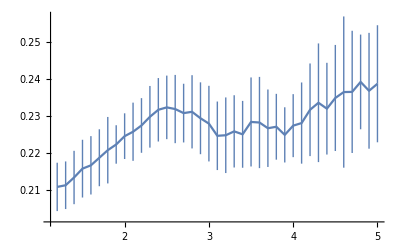

```mathematica
(* lag removal for e215 *)
ListLinePlot[Select[e215Moi10,0<=#[[1]]<=2&]]
ListLinePlot[Select[e215Moi1,2<=#[[1]]<=10&]]
ListLinePlot[Select[e215Moi01,0.5<=#[[1]]<=5&]]
ListLinePlot[Select[e215Moi001,1.2<=#[[1]]<=5&]]
e215Moi10Lag=0;
e215Moi1Lag=2; (* 0 *)
e215Moi01Lag=1; (* 1.7 *)
e215Moi001Lag=1.2; (* 2.5 *)
```

```mathematica
fitPeriod=25; (* carrying capacity is  *)
(* The format of the fitting data is {time - lagtime, MOI, initial value, value} *)
(*beginluz19=Join[Transpose[Join[Transpose[Replace[Select[luz19Moi10fitdata,luz19Moi10Lag<=#[[1]]≤luz19Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi10Lag,y,z},{1}]],{Flatten[Table[Select[luz19Moi10fitdata,#[[1]]==luz19Moi10Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[luz19Moi1fitdata,luz19Moi1Lag<=#[[1]]≤luz19Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi1Lag,y,z},{1}]],{Flatten[Table[Select[luz19Moi1fitdata,#[[1]]==luz19Moi1Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[luz19Moi01fitdata,luz19Moi01Lag<=#[[1]]≤luz19Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi01Lag,y,z},{1}]],{Flatten[Table[Select[luz19Moi01fitdata,#[[1]]==luz19Moi01Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[luz19Moi001fitdata,luz19Moi001Lag<=#[[1]]≤luz19Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi001Lag,y,z},{1}]],{Flatten[Table[Select[luz19Moi001fitdata,#[[1]]==luz19Moi001Lag&][[All,3]],fitPeriod/0.1+1]]}]]];*)
(*beginluz19=Replace[beginluz19,{x_,y_,z_,m_}->{x,y,m,z},{1}];*)
beginluz19=Join[Replace[Select[luz19Moi10fitdata,luz19Moi10Lag<=#[[1]]≤luz19Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi10Lag,y,z},{1}],
Replace[Select[luz19Moi1fitdata,luz19Moi1Lag<=#[[1]]≤luz19Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi1Lag,y,z},{1}],
Replace[Select[luz19Moi01fitdata,luz19Moi01Lag<=#[[1]]≤luz19Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi01Lag,y,z},{1}],
Replace[Select[luz19Moi001fitdata,luz19Moi001Lag<=#[[1]]≤luz19Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-luz19Moi001Lag,y,z},{1}]];
luz19INI=Mean[Join[Select[luz19Moi10fitdata,#[[1]]==luz19Moi10Lag&][[All,3]],
Select[luz19Moi1fitdata,#[[1]]==luz19Moi1Lag&][[All,3]],
Select[luz19Moi1fitdata,#[[1]]==luz19Moi01Lag&][[All,3]],
Select[luz19Moi001fitdata,#[[1]]==luz19Moi001Lag&][[All,3]]]];
(*beginpyo2=Join[Transpose[Join[Transpose[Replace[Select[pyo2Moi10fitdata,pyo2Moi10Lag<=#[[1]]≤pyo2Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi10Lag,y,z},{1}]],{Flatten[Table[Select[pyo2Moi10fitdata,#[[1]]==pyo2Moi10Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[pyo2Moi1fitdata,pyo2Moi1Lag<=#[[1]]≤pyo2Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi1Lag,y,z},{1}]],{Flatten[Table[Select[pyo2Moi1fitdata,#[[1]]==pyo2Moi1Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[pyo2Moi01fitdata,pyo2Moi01Lag<=#[[1]]≤pyo2Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi01Lag,y,z},{1}]],{Flatten[Table[Select[pyo2Moi01fitdata,#[[1]]==pyo2Moi01Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[pyo2Moi001fitdata,pyo2Moi001Lag<=#[[1]]≤pyo2Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi001Lag,y,z},{1}]],{Flatten[Table[Select[pyo2Moi001fitdata,#[[1]]==pyo2Moi001Lag&][[All,3]],fitPeriod/0.1+1]]}]]];*)
beginpyo2=Join[Replace[Select[pyo2Moi10fitdata,pyo2Moi10Lag<=#[[1]]≤pyo2Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi10Lag,y,z},{1}],
Replace[Select[pyo2Moi1fitdata,pyo2Moi1Lag<=#[[1]]≤pyo2Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi1Lag,y,z},{1}],
Replace[Select[pyo2Moi01fitdata,pyo2Moi01Lag<=#[[1]]≤pyo2Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi01Lag,y,z},{1}],
Replace[Select[pyo2Moi001fitdata,pyo2Moi001Lag<=#[[1]]≤pyo2Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-pyo2Moi001Lag,y,z},{1}]];
pyo2INI=Mean[Join[Select[pyo2Moi10fitdata,#[[1]]==pyo2Moi10Lag&][[All,3]],
Select[pyo2Moi1fitdata,#[[1]]==pyo2Moi1Lag&][[All,3]],
Select[pyo2Moi1fitdata,#[[1]]==pyo2Moi01Lag&][[All,3]],
Select[pyo2Moi001fitdata,#[[1]]==pyo2Moi001Lag&][[All,3]]]];
(*beginpyo2=Replace[beginpyo2,{x_,y_,z_,m_}->{x,y,m,z},{1}];*)
(*begine215=Join[Transpose[Join[Transpose[Replace[Select[e215Moi10fitdata,e215Moi10Lag<=#[[1]]≤e215Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi10Lag,y,z},{1}]],{Flatten[Table[Select[e215Moi10fitdata,#[[1]]==e215Moi10Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[e215Moi1fitdata,e215Moi1Lag<=#[[1]]≤e215Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi1Lag,y,z},{1}]],{Flatten[Table[Select[e215Moi1fitdata,#[[1]]==e215Moi1Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[e215Moi01fitdata,e215Moi01Lag<=#[[1]]≤e215Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi01Lag,y,z},{1}]],{Flatten[Table[Select[e215Moi01fitdata,#[[1]]==e215Moi01Lag&][[All,3]],fitPeriod/0.1+1]]}]],
Transpose[Join[Transpose[Replace[Select[e215Moi001fitdata,e215Moi001Lag<=#[[1]]≤e215Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi001Lag,y,z},{1}]],{Flatten[Table[Select[e215Moi001fitdata,#[[1]]==e215Moi001Lag&][[All,3]],fitPeriod/0.1+1]]}]]];*)
begine215=Join[Replace[Select[e215Moi10fitdata,e215Moi10Lag<=#[[1]]≤e215Moi10Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi10Lag,y,z},{1}],
Replace[Select[e215Moi1fitdata,e215Moi1Lag<=#[[1]]≤e215Moi1Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi1Lag,y,z},{1}],
Replace[Select[e215Moi01fitdata,e215Moi01Lag<=#[[1]]≤e215Moi01Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi01Lag,y,z},{1}],
Replace[Select[e215Moi001fitdata,e215Moi001Lag<=#[[1]]≤e215Moi001Lag+fitPeriod&],{x_,y_,z_}->{x-e215Moi001Lag,y,z},{1}]];
e215INI=Mean[Join[Select[e215Moi10fitdata,#[[1]]==e215Moi10Lag&][[All,3]],
Select[e215Moi1fitdata,#[[1]]==e215Moi1Lag&][[All,3]],
Select[e215Moi1fitdata,#[[1]]==e215Moi01Lag&][[All,3]],
Select[e215Moi001fitdata,#[[1]]==e215Moi001Lag&][[All,3]]]];
(*begine215=Replace[begine215,{x_,y_,z_,m_}->{x,y,m,z},{1}];*)
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\luz19_fit.csv",beginluz19]
Export["C:\\Users\\zhiyu\\Desktop\\pyo2_fit.csv",beginpyo2]
Export["C:\\Users\\zhiyu\\Desktop\\e215_fit.csv",begine215]
```

C:\Users\zhiyu\Desktop\luz19_fit.csv

C:\Users\zhiyu\Desktop\pyo2_fit.csv

C:\Users\zhiyu\Desktop\e215_fit.csv

```mathematica
Quantile[Join[luz19Boot[[2;;,2]],pyo2Boot[[2;;,2]]],{0.025,0.975}]
```

{215.255,597.726}

```mathematica
Quantile[pyo2Boot[[2;;,1]],{0.025,0.975}]
```

{0.00925121,0.0148981}

```mathematica
Quantile[luz19Boot[[2;;,1]],{0.025,0.975}]
```

{0.0188266,0.0328229}

```mathematica
Quantile[luz19Boot[[2;;,3]],{0.025,0.975}]
```

{0.122787,0.173847}

```mathematica
Quantile[pyo2Boot[[2;;,3]],{0.025,0.975}]
```

{0.136515,0.209867}

```mathematica
Quantile[e215Boot[[2;;,3]],{0.025,0.975}]
```

{0.0442903,0.0573397}

```mathematica
Quantile[luz19e215Boot[[2;;,1]],{0.025,0.975}]
```

{4.75831×10^-18,0.0000568865}

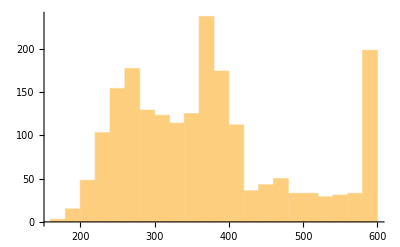

```mathematica
Histogram[Join[luz19Boot[[2;;,2]],pyo2Boot[[2;;,2]]]]
```

```mathematica
(0.718+0.744)/2
```

0.731

```mathematica
(215+598)/2//N
```

406.5

```mathematica
luz19Boot=Import["C:\\Users\\zhiyu\\Dropbox\\PC (2)\\Desktop\\Git\\matlab-python-ode-fit\\julia\\luz19_boot_valid.csv"];
pyo2Boot=Import["C:\\Users\\zhiyu\\Dropbox\\PC (2)\\Desktop\\Git\\matlab-python-ode-fit\\julia\\pyo2_boot_valid.csv"];
e215Boot=Import["C:\\Users\\zhiyu\\Dropbox\\PC (2)\\Desktop\\Git\\matlab-python-ode-fit\\julia\\e215_boot_valid.csv"];
luz19e215Boot=Import["C:\\Users\\zhiyu\\Dropbox\\PC (2)\\Desktop\\Git\\matlab-python-ode-fit\\julia\\luz19_e215_boot_valid.csv"];
PH[a_,k_,b_,h_,s_,p_,rr_]={basalr*B*(1-(B+Br)/k)-b*B*P-a*B,
-s*Bi+b*B*P,
a*B+rr*Br*(1-(B+Br)/k),
-p*P+h*s*Bi-b*B*P,
basalr*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rr*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
meanluz19Init=Select[luz19Moi1,#[[1]]==luz19Moi1Lag&][[1,2,1]];
meanpyo2Init=Select[pyo2Moi1,#[[1]]==pyo2Moi1Lag&][[1,2,1]];
meane215Init=Select[e215Moi1,#[[1]]==e215Moi1Lag&][[1,2,1]];
solluz19=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[luz19Moi1Lag]=={meanluz19Init,0,0,meanluz19Init,meanluz19Init}},Bt[t],{t,luz19Moi1Lag,50},{a,b,s,k}];
solluz19boot=Apply[solluz19,luz19Boot[[2;;]],{1}];
solluz19moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solluz19moi01boot=Apply[solluz19moi01,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solluz19moi01bootbr=Apply[solluz19moi01,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solluz19moi01bootbi=Apply[solluz19moi01,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
solluz19moi01bootp=Apply[solluz19moi01,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
solluz19moi01bootb=Apply[solluz19moi01,luz19Boot[[2;;,1;;3]],{1}];

solluz19moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solluz19moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solluz19moi10boot=Apply[solluz19moi10,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1boot=Apply[solluz19moi1,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solluz19moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solluz19moi10bootbr=Apply[solluz19moi10,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1bootbr=Apply[solluz19moi1,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solluz19moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solluz19moi10bootbi=Apply[solluz19moi10,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1bootbi=Apply[solluz19moi1,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
solluz19moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},P[t],{t,0,50},{a,b,s}];
solluz19moi10bootp=Apply[solluz19moi10,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1bootp=Apply[solluz19moi1,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},B[t],{t,0,50},{a,b,s}];
solluz19moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},B[t],{t,0,50},{a,b,s}];
solluz19moi10bootb=Apply[solluz19moi10,luz19Boot[[2;;,1;;3]],{1}];
solluz19moi1bootb=Apply[solluz19moi1,luz19Boot[[2;;,1;;3]],{1}];


solpyo2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[pyo2Moi1Lag]=={meanpyo2Init,0,0,meanpyo2Init,meanpyo2Init}},Bt[t],{t,pyo2Moi1Lag,50},{a,b,s,k}];
solpyo2boot=Apply[solpyo2,pyo2Boot[[2;;]],{1}];

solpyo2moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solpyo2moi01bootbt=Apply[solpyo2moi01,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solpyo2moi01bootbr=Apply[solpyo2moi01,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solpyo2moi01bootbi=Apply[solpyo2moi01,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
solpyo2moi01bootp=Apply[solpyo2moi01,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
solpyo2moi01bootb=Apply[solpyo2moi01,pyo2Boot[[2;;,1;;3]],{1}];

solpyo2moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solpyo2moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
solpyo2moi10boot=Apply[solpyo2moi10,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1boot=Apply[solpyo2moi1,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solpyo2moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
solpyo2moi10bootbr=Apply[solpyo2moi10,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1bootbr=Apply[solpyo2moi1,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solpyo2moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
solpyo2moi10bootbi=Apply[solpyo2moi10,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1bootbi=Apply[solpyo2moi1,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
solpyo2moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
solpyo2moi10bootp=Apply[solpyo2moi10,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1bootp=Apply[solpyo2moi1,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
solpyo2moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
solpyo2moi10bootb=Apply[solpyo2moi10,pyo2Boot[[2;;,1;;3]],{1}];
solpyo2moi1bootb=Apply[solpyo2moi1,pyo2Boot[[2;;,1;;3]],{1}];


sole215=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[e215Moi1Lag]=={meane215Init,0,0,meane215Init,meane215Init}},Bt[t],{t,e215Moi1Lag,50},{a,b,s,k}];
sole215boot=Apply[sole215,e215Boot[[2;;]],{1}];
sole215moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
sole215moi01bootbr=Apply[sole215moi01,e215Boot[[2;;,1;;3]],{1}];
sole215moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
sole215moi01bootbi=Apply[sole215moi01,e215Boot[[2;;,1;;3]],{1}];
sole215moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
sole215moi01bootp=Apply[sole215moi01,e215Boot[[2;;,1;;3]],{1}];
sole215moi01=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*0.1,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
sole215moi01bootb=Apply[sole215moi01,e215Boot[[2;;,1;;3]],{1}];

sole215moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
sole215moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bt[t]],{t,0,50},{a,b,s}];
sole215moi10boot=Apply[sole215moi10,e215Boot[[2;;,1;;3]],{1}];
sole215moi1boot=Apply[sole215moi1,e215Boot[[2;;,1;;3]],{1}];
sole215moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
sole215moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Br[t]],{t,0,50},{a,b,s}];
sole215moi10bootbr=Apply[sole215moi10,e215Boot[[2;;,1;;3]],{1}];
sole215moi1bootbr=Apply[sole215moi1,e215Boot[[2;;,1;;3]],{1}];
sole215moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
sole215moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[Bi[t]],{t,0,50},{a,b,s}];
sole215moi10bootbi=Apply[sole215moi10,e215Boot[[2;;,1;;3]],{1}];
sole215moi1bootbi=Apply[sole215moi1,e215Boot[[2;;,1;;3]],{1}];
sole215moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
sole215moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[P[t]],{t,0,50},{a,b,s}];
sole215moi10bootp=Apply[sole215moi10,e215Boot[[2;;,1;;3]],{1}];
sole215moi1bootp=Apply[sole215moi1,e215Boot[[2;;,1;;3]],{1}];
sole215moi1=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
sole215moi10=ParametricNDSolveValue[{{X'[t]==(PH[a,0.9,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[0]=={0.2,0,0,0.2*10,0.2}},CFU[B[t]],{t,0,50},{a,b,s}];
sole215moi10bootb=Apply[sole215moi10,e215Boot[[2;;,1;;3]],{1}];
sole215moi1bootb=Apply[sole215moi1,e215Boot[[2;;,1;;3]],{1}];
```

```mathematica
timeSampleluz19=Table[i,{i,luz19Moi1Lag,25,0.1}];
timeSamplepyo2e215=Table[i,{i,pyo2e215Moi1Lag,27,0.1}];
timeSampleluz19pyo2=Table[i,{i,luz19pyo2Moi1Lag,27,0.1}];
timeSampleluz19e215=Table[i,{i,luz19e215Moi1Lag,27,0.1}];
timeSimulation=Table[i,{i,0,25,0.1}];
timeSamplepyo2=Table[i,{i,pyo2Moi1Lag,25,0.1}];
timeSamplee215=Table[i,{i,e215Moi1Lag,25,0.1}];
```

```mathematica
solluz19bootDiscrete=Map[solluz19boot/.{t->#}&,timeSampleluz19,{1}];
solluz19moi10bootDiscrete=Map[solluz19moi10boot/.{t->#}&,timeSimulation,{1}];
solluz19moi1bootDiscrete=Map[solluz19moi1boot/.{t->#}&,timeSimulation,{1}];
solluz19moi01bootDiscrete=Map[solluz19moi01boot/.{t->#}&,timeSimulation,{1}];
solluz19moi10bootDiscretebr=Map[solluz19moi10bootbr/.{t->#}&,timeSimulation,{1}];
solluz19moi1bootDiscretebr=Map[solluz19moi1bootbr/.{t->#}&,timeSimulation,{1}];
solluz19moi01bootDiscretebr=Map[solluz19moi01bootbr/.{t->#}&,timeSimulation,{1}];
solluz19moi10bootDiscretebi=Map[solluz19moi10bootbi/.{t->#}&,timeSimulation,{1}];
solluz19moi1bootDiscretebi=Map[solluz19moi1bootbi/.{t->#}&,timeSimulation,{1}];
solluz19moi01bootDiscretebi=Map[solluz19moi01bootbi/.{t->#}&,timeSimulation,{1}];
solluz19moi10bootDiscretep=Map[solluz19moi10bootp/.{t->#}&,timeSimulation,{1}];
solluz19moi1bootDiscretep=Map[solluz19moi1bootp/.{t->#}&,timeSimulation,{1}];
solluz19moi01bootDiscretep=Map[solluz19moi01bootp/.{t->#}&,timeSimulation,{1}];
solluz19moi10bootDiscreteb=Map[solluz19moi10bootb/.{t->#}&,timeSimulation,{1}];
solluz19moi1bootDiscreteb=Map[solluz19moi1bootb/.{t->#}&,timeSimulation,{1}];
solluz19moi01bootDiscreteb=Map[solluz19moi01bootb/.{t->#}&,timeSimulation,{1}];

solpyo2bootDiscrete=Map[solpyo2boot/.{t->#}&,timeSamplepyo2,{1}];
solpyo2moi10bootDiscrete=Map[solpyo2moi10boot/.{t->#}&,timeSimulation,{1}];
solpyo2moi1bootDiscrete=Map[solpyo2moi1boot/.{t->#}&,timeSimulation,{1}];
solpyo2moi01bootDiscrete=Map[solpyo2moi01boot/.{t->#}&,timeSimulation,{1}];
solpyo2moi10bootDiscretebr=Map[solpyo2moi10bootbr/.{t->#}&,timeSimulation,{1}];
solpyo2moi1bootDiscretebr=Map[solpyo2moi1bootbr/.{t->#}&,timeSimulation,{1}];
solpyo2moi01bootDiscretebr=Map[solpyo2moi01bootbr/.{t->#}&,timeSimulation,{1}];
solpyo2moi10bootDiscretebi=Map[solpyo2moi10bootbi/.{t->#}&,timeSimulation,{1}];
solpyo2moi1bootDiscretebi=Map[solpyo2moi1bootbi/.{t->#}&,timeSimulation,{1}];
solpyo2moi01bootDiscretebi=Map[solpyo2moi01bootbi/.{t->#}&,timeSimulation,{1}];
solpyo2moi10bootDiscretep=Map[solpyo2moi10bootp/.{t->#}&,timeSimulation,{1}];
solpyo2moi1bootDiscretep=Map[solpyo2moi1bootp/.{t->#}&,timeSimulation,{1}];
solpyo2moi01bootDiscretep=Map[solpyo2moi01bootp/.{t->#}&,timeSimulation,{1}];
solpyo2moi10bootDiscreteb=Map[solpyo2moi10bootb/.{t->#}&,timeSimulation,{1}];
solpyo2moi1bootDiscreteb=Map[solpyo2moi1bootb/.{t->#}&,timeSimulation,{1}];
solpyo2moi01bootDiscreteb=Map[solpyo2moi01bootb/.{t->#}&,timeSimulation,{1}];



sole215bootDiscrete=Map[sole215boot/.{t->#}&,timeSamplee215,{1}];
sole215moi10bootDiscrete=Map[sole215moi10boot/.{t->#}&,timeSimulation,{1}];
sole215moi1bootDiscrete=Map[sole215moi1boot/.{t->#}&,timeSimulation,{1}];
sole215moi01bootDiscrete=Map[sole215moi01boot/.{t->#}&,timeSimulation,{1}];
sole215moi10bootDiscretebr=Map[sole215moi10bootbr/.{t->#}&,timeSimulation,{1}];
sole215moi1bootDiscretebr=Map[sole215moi1bootbr/.{t->#}&,timeSimulation,{1}];
sole215moi01bootDiscretebr=Map[sole215moi01bootbr/.{t->#}&,timeSimulation,{1}];
sole215moi10bootDiscretebi=Map[sole215moi10bootbi/.{t->#}&,timeSimulation,{1}];
sole215moi1bootDiscretebi=Map[sole215moi1bootbi/.{t->#}&,timeSimulation,{1}];
sole215moi01bootDiscretebi=Map[sole215moi01bootbi/.{t->#}&,timeSimulation,{1}];
sole215moi10bootDiscretep=Map[sole215moi10bootp/.{t->#}&,timeSimulation,{1}];
sole215moi1bootDiscretep=Map[sole215moi1bootp/.{t->#}&,timeSimulation,{1}];
sole215moi01bootDiscretep=Map[sole215moi01bootp/.{t->#}&,timeSimulation,{1}];
sole215moi10bootDiscreteb=Map[sole215moi10bootb/.{t->#}&,timeSimulation,{1}];
sole215moi1bootDiscreteb=Map[sole215moi1bootb/.{t->#}&,timeSimulation,{1}];
sole215moi01bootDiscreteb=Map[sole215moi01bootb/.{t->#}&,timeSimulation,{1}];
```

```mathematica
luz19moi01Meanbr=Map[Mean[#]&,solluz19moi01bootDiscretebr];
luz19moi01Meanbr=Transpose[{timeSimulation,luz19moi01Meanbr}];
luz19moi01CIbr=Map[Quantile[#,{0.025,0.975}]&,solluz19moi01bootDiscretebr];
luz19moi01ciwidthbr=luz19moi01CIbr[[All,2]]-luz19moi01CIbr[[All,1]];
luz19moi1Meanbr=Map[Mean[#]&,solluz19moi1bootDiscretebr];
luz19moi1Meanbr=Transpose[{timeSimulation,luz19moi1Meanbr}];
luz19moi1CIbr=Map[Quantile[#,{0.025,0.975}]&,solluz19moi1bootDiscretebr];
luz19moi1ciwidthbr=luz19moi1CIbr[[All,2]]-luz19moi1CIbr[[All,1]];
luz19moi10Meanbr=Map[Mean[#]&,solluz19moi10bootDiscretebr];
luz19moi10Meanbr=Transpose[{timeSimulation,luz19moi10Meanbr}];
luz19moi10CIbr=Map[Quantile[#,{0.025,0.975}]&,solluz19moi10bootDiscretebr];
luz19moi10ciwidthbr=luz19moi10CIbr[[All,2]]-luz19moi10CIbr[[All,1]];

luz19moi01Meanbi=Map[Mean[#]&,solluz19moi01bootDiscretebi];
luz19moi01Meanbi=Transpose[{timeSimulation,luz19moi01Meanbi}];
luz19moi01CIbi=Map[Quantile[#,{0.025,0.975}]&,solluz19moi01bootDiscretebi];
luz19moi01ciwidthbi=luz19moi01CIbi[[All,2]]-luz19moi01CIbi[[All,1]];
luz19moi1Meanbi=Map[Mean[#]&,solluz19moi1bootDiscretebi];
luz19moi1Meanbi=Transpose[{timeSimulation,luz19moi1Meanbi}];
luz19moi1CIbi=Map[Quantile[#,{0.025,0.975}]&,solluz19moi1bootDiscretebi];
luz19moi1ciwidthbi=luz19moi1CIbi[[All,2]]-luz19moi1CIbi[[All,1]];
luz19moi10Meanbi=Map[Mean[#]&,solluz19moi10bootDiscretebi];
luz19moi10Meanbi=Transpose[{timeSimulation,luz19moi10Meanbi}];
luz19moi10CIbi=Map[Quantile[#,{0.025,0.975}]&,solluz19moi10bootDiscretebi];
luz19moi10ciwidthbi=luz19moi10CIbi[[All,2]]-luz19moi10CIbi[[All,1]];

luz19moi01Meanp=Map[Mean[#]&,solluz19moi01bootDiscretep];
luz19moi01Meanp=Transpose[{timeSimulation,luz19moi01Meanp}];
luz19moi01CIp=Map[Quantile[#,{0.025,0.975}]&,solluz19moi01bootDiscretep];
luz19moi01ciwidthp=luz19moi01CIp[[All,2]]-luz19moi01CIp[[All,1]];
luz19moi1Meanp=Map[Mean[#]&,solluz19moi1bootDiscretep];
luz19moi1Meanp=Transpose[{timeSimulation,luz19moi1Meanp}];
luz19moi1CIp=Map[Quantile[#,{0.025,0.975}]&,solluz19moi1bootDiscretep];
luz19moi1ciwidthp=luz19moi1CIp[[All,2]]-luz19moi1CIp[[All,1]];
luz19moi10Meanp=Map[Mean[#]&,solluz19moi10bootDiscretep];
luz19moi10Meanp=Transpose[{timeSimulation,luz19moi10Meanp}];
luz19moi10CIp=Map[Quantile[#,{0.025,0.975}]&,solluz19moi10bootDiscretep];
luz19moi10ciwidthp=luz19moi10CIp[[All,2]]-luz19moi10CIp[[All,1]];

luz19moi01Meanb=Map[Mean[#]&,solluz19moi01bootDiscreteb];
luz19moi01Meanb=Transpose[{timeSimulation,luz19moi01Meanb}];
luz19moi01CIb=Map[Quantile[#,{0.025,0.975}]&,solluz19moi01bootDiscreteb];
luz19moi01ciwidthb=luz19moi01CIb[[All,2]]-luz19moi01CIb[[All,1]];
luz19moi1Meanb=Map[Mean[#]&,solluz19moi1bootDiscreteb];
luz19moi1Meanb=Transpose[{timeSimulation,luz19moi1Meanb}];
luz19moi1CIb=Map[Quantile[#,{0.025,0.975}]&,solluz19moi1bootDiscreteb];
luz19moi1ciwidthb=luz19moi1CIb[[All,2]]-luz19moi1CIb[[All,1]];
luz19moi10Meanb=Map[Mean[#]&,solluz19moi10bootDiscreteb];
luz19moi10Meanb=Transpose[{timeSimulation,luz19moi10Meanb}];
luz19moi10CIb=Map[Quantile[#,{0.025,0.975}]&,solluz19moi10bootDiscreteb];
luz19moi10ciwidthb=luz19moi10CIb[[All,2]]-luz19moi10CIb[[All,1]];


pyo2moi01Meanbr=Map[Mean[#]&,solpyo2moi01bootDiscretebr];
pyo2moi01Meanbr=Transpose[{timeSimulation,pyo2moi01Meanbr}];
pyo2moi01CIbr=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi01bootDiscretebr];
pyo2moi01ciwidthbr=pyo2moi01CIbr[[All,2]]-pyo2moi01CIbr[[All,1]];
pyo2moi1Meanbr=Map[Mean[#]&,solpyo2moi1bootDiscretebr];
pyo2moi1Meanbr=Transpose[{timeSimulation,pyo2moi1Meanbr}];
pyo2moi1CIbr=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi1bootDiscretebr];
pyo2moi1ciwidthbr=pyo2moi1CIbr[[All,2]]-pyo2moi1CIbr[[All,1]];
pyo2moi10Meanbr=Map[Mean[#]&,solpyo2moi10bootDiscretebr];
pyo2moi10Meanbr=Transpose[{timeSimulation,pyo2moi10Meanbr}];
pyo2moi10CIbr=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi10bootDiscretebr];
pyo2moi10ciwidthbr=pyo2moi10CIbr[[All,2]]-pyo2moi10CIbr[[All,1]];

pyo2moi01Meanbi=Map[Mean[#]&,solpyo2moi01bootDiscretebi];
pyo2moi01Meanbi=Transpose[{timeSimulation,pyo2moi01Meanbi}];
pyo2moi01CIbi=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi01bootDiscretebi];
pyo2moi01ciwidthbi=pyo2moi01CIbi[[All,2]]-pyo2moi01CIbi[[All,1]];
pyo2moi1Meanbi=Map[Mean[#]&,solpyo2moi1bootDiscretebi];
pyo2moi1Meanbi=Transpose[{timeSimulation,pyo2moi1Meanbi}];
pyo2moi1CIbi=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi1bootDiscretebi];
pyo2moi1ciwidthbi=pyo2moi1CIbi[[All,2]]-pyo2moi1CIbi[[All,1]];
pyo2moi10Meanbi=Map[Mean[#]&,solpyo2moi10bootDiscretebi];
pyo2moi10Meanbi=Transpose[{timeSimulation,pyo2moi10Meanbi}];
pyo2moi10CIbi=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi10bootDiscretebi];
pyo2moi10ciwidthbi=pyo2moi10CIbi[[All,2]]-pyo2moi10CIbi[[All,1]];

pyo2moi01Meanp=Map[Mean[#]&,solpyo2moi01bootDiscretep];
pyo2moi01Meanp=Transpose[{timeSimulation,pyo2moi01Meanp}];
pyo2moi01CIp=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi01bootDiscretep];
pyo2moi01ciwidthp=pyo2moi01CIp[[All,2]]-pyo2moi01CIp[[All,1]];
pyo2moi1Meanp=Map[Mean[#]&,solpyo2moi1bootDiscretep];
pyo2moi1Meanp=Transpose[{timeSimulation,pyo2moi1Meanp}];
pyo2moi1CIp=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi1bootDiscretep];
pyo2moi1ciwidthp=pyo2moi1CIp[[All,2]]-pyo2moi1CIp[[All,1]];
pyo2moi10Meanp=Map[Mean[#]&,solpyo2moi10bootDiscretep];
pyo2moi10Meanp=Transpose[{timeSimulation,pyo2moi10Meanp}];
pyo2moi10CIp=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi10bootDiscretep];
pyo2moi10ciwidthp=pyo2moi10CIp[[All,2]]-pyo2moi10CIp[[All,1]];

pyo2moi01Meanb=Map[Mean[#]&,solpyo2moi01bootDiscreteb];
pyo2moi01Meanb=Transpose[{timeSimulation,pyo2moi01Meanb}];
pyo2moi01CIb=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi01bootDiscreteb];
pyo2moi01ciwidthb=pyo2moi01CIb[[All,2]]-pyo2moi01CIb[[All,1]];
pyo2moi1Meanb=Map[Mean[#]&,solpyo2moi1bootDiscreteb];
pyo2moi1Meanb=Transpose[{timeSimulation,pyo2moi1Meanb}];
pyo2moi1CIb=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi1bootDiscreteb];
pyo2moi1ciwidthb=pyo2moi1CIb[[All,2]]-pyo2moi1CIb[[All,1]];
pyo2moi10Meanb=Map[Mean[#]&,solpyo2moi10bootDiscreteb];
pyo2moi10Meanb=Transpose[{timeSimulation,pyo2moi10Meanb}];
pyo2moi10CIb=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi10bootDiscreteb];
pyo2moi10ciwidthb=pyo2moi10CIb[[All,2]]-pyo2moi10CIb[[All,1]];


e215moi01Meanbr=Map[Mean[#]&,sole215moi01bootDiscretebr];
e215moi01Meanbr=Transpose[{timeSimulation,e215moi01Meanbr}];
e215moi01CIbr=Map[Quantile[#,{0.025,0.975}]&,sole215moi01bootDiscretebr];
e215moi01ciwidthbr=e215moi01CIbr[[All,2]]-e215moi01CIbr[[All,1]];
e215moi1Meanbr=Map[Mean[#]&,sole215moi1bootDiscretebr];
e215moi1Meanbr=Transpose[{timeSimulation,e215moi1Meanbr}];
e215moi1CIbr=Map[Quantile[#,{0.025,0.975}]&,sole215moi1bootDiscretebr];
e215moi1ciwidthbr=e215moi1CIbr[[All,2]]-e215moi1CIbr[[All,1]];
e215moi10Meanbr=Map[Mean[#]&,sole215moi10bootDiscretebr];
e215moi10Meanbr=Transpose[{timeSimulation,e215moi10Meanbr}];
e215moi10CIbr=Map[Quantile[#,{0.025,0.975}]&,sole215moi10bootDiscretebr];
e215moi10ciwidthbr=e215moi10CIbr[[All,2]]-e215moi10CIbr[[All,1]];

e215moi01Meanbi=Map[Mean[#]&,sole215moi01bootDiscretebi];
e215moi01Meanbi=Transpose[{timeSimulation,e215moi01Meanbi}];
e215moi01CIbi=Map[Quantile[#,{0.025,0.975}]&,sole215moi01bootDiscretebi];
e215moi01ciwidthbi=e215moi01CIbi[[All,2]]-e215moi01CIbi[[All,1]];
e215moi1Meanbi=Map[Mean[#]&,sole215moi1bootDiscretebi];
e215moi1Meanbi=Transpose[{timeSimulation,e215moi1Meanbi}];
e215moi1CIbi=Map[Quantile[#,{0.025,0.975}]&,sole215moi1bootDiscretebi];
e215moi1ciwidthbi=e215moi1CIbi[[All,2]]-e215moi1CIbi[[All,1]];
e215moi10Meanbi=Map[Mean[#]&,sole215moi10bootDiscretebi];
e215moi10Meanbi=Transpose[{timeSimulation,e215moi10Meanbi}];
e215moi10CIbi=Map[Quantile[#,{0.025,0.975}]&,sole215moi10bootDiscretebi];
e215moi10ciwidthbi=e215moi10CIbi[[All,2]]-e215moi10CIbi[[All,1]];

e215moi01Meanp=Map[Mean[#]&,sole215moi01bootDiscretep];
e215moi01Meanp=Transpose[{timeSimulation,e215moi01Meanp}];
e215moi01CIp=Map[Quantile[#,{0.025,0.975}]&,sole215moi01bootDiscretep];
e215moi01ciwidthp=e215moi01CIp[[All,2]]-e215moi01CIp[[All,1]];
e215moi1Meanp=Map[Mean[#]&,sole215moi1bootDiscretep];
e215moi1Meanp=Transpose[{timeSimulation,e215moi1Meanp}];
e215moi1CIp=Map[Quantile[#,{0.025,0.975}]&,sole215moi1bootDiscretep];
e215moi1ciwidthp=e215moi1CIp[[All,2]]-e215moi1CIp[[All,1]];
e215moi10Meanp=Map[Mean[#]&,sole215moi10bootDiscretep];
e215moi10Meanp=Transpose[{timeSimulation,e215moi10Meanp}];
e215moi10CIp=Map[Quantile[#,{0.025,0.975}]&,sole215moi10bootDiscretep];
e215moi10ciwidthp=e215moi10CIp[[All,2]]-e215moi10CIp[[All,1]];

e215moi01Meanb=Map[Mean[#]&,sole215moi01bootDiscreteb];
e215moi01Meanb=Transpose[{timeSimulation,e215moi01Meanb}];
e215moi01CIb=Map[Quantile[#,{0.025,0.975}]&,sole215moi01bootDiscreteb];
e215moi01ciwidthb=e215moi01CIb[[All,2]]-e215moi01CIb[[All,1]];
e215moi1Meanb=Map[Mean[#]&,sole215moi1bootDiscreteb];
e215moi1Meanb=Transpose[{timeSimulation,e215moi1Meanb}];
e215moi1CIb=Map[Quantile[#,{0.025,0.975}]&,sole215moi1bootDiscreteb];
e215moi1ciwidthb=e215moi1CIb[[All,2]]-e215moi1CIb[[All,1]];
e215moi10Meanb=Map[Mean[#]&,sole215moi10bootDiscreteb];
e215moi10Meanb=Transpose[{timeSimulation,e215moi10Meanb}];
e215moi10CIb=Map[Quantile[#,{0.025,0.975}]&,sole215moi10bootDiscreteb];
e215moi10ciwidthb=e215moi10CIb[[All,2]]-e215moi10CIb[[All,1]];
```

```mathematica
luz19Mean=Map[Mean[#]&,solluz19bootDiscrete];
luz19Mean=Transpose[{timeSampleluz19,luz19Mean}];
luz19CI=Map[Quantile[#,{0.025,0.975}]&,solluz19bootDiscrete];
luz19ciwidth=luz19CI[[All,2]]-luz19CI[[All,1]];

luz19moi01Mean=Map[Mean[#]&,solluz19moi01bootDiscrete];
luz19moi01Mean=Transpose[{timeSimulation,luz19moi01Mean}];
luz19moi01CI=Map[Quantile[#,{0.025,0.975}]&,solluz19moi01bootDiscrete];
luz19moi01ciwidth=luz19moi01CI[[All,2]]-luz19moi01CI[[All,1]];

luz19moi1Mean=Map[Mean[#]&,solluz19moi1bootDiscrete];
luz19moi1Mean=Transpose[{timeSimulation,luz19moi1Mean}];
luz19moi1CI=Map[Quantile[#,{0.025,0.975}]&,solluz19moi1bootDiscrete];
luz19moi1ciwidth=luz19moi1CI[[All,2]]-luz19moi1CI[[All,1]];

luz19moi10Mean=Map[Mean[#]&,solluz19moi10bootDiscrete];
luz19moi10Mean=Transpose[{timeSimulation,luz19moi10Mean}];
luz19moi10CI=Map[Quantile[#,{0.025,0.975}]&,solluz19moi10bootDiscrete];
luz19moi10ciwidth=luz19moi10CI[[All,2]]-luz19moi10CI[[All,1]];

pyo2Mean=Map[Mean[#]&,solpyo2bootDiscrete];
pyo2Mean=Transpose[{timeSamplepyo2,pyo2Mean}];
pyo2CI=Map[Quantile[#,{0.025,0.975}]&,solpyo2bootDiscrete];
pyo2ciwidth=pyo2CI[[All,2]]-pyo2CI[[All,1]];

pyo2moi01Mean=Map[Mean[#]&,solpyo2moi01bootDiscrete];
pyo2moi01Mean=Transpose[{timeSimulation,pyo2moi01Mean}];
pyo2moi01CI=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi01bootDiscrete];
pyo2moi01ciwidth=pyo2moi01CI[[All,2]]-pyo2moi01CI[[All,1]];

pyo2moi1Mean=Map[Mean[#]&,solpyo2moi1bootDiscrete];
pyo2moi1Mean=Transpose[{timeSimulation,pyo2moi1Mean}];
pyo2moi1CI=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi1bootDiscrete];
pyo2moi1ciwidth=pyo2moi1CI[[All,2]]-pyo2moi1CI[[All,1]];

pyo2moi10Mean=Map[Mean[#]&,solpyo2moi10bootDiscrete];
pyo2moi10Mean=Transpose[{timeSimulation,pyo2moi10Mean}];
pyo2moi10CI=Map[Quantile[#,{0.025,0.975}]&,solpyo2moi10bootDiscrete];
pyo2moi10ciwidth=pyo2moi10CI[[All,2]]-pyo2moi10CI[[All,1]];

e215Mean=Map[Mean[#]&,sole215bootDiscrete];
e215Mean=Transpose[{timeSamplee215,e215Mean}];
e215CI=Map[Quantile[#,{0.025,0.975}]&,sole215bootDiscrete];
e215ciwidth=e215CI[[All,2]]-e215CI[[All,1]];

e215moi01Mean=Map[Mean[#]&,sole215moi01bootDiscrete];
e215moi01Mean=Transpose[{timeSimulation,e215moi01Mean}];
e215moi01CI=Map[Quantile[#,{0.025,0.975}]&,sole215moi01bootDiscrete];
e215moi01ciwidth=e215moi01CI[[All,2]]-e215moi01CI[[All,1]];

e215moi1Mean=Map[Mean[#]&,sole215moi1bootDiscrete];
e215moi1Mean=Transpose[{timeSimulation,e215moi1Mean}];
e215moi1CI=Map[Quantile[#,{0.025,0.975}]&,sole215moi1bootDiscrete];
e215moi1ciwidth=e215moi1CI[[All,2]]-e215moi1CI[[All,1]];

e215moi10Mean=Map[Mean[#]&,sole215moi10bootDiscrete];
e215moi10Mean=Transpose[{timeSimulation,e215moi10Mean}];
e215moi10CI=Map[Quantile[#,{0.025,0.975}]&,sole215moi10bootDiscrete];
e215moi10ciwidth=e215moi10CI[[All,2]]-e215moi10CI[[All,1]];
```

```mathematica
luz19moi1=Replace[Select[luz19Moi1fitdata,luz19Moi1Lag<=#[[1]]≤25&],{x_,y_,z_}->{x,z},{1}];
pyo2moi1=Replace[Select[pyo2Moi1fitdata,pyo2Moi1Lag<=#[[1]]≤25&],{x_,y_,z_}->{x,z},{1}];
e215moi1=Replace[Select[e215Moi1fitdata,e215Moi1Lag<=#[[1]]≤25&],{x_,y_,z_}->{x,z},{1}];
```

```mathematica
luz19SEwidth={};
Module[{i,t,y,ys},
For[i=1,i<=Length[luz19Mean],i++,
t=luz19Mean[[i,1]];
y=luz19Mean[[i,2]];
luz19SEwidth=Append[luz19SEwidth,StandardDeviation[Select[luz19moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];
]];

pyo2SEwidth={};
Module[{i,t,y,ys},
For[i=1,i<=Length[pyo2Mean],i++,
t=pyo2Mean[[i,1]];
y=pyo2Mean[[i,2]];
pyo2SEwidth=Append[pyo2SEwidth,StandardDeviation[Select[pyo2moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];
]];

e215SEwidth={};
Module[{i,t,y,ys},
For[i=1,i<=Length[e215Mean],i++,
t=e215Mean[[i,1]];
y=e215Mean[[i,2]];
e215SEwidth=Append[e215SEwidth,StandardDeviation[Select[e215moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];
]];
```

```mathematica
nluz19=Length[Select[luz19moi1,#[[1]]==luz19Moi1Lag&]];
npyo2=Length[Select[pyo2moi1,#[[1]]==pyo2Moi1Lag&]];
ne215=Length[Select[e215moi1,#[[1]]==e215Moi1Lag&]];
```

```mathematica
ne215
```

30

```mathematica
nluz19
```

33

```mathematica
npyo2
```

32

```mathematica
luz19moi10MeanCIbr=Table[{luz19moi10Meanbr[[i]][[1]],Around[luz19moi10Meanbr[[i]][[2]],luz19moi10ciwidthbr[[i]]]},{i,1,Length[luz19moi10Meanbr]}];
luz19moi1MeanCIbr=Table[{luz19moi1Meanbr[[i]][[1]],Around[luz19moi1Meanbr[[i]][[2]],luz19moi1ciwidthbr[[i]]]},{i,1,Length[luz19moi1Meanbr]}];
luz19moi01MeanCIbr=Table[{luz19moi01Meanbr[[i]][[1]],Around[luz19moi01Meanbr[[i]][[2]],luz19moi01ciwidthbr[[i]]]},{i,1,Length[luz19moi01Meanbr]}];
luz19moi10MeanCIbi=Table[{luz19moi10Meanbi[[i]][[1]],Around[luz19moi10Meanbi[[i]][[2]],luz19moi10ciwidthbi[[i]]]},{i,1,Length[luz19moi10Meanbi]}];
luz19moi1MeanCIbi=Table[{luz19moi1Meanbi[[i]][[1]],Around[luz19moi1Meanbi[[i]][[2]],luz19moi1ciwidthbi[[i]]]},{i,1,Length[luz19moi1Meanbi]}];
luz19moi01MeanCIbi=Table[{luz19moi01Meanbi[[i]][[1]],Around[luz19moi01Meanbi[[i]][[2]],luz19moi01ciwidthbi[[i]]]},{i,1,Length[luz19moi01Meanbi]}];
luz19moi10MeanCIp=Table[{luz19moi10Meanp[[i]][[1]],Around[luz19moi10Meanp[[i]][[2]],luz19moi10ciwidthp[[i]]]},{i,1,Length[luz19moi10Meanp]}];
luz19moi1MeanCIp=Table[{luz19moi1Meanp[[i]][[1]],Around[luz19moi1Meanp[[i]][[2]],luz19moi1ciwidthp[[i]]]},{i,1,Length[luz19moi1Meanp]}];
luz19moi01MeanCIp=Table[{luz19moi01Meanp[[i]][[1]],Around[luz19moi01Meanp[[i]][[2]],luz19moi01ciwidthp[[i]]]},{i,1,Length[luz19moi01Meanp]}];
luz19moi10MeanCIb=Table[{luz19moi10Meanb[[i]][[1]],Around[luz19moi10Meanb[[i]][[2]],luz19moi10ciwidthb[[i]]]},{i,1,Length[luz19moi10Meanb]}];
luz19moi1MeanCIb=Table[{luz19moi1Meanb[[i]][[1]],Around[luz19moi1Meanb[[i]][[2]],luz19moi1ciwidthb[[i]]]},{i,1,Length[luz19moi1Meanb]}];
luz19moi01MeanCIb=Table[{luz19moi01Meanb[[i]][[1]],Around[luz19moi01Meanb[[i]][[2]],luz19moi01ciwidthb[[i]]]},{i,1,Length[luz19moi01Meanb]}];

pyo2moi10MeanCIbr=Table[{pyo2moi10Meanbr[[i]][[1]],Around[pyo2moi10Meanbr[[i]][[2]],pyo2moi10ciwidthbr[[i]]]},{i,1,Length[pyo2moi10Meanbr]}];
pyo2moi1MeanCIbr=Table[{pyo2moi1Meanbr[[i]][[1]],Around[pyo2moi1Meanbr[[i]][[2]],pyo2moi1ciwidthbr[[i]]]},{i,1,Length[pyo2moi1Meanbr]}];
pyo2moi01MeanCIbr=Table[{pyo2moi01Meanbr[[i]][[1]],Around[pyo2moi01Meanbr[[i]][[2]],pyo2moi01ciwidthbr[[i]]]},{i,1,Length[pyo2moi01Meanbr]}];
pyo2moi10MeanCIbi=Table[{pyo2moi10Meanbi[[i]][[1]],Around[pyo2moi10Meanbi[[i]][[2]],pyo2moi10ciwidthbi[[i]]]},{i,1,Length[pyo2moi10Meanbi]}];
pyo2moi1MeanCIbi=Table[{pyo2moi1Meanbi[[i]][[1]],Around[pyo2moi1Meanbi[[i]][[2]],pyo2moi1ciwidthbi[[i]]]},{i,1,Length[pyo2moi1Meanbi]}];
pyo2moi01MeanCIbi=Table[{pyo2moi01Meanbi[[i]][[1]],Around[pyo2moi01Meanbi[[i]][[2]],pyo2moi01ciwidthbi[[i]]]},{i,1,Length[pyo2moi01Meanbi]}];
pyo2moi10MeanCIp=Table[{pyo2moi10Meanp[[i]][[1]],Around[pyo2moi10Meanp[[i]][[2]],pyo2moi10ciwidthp[[i]]]},{i,1,Length[pyo2moi10Meanp]}];
pyo2moi1MeanCIp=Table[{pyo2moi1Meanp[[i]][[1]],Around[pyo2moi1Meanp[[i]][[2]],pyo2moi1ciwidthp[[i]]]},{i,1,Length[pyo2moi1Meanp]}];
pyo2moi01MeanCIp=Table[{pyo2moi01Meanp[[i]][[1]],Around[pyo2moi01Meanp[[i]][[2]],pyo2moi01ciwidthp[[i]]]},{i,1,Length[pyo2moi01Meanp]}];
pyo2moi10MeanCIb=Table[{pyo2moi10Meanb[[i]][[1]],Around[pyo2moi10Meanb[[i]][[2]],pyo2moi10ciwidthb[[i]]]},{i,1,Length[pyo2moi10Meanb]}];
pyo2moi1MeanCIb=Table[{pyo2moi1Meanb[[i]][[1]],Around[pyo2moi1Meanb[[i]][[2]],pyo2moi1ciwidthb[[i]]]},{i,1,Length[pyo2moi1Meanb]}];
pyo2moi01MeanCIb=Table[{pyo2moi01Meanb[[i]][[1]],Around[pyo2moi01Meanb[[i]][[2]],pyo2moi01ciwidthb[[i]]]},{i,1,Length[pyo2moi01Meanb]}];

e215moi10MeanCIbr=Table[{e215moi10Meanbr[[i]][[1]],Around[e215moi10Meanbr[[i]][[2]],e215moi10ciwidthbr[[i]]]},{i,1,Length[e215moi10Meanbr]}];
e215moi1MeanCIbr=Table[{e215moi1Meanbr[[i]][[1]],Around[e215moi1Meanbr[[i]][[2]],e215moi1ciwidthbr[[i]]]},{i,1,Length[e215moi1Meanbr]}];
e215moi01MeanCIbr=Table[{e215moi01Meanbr[[i]][[1]],Around[e215moi01Meanbr[[i]][[2]],e215moi01ciwidthbr[[i]]]},{i,1,Length[e215moi01Meanbr]}];
e215moi10MeanCIbi=Table[{e215moi10Meanbi[[i]][[1]],Around[e215moi10Meanbi[[i]][[2]],e215moi10ciwidthbi[[i]]]},{i,1,Length[e215moi10Meanbi]}];
e215moi1MeanCIbi=Table[{e215moi1Meanbi[[i]][[1]],Around[e215moi1Meanbi[[i]][[2]],e215moi1ciwidthbi[[i]]]},{i,1,Length[e215moi1Meanbi]}];
e215moi01MeanCIbi=Table[{e215moi01Meanbi[[i]][[1]],Around[e215moi01Meanbi[[i]][[2]],e215moi01ciwidthbi[[i]]]},{i,1,Length[e215moi01Meanbi]}];
e215moi10MeanCIp=Table[{e215moi10Meanp[[i]][[1]],Around[e215moi10Meanp[[i]][[2]],e215moi10ciwidthp[[i]]]},{i,1,Length[e215moi10Meanp]}];
e215moi1MeanCIp=Table[{e215moi1Meanp[[i]][[1]],Around[e215moi1Meanp[[i]][[2]],e215moi1ciwidthp[[i]]]},{i,1,Length[e215moi1Meanp]}];
e215moi01MeanCIp=Table[{e215moi01Meanp[[i]][[1]],Around[e215moi01Meanp[[i]][[2]],e215moi01ciwidthp[[i]]]},{i,1,Length[e215moi01Meanp]}];
e215moi10MeanCIb=Table[{e215moi10Meanb[[i]][[1]],Around[e215moi10Meanb[[i]][[2]],e215moi10ciwidthb[[i]]]},{i,1,Length[e215moi10Meanb]}];
e215moi1MeanCIb=Table[{e215moi1Meanb[[i]][[1]],Around[e215moi1Meanb[[i]][[2]],e215moi1ciwidthb[[i]]]},{i,1,Length[e215moi1Meanb]}];
e215moi01MeanCIb=Table[{e215moi01Meanb[[i]][[1]],Around[e215moi01Meanb[[i]][[2]],e215moi01ciwidthb[[i]]]},{i,1,Length[e215moi01Meanb]}];
```

```mathematica
luz19MeanPI=Table[{luz19Mean[[i]][[1]],Around[luz19Mean[[i]][[2]],luz19ciwidth[[i]]+luz19SEwidth[[i]]]},{i,1,Length[luz19Mean]}];
luz19moi10MeanCI=Table[{luz19moi10Mean[[i]][[1]],Around[luz19moi10Mean[[i]][[2]],luz19moi10ciwidth[[i]]]},{i,1,Length[luz19moi10Mean]}];
luz19moi1MeanCI=Table[{luz19moi1Mean[[i]][[1]],Around[luz19moi1Mean[[i]][[2]],luz19moi1ciwidth[[i]]]},{i,1,Length[luz19moi1Mean]}];
luz19moi01MeanCI=Table[{luz19moi01Mean[[i]][[1]],Around[luz19moi01Mean[[i]][[2]],luz19moi01ciwidth[[i]]]},{i,1,Length[luz19moi01Mean]}];
pyo2MeanPI=Table[{pyo2Mean[[i]][[1]],Around[pyo2Mean[[i]][[2]],pyo2ciwidth[[i]]+pyo2SEwidth[[i]]]},{i,1,Length[pyo2Mean]}];
pyo2moi10MeanCI=Table[{pyo2moi10Mean[[i]][[1]],Around[pyo2moi10Mean[[i]][[2]],pyo2moi10ciwidth[[i]]]},{i,1,Length[pyo2moi10Mean]}];
pyo2moi1MeanCI=Table[{pyo2moi1Mean[[i]][[1]],Around[pyo2moi1Mean[[i]][[2]],pyo2moi1ciwidth[[i]]]},{i,1,Length[pyo2moi1Mean]}];
pyo2moi01MeanCI=Table[{pyo2moi01Mean[[i]][[1]],Around[pyo2moi01Mean[[i]][[2]],pyo2moi01ciwidth[[i]]]},{i,1,Length[pyo2moi01Mean]}];
e215MeanPI=Table[{e215Mean[[i]][[1]],Around[e215Mean[[i]][[2]],e215ciwidth[[i]]+e215SEwidth[[i]]]},{i,1,Length[e215Mean]}];
e215moi10MeanCI=Table[{e215moi10Mean[[i]][[1]],Around[e215moi10Mean[[i]][[2]],e215moi10ciwidth[[i]]]},{i,1,Length[e215moi10Mean]}];
e215moi1MeanCI=Table[{e215moi1Mean[[i]][[1]],Around[e215moi1Mean[[i]][[2]],e215moi1ciwidth[[i]]]},{i,1,Length[e215moi1Mean]}];
e215moi01MeanCI=Table[{e215moi01Mean[[i]][[1]],Around[e215moi01Mean[[i]][[2]],e215moi01ciwidth[[i]]]},{i,1,Length[e215moi01Mean]}];
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_single.png",Legended[Show[ListLinePlot[{luz19Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[luz19MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}]],Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]]},
{"LUZ19 MOI1", "simulation with 95% PI"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->35}],
{{0.01,0.83},{0,0}}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2_single.png",Legended[Show[ListLinePlot[{pyo2Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[pyo2MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}]],Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]]},
{"PYO2 MOI1", "simulation with 95% PI"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->35}],
{{0.01,0.83},{0,0}}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\E215_single.png",Legended[Show[ListLinePlot[{e215Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[e215MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}]],Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]]},
{"E215 MOI1", "simulation with 95% PI"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->35}],
{{0.01,0.83},{0,0}}]]]
```

C:\Users\zhiyu\Desktop\phage figures\LUZ19_single.png

C:\Users\zhiyu\Desktop\phage figures\PYO2_single.png

C:\Users\zhiyu\Desktop\phage figures\E215_single.png

```mathematica
solluz19full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[luz19Moi1Lag]=={meanluz19Init,0,0,meanluz19Init,meanluz19Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,luz19Moi1Lag,50},{a,b,s,k}];
solluz19full=Transpose[Table[solluz19full[0.025,371.55,0.14675,0.8069],{t,luz19Moi1Lag,25,0.01}]];

solpyo2full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[pyo2Moi1Lag]=={meanpyo2Init,0,0,meanpyo2Init,meanpyo2Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,pyo2Moi1Lag,50},{a,b,s,k}];
solpyo2full=Transpose[Table[solpyo2full[0.011875,353.902,0.1775485,0.8277],{t,pyo2Moi1Lag,25,0.01}]];

sole215full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[e215Moi1Lag]=={meane215Init,0,0,meane215Init,meane215Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,e215Moi1Lag,50},{a,b,s,k}];
sole215full=Transpose[Table[sole215full[0.01,400,0.05056,0.710611],{t,e215Moi1Lag,25,0.01}]];
```

```mathematica
table[pairs_]:=Grid[Prepend[pairs,{Style["LUZ19 simulation",FontFamily->"Arial",FontWeight->Normal,Normal,FontSize->35],SpanFromLeft}],Alignment->Left]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\moi\\LUZ19_MOI_Bt.png",Legended[ListLinePlot[{luz19moi01MeanCI,luz19moi1MeanCI,luz19moi10MeanCI},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
ScalingFunctions->"Log10",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\moi\\LUZ19_MOI_Br.png",Legended[ListLinePlot[{luz19moi01MeanCIbr,luz19moi1MeanCIbr,luz19moi10MeanCIbr},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\moi\\LUZ19_MOI_Bi.png",Legended[ListLinePlot[{luz19moi01MeanCIbi,luz19moi1MeanCIbi,luz19moi10MeanCIbi},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\moi\\LUZ19_MOI_P.png",Legended[ListLinePlot[{luz19moi01MeanCIp,luz19moi1MeanCIp,luz19moi10MeanCIp},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,15}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],Table[i,{i,0,15,5}]}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\moi\\LUZ19_MOI_B.png",Legended[ListLinePlot[{luz19moi01MeanCIb,luz19moi1MeanCIb,luz19moi10MeanCIb},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

table[pairs_]:=Grid[Prepend[pairs,{Style["PYO2 simulation",FontFamily->"Arial",FontWeight->Normal,Normal,FontSize->35],SpanFromLeft}],Alignment->Left]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2_MOI.png",Legended[ListLinePlot[{pyo2moi01MeanCI,pyo2moi1MeanCI,pyo2moi10MeanCI},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]

table[pairs_]:=Grid[Prepend[pairs,{Style["E215 simulation",FontFamily->"Arial",FontWeight->Normal,Normal,FontSize->35],SpanFromLeft}],Alignment->Left]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\E215_MOI.png",Legended[ListLinePlot[{e215moi01MeanCI,e215moi1MeanCI,e215moi10MeanCI},
IntervalMarkers->"Bands",
PlotStyle->{{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,50},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->60},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
Placed[SwatchLegend[{matlabColors[[2]],matlabColors[[3]],matlabColors[[4]]},
{"MOI0.1", "MOI1","MOI10"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
{{0.01,0.7},{0,0}}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\moi\LUZ19_MOI_Bt.png

C:\Users\zhiyu\Desktop\phage figures\moi\LUZ19_MOI_Br.png

C:\Users\zhiyu\Desktop\phage figures\moi\LUZ19_MOI_Bi.png

C:\Users\zhiyu\Desktop\phage figures\moi\LUZ19_MOI_P.png

C:\Users\zhiyu\Desktop\phage figures\moi\LUZ19_MOI_B.png

C:\Users\zhiyu\Desktop\phage figures\PYO2_MOI.png

C:\Users\zhiyu\Desktop\phage figures\E215_MOI.png

```mathematica
Length[Select[luz19Moi1fitdata,#[[1]]==0&]]
```

33

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\D2.png",Legended[ListLinePlot[{luz19Moi1,pyo2Moi1,e215Moi1,luz19pyo2Moi1,luz19e215Moi1,pyo2e215Moi1},
PlotRange->{{0,27},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]},{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]},{matlabColors[[6]],AbsoluteThickness[5]},{matlabColors[[5]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
IntervalMarkersStyle->Directive[Opacity[0.4]],
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}},
FrameLabel->{"Time (h)","OD_600"}
],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]],matlabColors[[4]],matlabColors[[6]],matlabColors[[5]]},
{StringForm["LUZ19 MOI1 (n=``)",Length[Select[luz19Moi1fitdata,#[[1]]==0&]]], 
StringForm["PYO2 MOI1 (n=``)",Length[Select[pyo2Moi1fitdata,#[[1]]==0&]]],
StringForm["E215 MOI1 (n=``)",Length[Select[e215Moi1fitdata,#[[1]]==0&]]],
StringForm["LUZ19+PYO2 MOI1 (n=``)",Length[Select[luz19pyo2Moi1fitdata,#[[1]]==0&]]], 
StringForm["LUZ19+E215 MOI1 (n=``)",Length[Select[luz19e215Moi1fitdata,#[[1]]==0&]]],
StringForm["PYO2+E215 MOI1 (n=``)",Length[Select[pyo2e215Moi1fitdata,#[[1]]==0&]]]},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
Spacings->0.2,
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
Right]
]]
```

C:\Users\zhiyu\Desktop\phage figures\D2.png

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\D2.png",Legended[ListLinePlot[{luz19Moi1,pyo2Moi1,e215Moi1,luz19pyo2Moi1,luz19e215Moi1,pyo2e215Moi1},
PlotRange->{{0,28},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]},{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]},{matlabColors[[6]],AbsoluteThickness[5]},{matlabColors[[5]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->None,
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
FrameLabel->{"Time (h)","OD_600"}
],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]],matlabColors[[4]],matlabColors[[6]],matlabColors[[5]]},
{"LUZ19 MOI1", "PYO2 MOI1","E215 MOI1","LUZ19+PYO2 MOI1", "LUZ19+E215 MOI1","PYO2+E215 MOI1"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
Spacings->0.2,
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->28}],
{{0.01,0.65},{0,0}}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\D2.png

```mathematica
matlabColors
```

{RGBColor[0, 0.447, 0.741],RGBColor[0.85, 0.325, 0.098],RGBColor[0.929, 0.694, 0.125],RGBColor[0.494, 0.184, 0.556],RGBColor[0.466, 0.674, 0.188],RGBColor[0.635, 0.078, 0.184]}

```mathematica
Length[Select[luz19Growthfitdata,#[[1]]==0&]]
```

48

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\D4.png",Legended[ListLinePlot[{luz19GrowthData,pyo2GrowthData,e215GrowthData,luz19pyo2GrowthData,luz19e215GrowthData,pyo2e215GrowthData},
PlotRange->{{0,15},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]},{matlabColors[[2]],AbsoluteThickness[5]},{matlabColors[[3]],AbsoluteThickness[5]},{matlabColors[[4]],AbsoluteThickness[5]},{matlabColors[[6]],AbsoluteThickness[5]},{matlabColors[[5]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
IntervalMarkersStyle->Directive[Opacity[0.4]],
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameTicks->{Table[i,{i,0,15,3}],{0,0.5,1}},
FrameLabel->{"Time (h)","OD_600"}
],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]],matlabColors[[4]],matlabColors[[6]],matlabColors[[5]]},
{StringForm["LUZ19-R (n=``)",Length[Select[luz19Growthfitdata,#[[1]]==0&]]], 
StringForm["PYO2-R (n=``)",Length[Select[pyo2Growthfitdata,#[[1]]==0&]]],
StringForm["E215-R (n=``)",Length[Select[e215Growthfitdata,#[[1]]==0&]]],
StringForm["(LUZ19+PYO2)-R (n=``)",Length[Select[luz19pyo2Growthfitdata,#[[1]]==0&]]], 
StringForm["(LUZ19+E215)-R (n=``)",Length[Select[luz19e215Growthfitdata,#[[1]]==0&]]],
StringForm["(PYO2+E215)-R (n=``)",Length[Select[pyo2e215Growthfitdata,#[[1]]==0&]]]},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
Spacings->0.2,
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40}],
Right]
]]
```

C:\Users\zhiyu\Desktop\phage figures\D4.png

```mathematica
Length[Select[controlfitdata,#[[1]]==0&]]
```

89

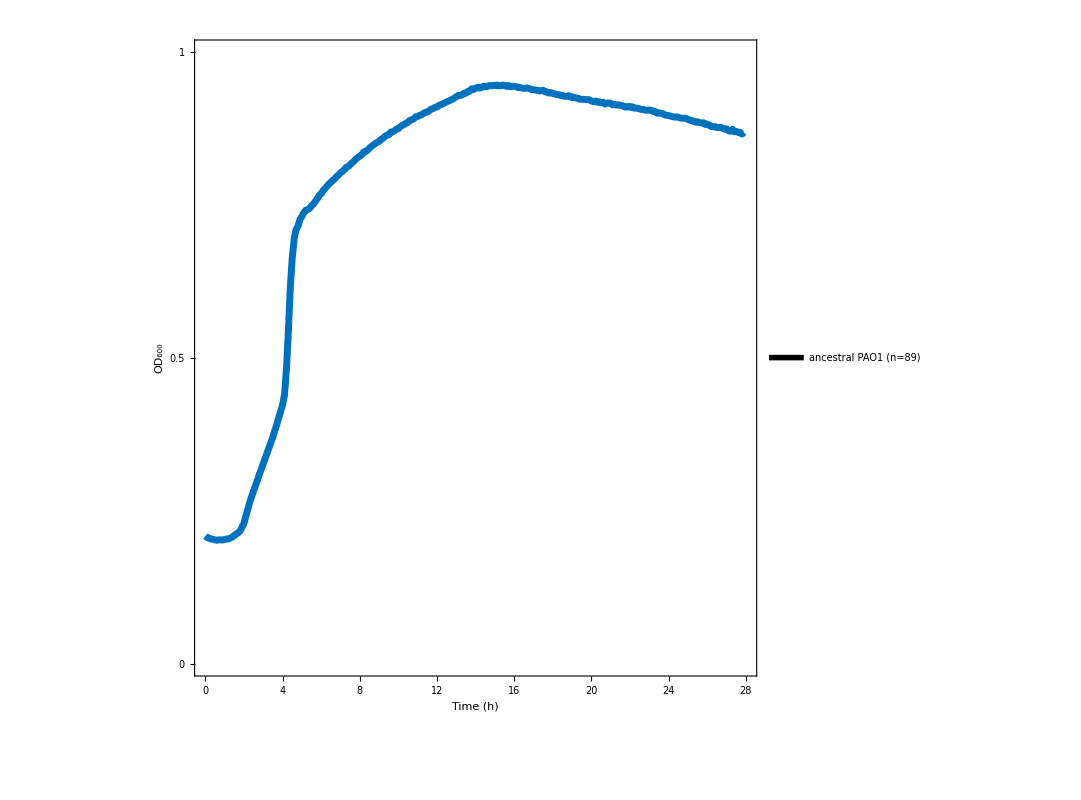

```mathematica
Legended[ListLinePlot[bacteriaControl,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->None,
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->None,
FrameStyle->{{{Black,Bold,AbsoluteThickness[3]},None},{{Black,Bold,AbsoluteThickness[3]},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},FrameLabel->{"Time (h)","OD_600"}],
Placed[SwatchLegend[{matlabColors[[1]]},
{StringForm["ancestral PAO1 (n=``)",Length[Select[controlfitdata,#[[1]]==0&]]]},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->50}],
{{0.1,0.1},{0,0}}]]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PAO1_data.png",Legended[ListLinePlot[bacteriaControl,
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},FrameLabel->{"Time (h)","OD_600"}],
Placed[SwatchLegend[{matlabColors[[1]]},
{StringForm["ancestral PAO1 (n=``)",Length[Select[controlfitdata,#[[1]]==0&]]]},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50}],
{{0.05,0.01},{0,0}}]
]]
```

C:\Users\zhiyu\Desktop\phage figures\PAO1_data.png

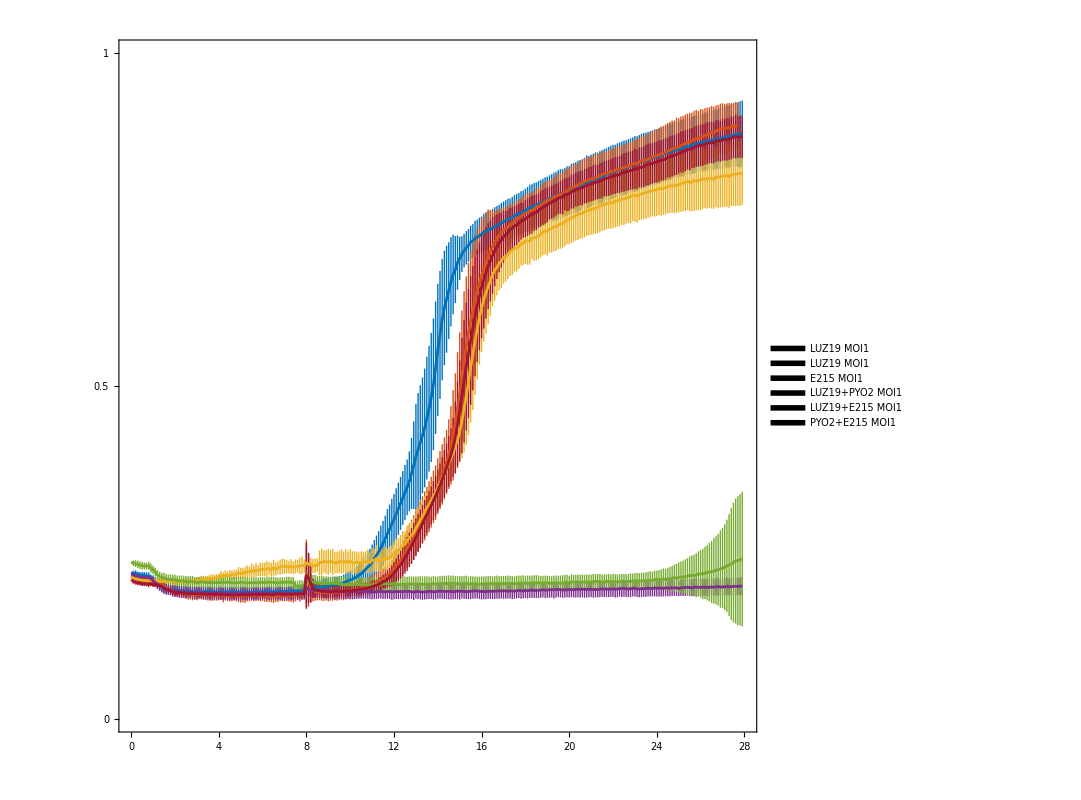

```mathematica
Legended[ListLinePlot[{luz19Moi1,pyo2Moi1,e215Moi1,luz19pyo2Moi1,luz19e215Moi1,pyo2e215Moi1},
PlotRange->{{0,28},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[2]},{matlabColors[[2]],AbsoluteThickness[2]},{matlabColors[[3]],AbsoluteThickness[2]},{matlabColors[[4]],AbsoluteThickness[2]},{matlabColors[[5]],AbsoluteThickness[2]},{matlabColors[[6]],AbsoluteThickness[2]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->None,
FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}}
],
Placed[SwatchLegend[{matlabColors[[1]],matlabColors[[2]],matlabColors[[3]],matlabColors[[4]],matlabColors[[5]],matlabColors[[6]]},
{"LUZ19 MOI1", "LUZ19 MOI1","E215 MOI1","LUZ19+PYO2 MOI1", "LUZ19+E215 MOI1","PYO2+E215 MOI1"},
LegendFunction->Framed,
LegendMarkers->marker,
LegendMarkerSize->{40,20},
Spacings->0.15,
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->30}],
{{0.01,0.68},{0,0}}]
]
```

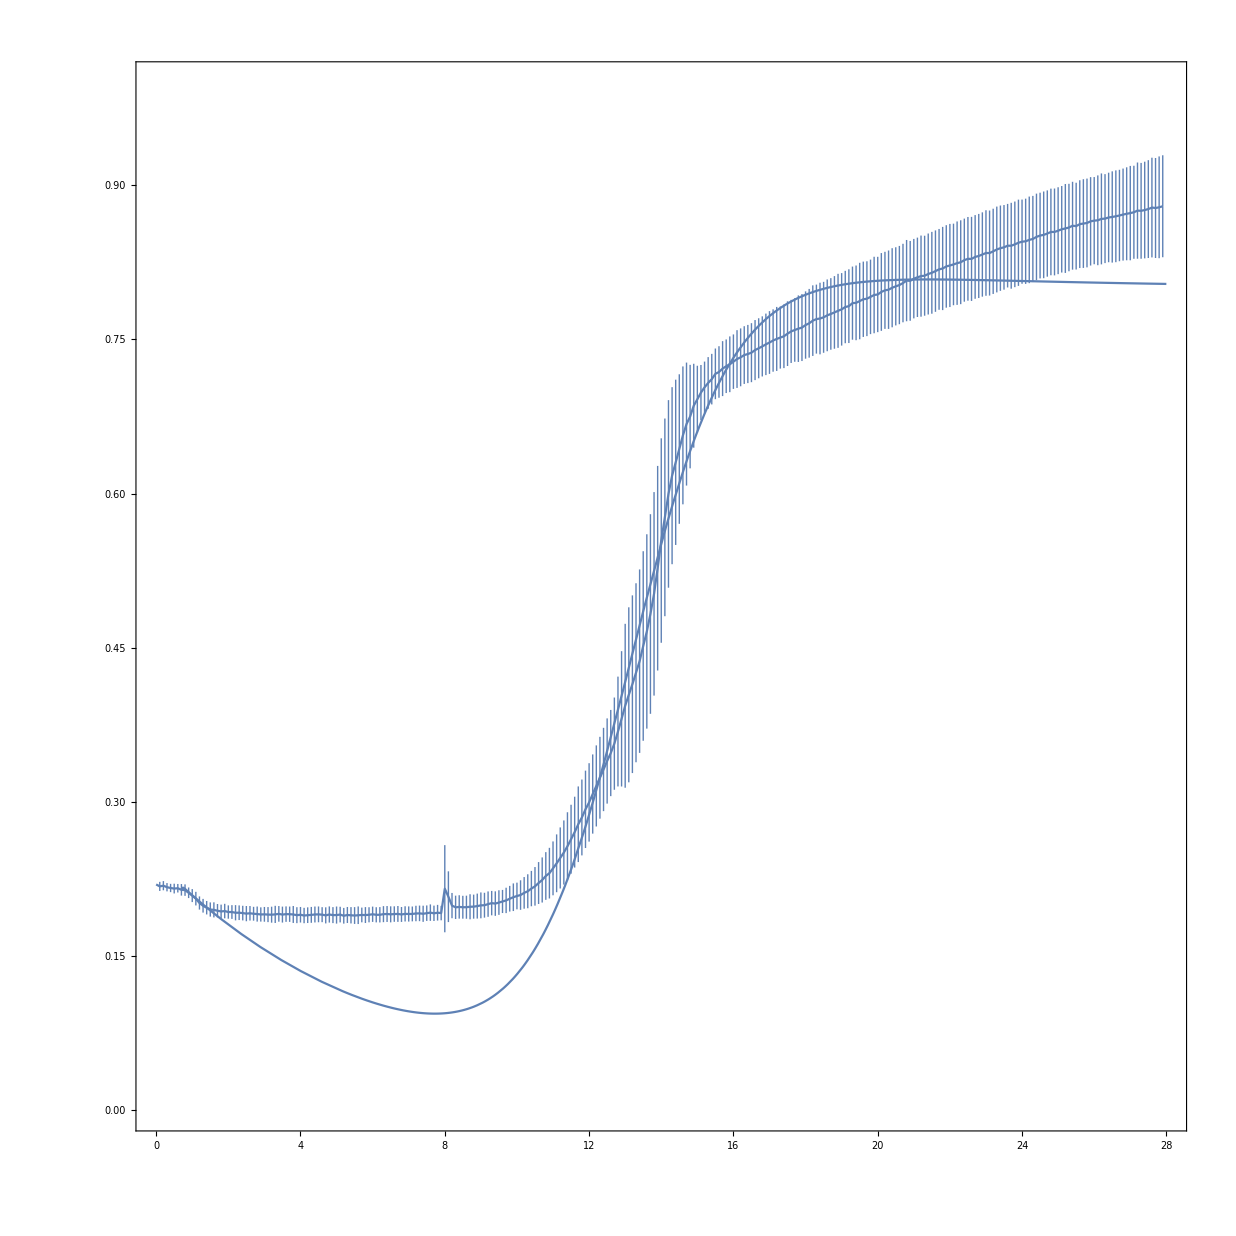

```mathematica
Show[ListLinePlot[{luz19Moi1},PlotRange->{{0,28},{0,1}}],Plot[solluz19[0.025,371,0.147,0.8],{t,luz19Moi1Lag,28},PlotRange->All],PlotRange->{{0,28},{0,1}},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

```mathematica
solluz19full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,luz19r]/.Thread[stateVar->X[t]])},X[luz19Moi1Lag]=={meanluz19Init,0,0,meanluz19Init,meanluz19Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,luz19Moi1Lag,50},{a,b,s,k}];
solluz19full=Transpose[Table[solluz19full[0.025,371.55,0.14675,0.8069],{t,luz19Moi1Lag,25,0.01}]];

solpyo2full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,100,s,0.09,pyo2r]/.Thread[stateVar->X[t]])},X[pyo2Moi1Lag]=={meanpyo2Init,0,0,meanpyo2Init,meanpyo2Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,pyo2Moi1Lag,50},{a,b,s,k}];
solpyo2full=Transpose[Table[solpyo2full[0.011875,353.902,0.1775485,0.8277],{t,pyo2Moi1Lag,25,0.01}]];

sole215full=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,200,s,0.09,e215r]/.Thread[stateVar->X[t]])},X[e215Moi1Lag]=={meane215Init,0,0,meane215Init,meane215Init}},{{t,B[t]},{t,Bi[t]},{t,Br[t]}},{t,e215Moi1Lag,50},{a,b,s,k}];
sole215full=Transpose[Table[sole215full[0.01,400,0.05056,0.710611],{t,e215Moi1Lag,25,0.01}]];
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_single.png",Show[ListLinePlot[{luz19Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[luz19MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}],
StackedListPlot[solluz19full,PlotStyle->{AbsoluteThickness[2.5]}]
]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2_single.png",Show[ListLinePlot[{pyo2Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[pyo2MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}],
StackedListPlot[solpyo2full,PlotStyle->{AbsoluteThickness[2.5]}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\E215_single.png",Show[ListLinePlot[{e215Moi1},
PlotRange->{{0,25},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,25,5}],{0,0.5,1}}],
ListLinePlot[e215MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,25},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,25,4}],{0,0.5,1}}],
StackedListPlot[sole215full,PlotStyle->{AbsoluteThickness[2.5]}]]]
```

C:\Users\zhiyu\Desktop\phage figures\LUZ19_single.png

C:\Users\zhiyu\Desktop\phage figures\PYO2_single.png

C:\Users\zhiyu\Desktop\phage figures\E215_single.png

```mathematica
gf12=Labeled[Show[ListPlot[{phageAMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"LUZ19–only–MOI1 Bacteria data"}],{0.35,0.9}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{FontFamily->"Times",Bold,35},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]])[[1;;3]]]],{t,0.8,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.22,0.7}],LabelStyle->{FontFamily->"Times"}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.22,0.5}],PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time h","Optical density OD600"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}],Style["A","Section",Bold,50,Black,FontFamily->"Times"],{{Top,Left}}]
```

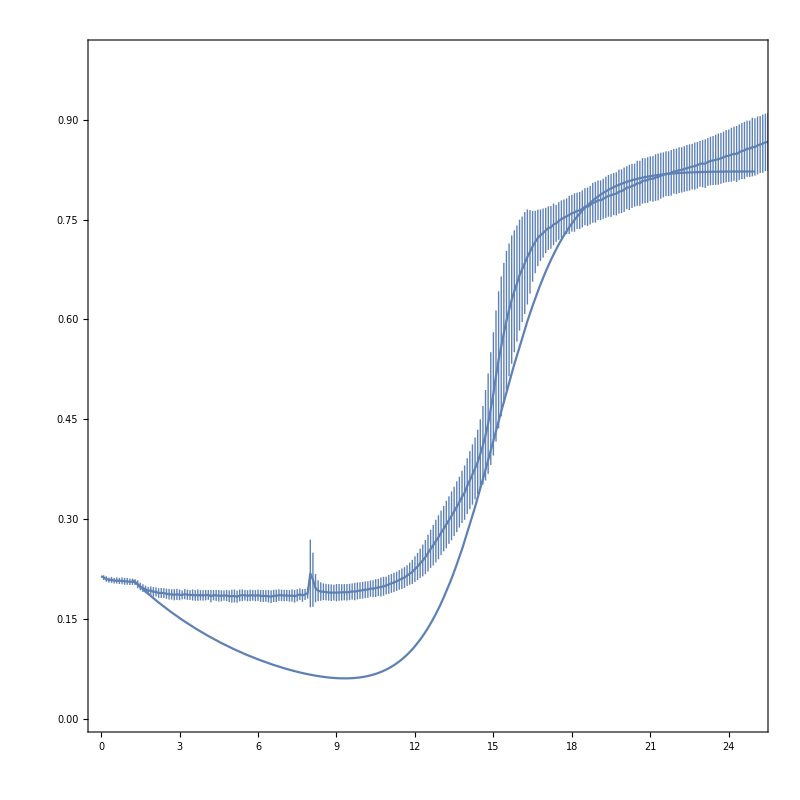

```mathematica
Show[ListLinePlot[{pyo2Moi1},PlotRange->{{0,25},{0,1}}],Plot[solpyo2[0.01,500,0.18,0.82],{t,pyo2Moi1Lag,25},PlotRange->All],PlotRange->{{0,25},{0,1}},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

```mathematica
1.1186858421841618e-5
```

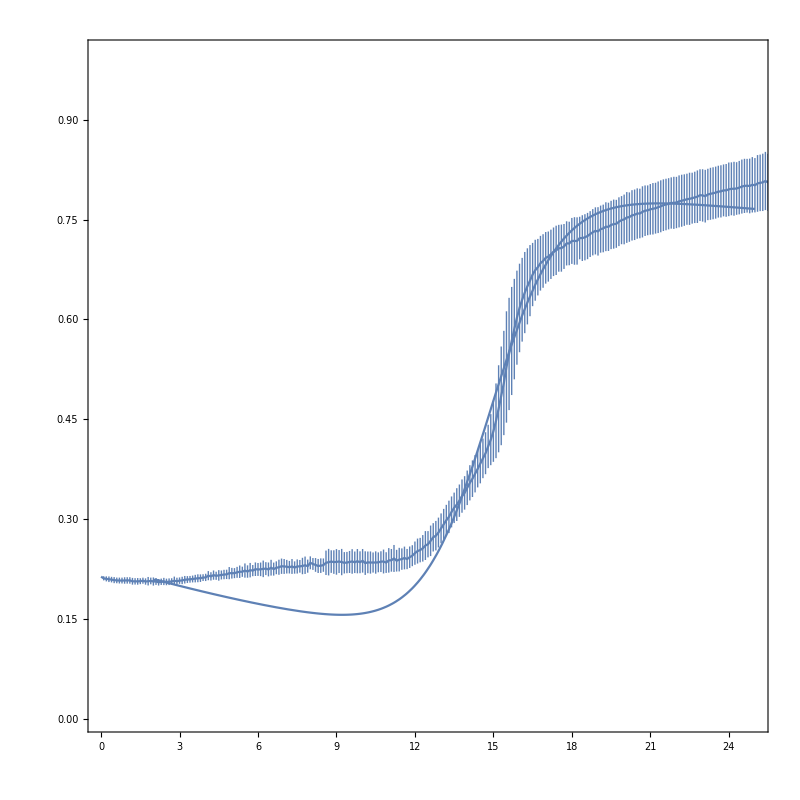

```mathematica
Show[ListLinePlot[{e215Moi1},PlotRange->{{0,25},{0,1}}],Plot[sole215[0.01,400,0.05,0.7],{t,e215Moi1Lag,25},PlotRange->All],PlotRange->{{0,25},{0,1}},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

```mathematica
DBPH[a1_,a2_,a3_,k_,b1_,b2_,h1_,h2_,ra_,rb_,rab_,s1_,s2_]={
basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B,
-s1*Bia+b1*B*Pa+b1*Bb*Pa,
-s2*Bib+b2*B*Pb+b2*Ba*Pb,
a1*B+ra*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb,
a2*B+rb*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa,
a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k),
-0.09*Pa+h1*s1*Bia-b1*B*Pa-b1*Bb*Pa,
-0.09*Pb+h2*s2*Bib-b2*B*Pb-b2*Ba*Pb,
basalr*B*(1-(B+Ba+Bb+Bab)/k)-b1*B*Pa-b2*B*Pb-a1*B-a2*B-a3*B+(-s1*Bia+b1*B*Pa+b1*Bb*Pa)+(-s2*Bib+b2*B*Pb+b2*Ba*Pb)+(a1*B+ra*Ba*(1-(B+Ba+Bb+Bab)/k)-a2*Ba-b2*Ba*Pb)+(a2*B+rb*Bb*(1-(B+Ba+Bb+Bab)/k)-a1*Bb-b1*Bb*Pa)+(a2*Ba+a1*Bb+a3*B+rab*Bab*(1-(B+Ba+Bb+Bab)/k))
};
stateVar={B,Bia,Bib,Ba,Bb,Bab,Pa,Pb,Bt};
X[t_]=Through[stateVar[t]];
meanluz19e215Init=Select[luz19e215Moi1,#[[1]]==luz19e215Moi1Lag&][[1,2,1]];
meanluz19pyo2Init=Select[luz19pyo2Moi1,#[[1]]==luz19pyo2Moi1Lag&][[1,2,1]];
solluz19pyo2=ParametricNDSolveValue[{{X'[t]==(DBPH[a1,a2,a3,k,b,b,100,100,luz19r,pyo2r,luz19pyo2r,s1,s2]/.Thread[stateVar->X[t]])},X[luz19pyo2Moi1Lag]=={meanluz19pyo2Init,0,0,0,0,0,meanluz19pyo2Init/2,meanluz19pyo2Init/2,meanluz19pyo2Init}},Bt[t],{t,luz19pyo2Moi1Lag,50},{a3,k,s1,s2,b,a1,a2}];
solluz19pyo2full=ParametricNDSolveValue[{{X'[t]==(DBPH[0.025,0.0119,1.12*10^-5,k,382,382,100,100,luz19r,pyo2r,luz19pyo2r,0.147,0.178]/.Thread[stateVar->X[t]])},X[luz19pyo2Moi1Lag]=={meanluz19pyo2Init,0,0,0,0,0,meanluz19pyo2Init/2,meanluz19pyo2Init/2,meanluz19pyo2Init}},{{t,B[t]},{t,Bia[t]+Bib[t]},{t,Ba[t]+Bb[t]},{t,Bab[t]}},{t,luz19pyo2Moi1Lag,50},{k}];
solluz19e215=ParametricNDSolveValue[{{X'[t]==(DBPH[a1,a2,a3,k,b,b,100,200,luz19r,e215r,luz19e215r,s1,s2]/.Thread[stateVar->X[t]])},X[luz19e215Moi1Lag]=={meanluz19e215Init,0,0,0,0,0,meanluz19e215Init/2,meanluz19e215Init/2,meanluz19e215Init}},Bt[t],{t,luz19e215Moi1Lag,50},{a3,k,s1,s2,b,a1,a2}];
solluz19e215full=ParametricNDSolveValue[{{X'[t]==(DBPH[0.025,0.0119,1.12*10^-5,k,382,382,100,200,luz19r,e215r,luz19e215r,0.147,0.0506]/.Thread[stateVar->X[t]])},X[luz19e215Moi1Lag]=={meanluz19e215Init,0,0,0,0,0,meanluz19e215Init/2,meanluz19e215Init/2,meanluz19e215Init}},{{t,B[t]},{t,Bia[t]+Bib[t]},{t,Ba[t]+Bb[t]},{t,Bab[t]}},{t,luz19e215Moi1Lag,50},{k}];

DBPH[a_,k_,b_,s1_,s2_]={basalr*B*(1-(B+Br)/k)-b*B*Pa-b*B*Pb-a*B,-s1*Bia+b*B*Pa,-s2*Bib+b*B*Pb,a*B+pyo2r*Br*(1-(B+Br)/k),-0.09*Pa+100*s1*Bia-b*B*Pa,-0.09*Pb+200*s2*Bib-b*B*Pb,basalr*B*(1-(B+Br)/k)-b*B*Pa-b*B*Pb-a*B-s1*Bia+b*B*Pa-s2*Bib+b*B*Pb+a*B+pyo2r*Br*(1-(B+Br)/k)};
stateVar={B,Bia,Bib,Br,Pa,Pb,Bt};
X[t_]=Through[stateVar[t]];
meanpyo2e215Init=Select[pyo2e215Moi1,#[[1]]==pyo2e215Moi1Lag&][[1,2,1]];
solpyo2e215=ParametricNDSolveValue[{{X'[t]==(DBPH[a,k,b,s1,s2]/.Thread[stateVar->X[t]])},X[pyo2e215Moi1Lag]=={meanpyo2e215Init,0,0,0,meanpyo2e215Init/2,meanpyo2e215Init/2,meanpyo2e215Init}},Bt[t],{t,pyo2e215Moi1Lag,50},{a,k,b,s1,s2}];
solpyo2e215full=ParametricNDSolveValue[{{X'[t]==(DBPH[a,k,b,s1,s2]/.Thread[stateVar->X[t]])},X[pyo2e215Moi1Lag]=={meanpyo2e215Init,0,0,0,meanpyo2e215Init/2,meanpyo2e215Init/2,meanpyo2e215Init}},{{t,B[t]},{t,Bia[t]+Bib[t]},{t,Br[t]}},{t,pyo2e215Moi1Lag,50},{a,k,b,s1,s2}];
```

```mathematica
solpyo2e215full=Transpose[Table[solpyo2e215full[0.011875,0.8,353.902,0.1775485,0.0506],{t,pyo2e215Moi1Lag,27,0.01}]];
solluz19pyo2full=Transpose[Table[solluz19pyo2full[0.22],{t,luz19pyo2Moi1Lag,27,0.01}]];
solluz19e215full=Transpose[Table[solluz19e215full[0.22],{t,luz19e215Moi1Lag,27,0.01}]];
```

```mathematica
pyo2e215boot=Replace[Transpose[{pyo2Boot[[2;;,1]],pyo2Boot[[2;;,2]],pyo2Boot[[2;;,3]],e215Boot[[2;;,3]]}],{x_,y_,z_,m_}->{x,0.8,y,z,m},{1}];
pyo2e215sol=Apply[solpyo2e215,pyo2e215boot,{1}];
solpyo2e215bootDiscrete=Map[pyo2e215sol/. {t->#}&,timeSamplepyo2e215,{1}];
pyo2e215Mean=Map[Mean[#]&,solpyo2e215bootDiscrete];
pyo2e215Mean=Transpose[{timeSamplepyo2e215,pyo2e215Mean}];
pyo2e215CI=Map[Quantile[#,{0.025,0.975}]&,solpyo2e215bootDiscrete];
pyo2e215ciwidth=pyo2e215CI[[All,2]]-pyo2e215CI[[All,1]];
pyo2e215moi1=Replace[Select[pyo2e215Moi1fitdata,pyo2e215Moi1Lag<=#[[1]]<=27&],{x_,y_,z_}->{x,z},{1}];
pyo2e215SEwidth={};
Module[{i,t,y,ys},For[i=1,i<=Length[pyo2e215Mean],i++,t=pyo2e215Mean[[i,1]];
y=pyo2e215Mean[[i,2]];
pyo2e215SEwidth=Append[pyo2e215SEwidth,StandardDeviation[Select[pyo2e215moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];]];
pyo2e215MeanPI=Table[{pyo2e215Mean[[i]][[1]],Around[pyo2e215Mean[[i]][[2]],pyo2e215ciwidth[[i]]+pyo2e215SEwidth[[i]]]},{i,1,Length[pyo2e215Mean]}];

nsamples=950;
luz19e215boot=Replace[Transpose[{luz19e215Boot[[2;;nsamples,1]],luz19Boot[[2;;nsamples,3]],e215Boot[[2;;nsamples,3]],luz19Boot[[2;;nsamples,2]],luz19Boot[[2;;nsamples,1]],e215Boot[[2;;nsamples,1]]}],{x_,y_,z_,a_,b_,c_}->{x,0.22,y,z,a,b,c},{1}];
luz19e215sol=Apply[solluz19e215,luz19e215boot,{1}];
solluz19e215bootDiscrete=Map[luz19e215sol/. {t->#}&,timeSampleluz19e215,{1}];
luz19e215Mean=Map[Mean[#]&,solluz19e215bootDiscrete];
luz19e215Mean=Transpose[{timeSampleluz19e215,luz19e215Mean}];
luz19e215CI=Map[Quantile[#,{0.025,0.975}]&,solluz19e215bootDiscrete];
luz19e215ciwidth=luz19e215CI[[All,2]]-luz19e215CI[[All,1]];
luz19e215moi1=Replace[Select[luz19e215Moi1fitdata,luz19e215Moi1Lag<=#[[1]]<=27&],{x_,y_,z_}->{x,z},{1}];
luz19e215SEwidth={};
Module[{i,t,y,ys},For[i=1,i<=Length[luz19e215Mean],i++,t=luz19e215Mean[[i,1]];
y=luz19e215Mean[[i,2]];
luz19e215SEwidth=Append[luz19e215SEwidth,StandardDeviation[Select[luz19e215moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];]];
luz19e215MeanPI=Table[{luz19e215Mean[[i]][[1]],Around[luz19e215Mean[[i]][[2]],luz19e215ciwidth[[i]]+luz19e215SEwidth[[i]]]},{i,1,Length[luz19e215Mean]}];

nsamples=950;
luz19pyo2boot=Replace[Transpose[{luz19e215Boot[[2;;nsamples,1]],luz19Boot[[2;;nsamples,3]],pyo2Boot[[2;;nsamples,3]],luz19Boot[[2;;nsamples,2]],luz19Boot[[2;;nsamples,1]],pyo2Boot[[2;;nsamples,1]]}],{x_,y_,z_,a_,b_,c_}->{x,0.22,y,z,a,b,c},{1}];
luz19pyo2sol=Apply[solluz19pyo2,luz19pyo2boot,{1}];
solluz19pyo2bootDiscrete=Map[luz19pyo2sol/. {t->#}&,timeSampleluz19pyo2,{1}];
luz19pyo2Mean=Map[Mean[#]&,solluz19pyo2bootDiscrete];
luz19pyo2Mean=Transpose[{timeSampleluz19pyo2,luz19pyo2Mean}];
luz19pyo2CI=Map[Quantile[#,{0.025,0.975}]&,solluz19pyo2bootDiscrete];
luz19pyo2ciwidth=luz19pyo2CI[[All,2]]-luz19pyo2CI[[All,1]];
luz19pyo2moi1=Replace[Select[luz19pyo2Moi1fitdata,luz19pyo2Moi1Lag<=#[[1]]<=27&],{x_,y_,z_}->{x,z},{1}];
luz19pyo2SEwidth={};
Module[{i,t,y,ys},For[i=1,i<=Length[luz19pyo2Mean],i++,t=luz19pyo2Mean[[i,1]];
y=luz19pyo2Mean[[i,2]];
luz19pyo2SEwidth=Append[luz19pyo2SEwidth,StandardDeviation[Select[luz19pyo2moi1,#[[1]]==t&][[All,2]]]*InverseCDF[NormalDistribution[0,1],0.975]];]];
luz19pyo2MeanPI=Table[{luz19pyo2Mean[[i]][[1]],Around[luz19pyo2Mean[[i]][[2]],luz19pyo2ciwidth[[i]]+luz19pyo2SEwidth[[i]]]},{i,1,Length[luz19pyo2Mean]}];
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2_E215_double.png",Show[ListLinePlot[{pyo2e215Moi1},
PlotRange->{{0,27},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
ListLinePlot[pyo2e215MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,27},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Bold,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
StackedListPlot[solpyo2e215full,PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.922526, 0.385626, 0.209179]},PlotStyle->{AbsoluteThickness[2.5]}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_PYO2_double.png",Show[ListLinePlot[{luz19pyo2Moi1},
PlotRange->{{0,27},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
ListLinePlot[luz19pyo2MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,27},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
StackedListPlot[solluz19pyo2full,PlotStyle->{AbsoluteThickness[2.5]}]]]

Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_E215_double.png",Show[ListLinePlot[{luz19e215Moi1},
PlotRange->{{0,27},{0,1}},
PlotStyle->{{matlabColors[[1]],AbsoluteThickness[5]}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->50},
FrameLabel->{"Time (h)","OD_600"},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
ListLinePlot[luz19e215MeanPI,
IntervalMarkers->"Bands",
PlotStyle->{{Red,AbsoluteThickness[5],Dashed}},
PlotRange->{{0,27},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
BaseStyle->{Normal,25},
GridLines->None,
FrameStyle->{{{Black,Normal,AbsoluteThickness[3]},None},{{Black,Normal,AbsoluteThickness[3]},None}},
LabelStyle->{Normal,Black,FontFamily->"Arial",FontSize->40},
FrameTicks->{Table[i,{i,0,27,3}],{0,0.5,1}}],
StackedListPlot[solluz19e215full,PlotStyle->{AbsoluteThickness[2.5]}]]]
```

C:\Users\zhiyu\Desktop\phage figures\PYO2_E215_double.png

C:\Users\zhiyu\Desktop\phage figures\LUZ19_PYO2_double.png

C:\Users\zhiyu\Desktop\phage figures\LUZ19_E215_double.png

```mathematica
solpyo2e215full
```

$Aborted

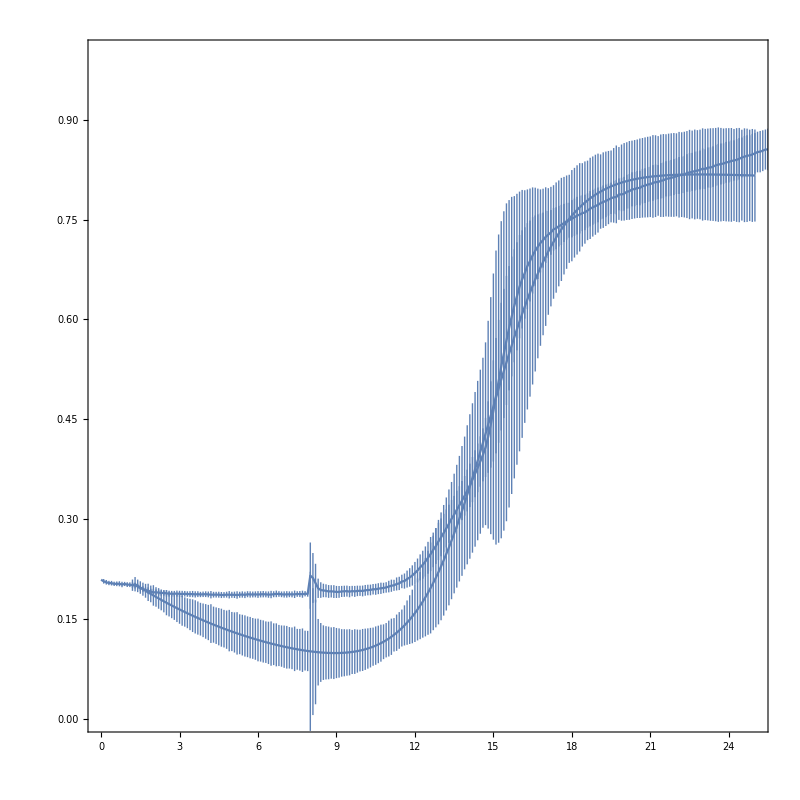

```mathematica
Show[ListLinePlot[{pyo2e215Moi1},PlotRange->{{0,25},{0,1}}],ListLinePlot[pyo2e215MeanPI],PlotRange->{{0,25},{0,1}},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

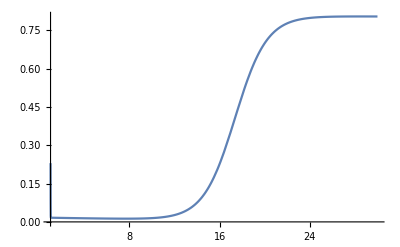

```mathematica
Show[Plot[pyo2e215sol[[1]],{t,pyo2e215Moi1Lag,30}]]
```

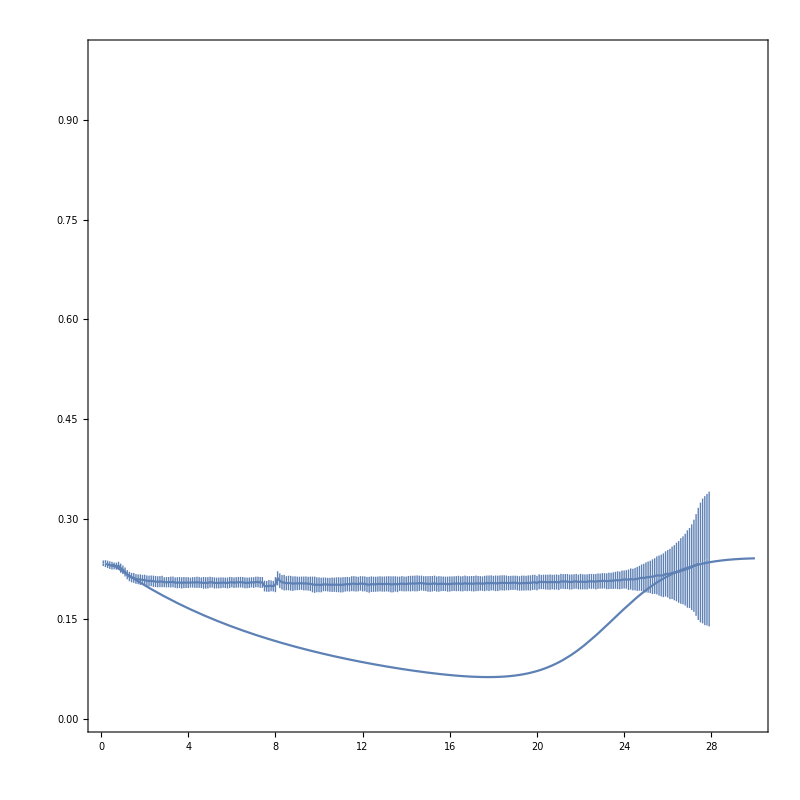

```mathematica
Show[ListLinePlot[luz19e215Moi1],Plot[solluz19e215[1.1*10^-5,0.218],{t,luz19e215Moi1Lag,30}],PlotRange->{{0,30},{0,1}},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

```mathematica
(* Initial bacteria values *)
(* I will fit all MOIs simultaneously as MOI affects binding rate *)
(* Initial condition will vary between different sample, but using different initial for different samples run super slow, so I will use average *)
(* Unable to change the delay time, manually remove delay period *)
PH[a_,k_,b_,h_,s_,p_,rr_]={basalr*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rr*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,basalr*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rr*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
sol=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p,rr]/.Thread[stateVar->X[t]])},X[0]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,50},{a,k,b,h,s,p,B0,MOI,rr}];
(* burst size will be assumed *)
model[a_,k_,b_,h_,s_,p_,MOI_,t_,rr_,B0_]=sol[a,k,b,h,s,p,B0,MOI,rr][t];
```

```mathematica
(* LUZ19 *)
fitModelluz19=NonlinearModelFit[beginluz19,{model[a,k,b,100,s,0.09,moi,t,luz19r,luz19INI],100>b>0,0.5>s>0,1.5>k>0,0.1>a>0},{{b,50},{s,0.3},{k,1},{a,0.01}},{t,moi}];
(* PYO2 *)
fitModelpyo2=NonlinearModelFit[beginpyo2,{model[a,k,b,100,s,0.09,moi,t,pyo2r,pyo2INI],100>b>0,0.5>s>0,1.5>k>0,0.1>a>0},{{b,50},{s,0.3},{k,1}},{t,moi}];
(* E215 *)
fitModele215=NonlinearModelFit[begine215,{model[a,k,b,200,s,0.09,moi,t,e215r,e215INI],100>b>0,0.5>s>0,1.5>k>0,0.1>a>0},{{b,50},{s,0.3},{k,1}},{t,moi}];
```

$Aborted

```mathematica
beginluz19
```

```mathematica
fitModelluz19=NonlinearModelFit[beginluz19,{model[a,k,b,100,s,0.09,moi,t,luz19r,luz19INI],100>b>0,0.5>s>0,1.5>k>0,0.1>a>0},{{b,50},{s,0.3},{k,1},{a,0.01}},{t,moi},WorkingPrecision->5];
```

NonlinearModelFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (5).

NonlinearModelFit::precw: The precision of the data and model function ({{0.1>a,0.5>s,1.5>k,100>b,a>0,b>0,k>0,s>0}}) is less than the specified WorkingPrecision (5.).

```mathematica
fitModelluz19[[1]]
```

{Nonlinear,{b→50.,s→0.29845,k→0.996307,a→0.00342178},{{t,moi},{ParametricFunction[<>][a,k,b,100,s,0.09,0.215353,moi,0.716094][t],100>b>0,0.5>s>0,1.5>k>0,0.1>a>0}}}

```mathematica
model[0.05,1,50,100,0.1,0.09,10,t,luz19r,luz19INI]
```

InterpolatingFunction[…][t]

```mathematica
fitModelluz19=NonlinearModelFit[beginluz19,{model[a,k,b,100,s,0.09,moi,t,luz19r,luz19INI],100>b>0,1>s>0,1.5>k>0,1>a>0},{{b,50},{s,0.3},{k,1},{a,0.01}},{t,moi},MaxIterations->100]
```

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{},{ParametricFunction[<>][a,k,b,100,s,0.09,Mean[{}],moi,0.716094][t],100>b>0,1>s>0,1.5>k>0,1>a>0},{{b,50},{s,0.3},{k,1},{a,0.01}},{t,moi},MaxIterations→100]

```mathematica
(* Initial bacteria values *)
(* I will fit all MOIs simultaneously as MOI affects binding rate *)
(* Initial condition will vary between different sample *)
(* Unable to change the delay time, manually remove delay period *)
luz19MOI1INI=Select[luz19Moi1,0.7==#[[1]]&][[1,2]];
pyo2MOI1INI=Select[pyo2Moi1,1.3==#[[1]]&][[1,2]];
e215MOI1INI=Select[e215Moi1,2.5==#[[1]]&][[1,2]];
PH[a_,k_,b_,h_,s_,p_,rr_]={basalr*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rr*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,basalr*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rr*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
beginluz19=Select[luz19Moi1fitdata,0.7<=#[[1]]≤1.2&];
beginpyo2=Select[pyo2Moi1fitdata,1.3<=#[[1]]≤1.7&];
begine215=Select[e215Moi1fitdata,2.5<=#[[1]]≤3&];
allfit=Join[beginluz19,beginpyo2,begine215];
(* LUZ19 *)
sol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p,rr]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0.7,50},{a,k,b,h,s,p,B0,MOI,rr}];
(* PYO2 *)
sol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p,rr]/.Thread[stateVar->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,1.3,50},{a,k,b,h,s,p,B0,MOI,rr}];
(* E215 *)
sol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p,rr]/.Thread[stateVar->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,2.5,50},{a,k,b,h,s,p,B0,MOI,rr}];
model[a_,k_,b_,s1_,s2_,s3_,p_,phage_,MOI_,t_,rr_,B0luz_,B0pyo_,B0e_]=Piecewise[{{sol1[a,k,b,100,s1,p,B0luz,MOI,rr],phage==1&&t>=0.7},{sol2[a,k,b,100,s2,p,B0pyo,MOI,rr],phage==2&&t>=1.3},{sol3[a,k,b,200,s3,p,B0e,MOI,rr],phage==3&&t>=2.5}},#*0&][t];
fitModel1=NonlinearModelFit[beginluz19,{model[0,1,b,s1,0,0,0.09,phage,1,t,basalr,luz19MOI1INI[[1]],pyo2MOI1INI[[1]],e215MOI1INI[[1]]],50>b>0,s1>0},{b,s1},{t,phage}];
fitModel2=NonlinearModelFit[beginpyo2,{model[0,1,b,0,s2,0,0.09,phage,1,t,basalr,luz19MOI1INI[[1]],pyo2MOI1INI[[1]],e215MOI1INI[[1]]],50>b>0,s2>0},{b,s2},{t,phage}];
fitModel3=NonlinearModelFit[begine215,{model[0,1,b,0,0,s3,0.09,phage,1,t,basalr,luz19MOI1INI[[1]],pyo2MOI1INI[[1]],e215MOI1INI[[1]]],50>b>0,s3>0},{b,s3},{t,phage}];
```

```mathematica
luz19s=fitModel1[[1,2]][[2,2]];
pyo2s=fitModel2[[1,2]][[2,2]];
e215s=fitModel3[[1,2]][[2,2]];
bjoin=(fitModel1[[1,2]][[1,2]]+fitModel2[[1,2]][[1,2]]+fitModel3[[1,2]][[1,2]])/3;
```

```mathematica
bjoin
```

49.9983

```mathematica
soltest=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p,rr]/.Thread[stateVar->X[t]])},X[0]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,50},{a,k,b,h,s,p,B0,MOI,rr}];
```

```mathematica
luz1
```

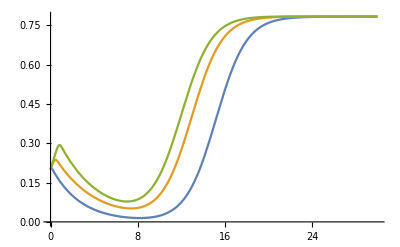

```mathematica
Plot[Evaluate[{soltest[0.00124,0.7832,8,100,0.38,0.09,0.2,10,luz19r][t],soltest[0.00124,0.7832,8,100,0.2715,0.09,0.2,1,luz19r][t],soltest[0.00124,0.7832,8,100,0.2715,0.09,0.2,0.1,luz19r][t]}],{t,0,30}]
```

```mathematica
model[0.017,1,bjoin,luz19s,pyo2s,e215s,0.09,1,1,t]
```

model[0.017,1,458.89,0.149805,0.201184,0.0316079,0.09,1,1,t]

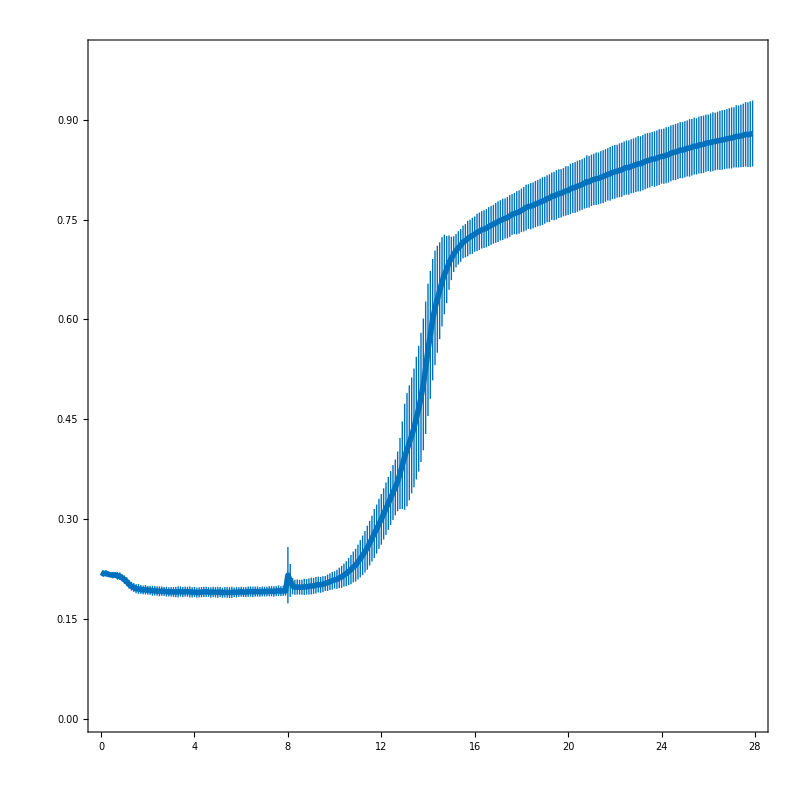

```mathematica
ListLinePlot[{luz19Moi1},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}]
```

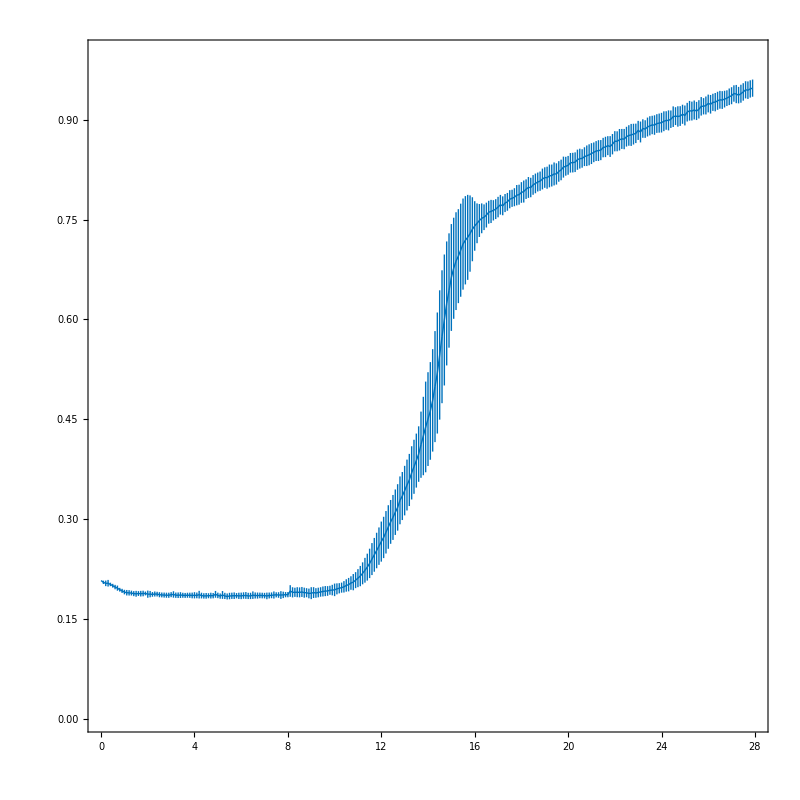

```mathematica
Show[ListLinePlot[{luz19Moi10},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[1],AbsoluteThickness[1],AbsoluteThickness[1]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}],Plot[Evaluate[model[0.017,0.95,bjoin,luz19s,pyo2s,e215s,0.09,1,10,t,0.76]],{t,0.7,27.9}]]
```

```mathematica
pyo2s
```

0.321624

```mathematica
a,k,b,h,s,p,B0,MOI,rr
```

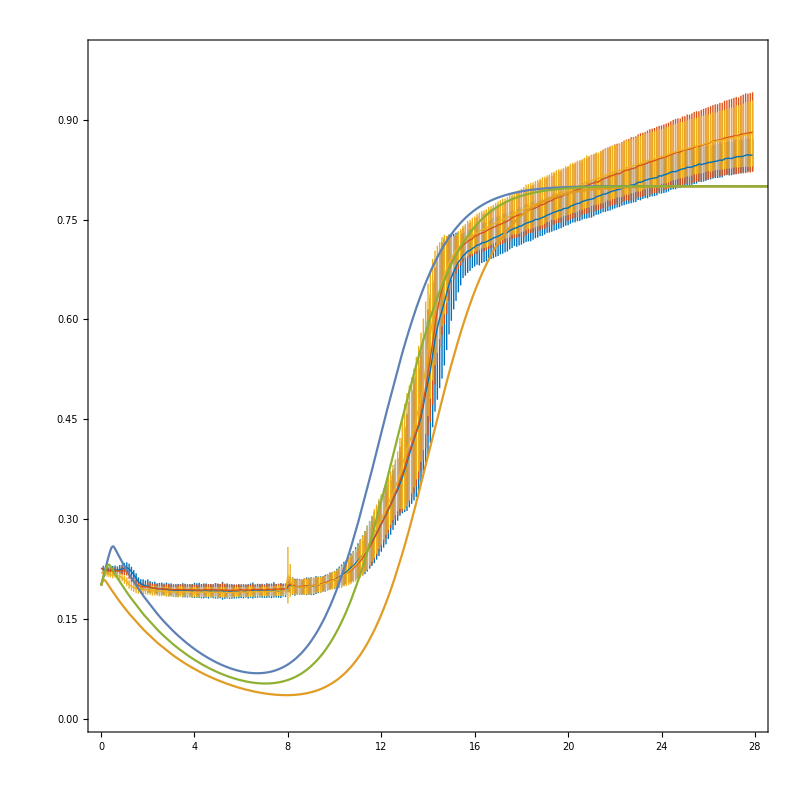

```mathematica
Show[ListLinePlot[{luz19Moi001,luz19Moi01,luz19Moi1},PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},LegendFunction->Framed,LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.77,0.3}],PlotTheme->"Detailed",BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[1],AbsoluteThickness[1],AbsoluteThickness[1]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},PlotRange->{{0,28},{0,1}},ImageSize->800,IntervalMarkers->"Fences",AspectRatio->1,Frame->{True,True,False,False}],Plot[Evaluate[{soltest[0.002,0.8,50,100,0.27,0.09,0.2,0.01,luz19r][t],soltest[0.002,0.8,50,100,0.27,0.09,0.2,1,luz19r][t],soltest[0.002,0.8,50,100,0.27,0.09,0.2,0.1,luz19r][t]}],{t,0,30}]]
```

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19.png",ListLinePlot[{luz19Moi001,luz19Moi01,luz19Moi1,luz19Moi10},
PlotLegends->Placed[LineLegend[{"LUZ19 MOI0.01","LUZ19 MOI0.1","LUZ19 MOI1","LUZ19 MOI10"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.75,0.15}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},
GridLines->None,
PlotStyle->Transpose[{matlabColors[[1;;4]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
Frame->{True,True,False,False}]]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2.png",ListLinePlot[{pyo2Moi001,pyo2Moi01,pyo2Moi1,pyo2Moi10},
PlotLegends->Placed[LineLegend[{"PYO2 MOI0.01","PYO2 MOI0.1","PYO2 MOI1","PYO2 MOI10"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.75,0.15}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;4]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
Frame->{True,True,False,False}]]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\E215.png",ListLinePlot[{e215Moi001,e215Moi01,e215Moi1,e215Moi10},
PlotLegends->Placed[LineLegend[{"E215 MOI0.01","E215 MOI0.1","E215 MOI1","E215 MOI10"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.75,0.15}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},
GridLines->None,
PlotStyle->Transpose[{matlabColors[[1;;4]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
AspectRatio->1,
Frame->{True,True,False,False}]]
```

C:\Users\zhiyu\Desktop\phage figures\LUZ19.png

C:\Users\zhiyu\Desktop\phage figures\PYO2.png

C:\Users\zhiyu\Desktop\phage figures\E215.png

```mathematica
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_PYO2.png",ListLinePlot[{luz19pyo2Moi001,luz19pyo2Moi01,luz19pyo2Moi1},
PlotLegends->Placed[LineLegend[{"LUZ19+PYO2 MOI0.01","LUZ19+PYO2 MOI0.1","LUZ19+PYO2 MOI1"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.4,0.4}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},
GridLines->None,
PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
Frame->{True,True,False,False}]]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\LUZ19_E215.png",ListLinePlot[{luz19e215Moi001,luz19e215Moi01,luz19e215Moi1},
PlotLegends->Placed[LineLegend[{"LUZ19+E215 MOI0.01","LUZ19+E215 MOI0.1","LUZ19+E215 MOI1"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.4,0.4}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},GridLines->None,PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->40},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
AspectRatio->1,
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
Frame->{True,True,False,False}]]
Export["C:\\Users\\zhiyu\\Desktop\\phage figures\\PYO2_E215.png",ListLinePlot[{pyo2e215Moi001,pyo2e215Moi01,pyo2e215Moi1},
PlotLegends->Placed[LineLegend[{"PYO2+E215 MOI0.01","PYO2+E215 MOI0.1","PYO2+E215 MOI1"},
LegendFunction->Framed,
LegendMarkerSize->{40,20},
LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,0.1]&)],{0.75,0.2}],
PlotTheme->"Detailed",
BaseStyle->{Bold,25},
GridLines->None,
PlotStyle->Transpose[{matlabColors[[1;;3]],{AbsoluteThickness[4],AbsoluteThickness[4],AbsoluteThickness[4]}}],FrameStyle->{{{Black,Bold,Thick},{Black,Bold}},{{Black,Bold,Thick},None}},
LabelStyle->{Bold,Black,FontFamily->"Arial",FontSize->30},
PlotRange->{{0,28},{0,1}},
ImageSize->800,
IntervalMarkers->"Fences",
FrameTicks->{Table[i,{i,0,28,4}],{0,0.5,1}},
AspectRatio->1,
Frame->{True,True,False,False}]]
```

C:\Users\zhiyu\Desktop\phage figures\LUZ19_PYO2.png

C:\Users\zhiyu\Desktop\phage figures\LUZ19_E215.png

C:\Users\zhiyu\Desktop\phage figures\PYO2_E215.png

```mathematica
(* Models for different MOI, used to estimate b, h, s, and p *)
PH[a_,k_,b_,h_,s_,p_]={basalr*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+basalr*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,basalr*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+basalr*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
sol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.4]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
model1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol1[a,k,b,h,s,p,B0,MOI][t]
model2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol2[a,k,b,h,s,p,B0,MOI][t]
model3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
controlTime=Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[4,2;;]][[1;;280]];
controlData=Transpose[Import["C:\\Users\\zhiyu\\Desktop\\20220223_RoachLabPhageData_TL.xlsx"][[2]][[5;;93,2;;]]][[1;;280,All]];
stds=Map[StandardDeviation[#]&,controlData];
means=Map[Mean[#]&,controlData];
bacteriaControl=Apply[Around,Transpose[{means,stds}],{1}];
bacteriaControl=Transpose[{controlTime,bacteriaControl}];
controlfitdata=Apply[Join,Table[Map[{controlTime[[i]],#}&,controlData[[i]]],{i,1,Length[controlTime]}]];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[bacteriaControl,#[[1]]==3.5&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
para=NonlinearModelFit[Select[controlfitdata,#[[1]]≥3.5&],{germGrowth[k,r,t]},{{k,0.9},{r,0.87}},t]
basalr=para[[1,2]][[2,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FittedModel[(0.906235 ⅇ^(0.880031 t))/(31.3865+1. ⅇ^(0.880031 t))]

0.880031

```mathematica
germGrowth[k_,r_,p_,t_]=NDSolve[{{y'[t]==r *y[t](1-y[t]/k)},y[3.5]==Select[bacteriaControl,#[[1]]==3.5&][[1,2]][[1]]} ,y[t],t][[1,1,2]];
```

NDSolve::ndlim: Range specification t is not of the form {x, xend} or {x, xmin, xmax}.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 3.5.

```mathematica
sol=ParametricNDSolveValue[{y'[t]==r *y[t]*(1-y[t]/(k-c*y[t])),y[0]==0.2} ,y,{t,0,40},{r,k,c}]
```

ParametricFunction[<>]

```mathematica
sol[0.8,1,0.1][t]
```

InterpolatingFunction[…][t]

```mathematica
Remove[germGrowth]
```

```mathematica
germGrowth[k_,r_,t_]:=sol[r,k][t]
```

```mathematica
para=NonlinearModelFit[controlfitdata,{germGrowth[k,r,p,t]},{{k,0.9},{r,0.1},{p,0.1}},t]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[InterpolatingFunction[…][t]]

```mathematica
sol[1,1,1][4.217]
```

0.111057

```mathematica
controlfitdata
```

```mathematica
Normal[para]
```

InterpolatingFunction[…][t]

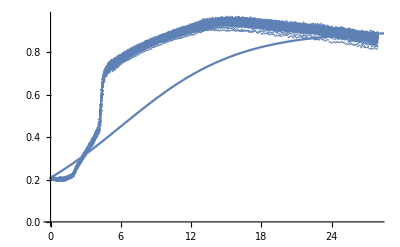

```mathematica
Show[ListPlot[controlfitdata],Plot[germGrowth[0.9,0.2,0,t],{t,0,30}]]
```

```mathematica
germGrowth[1,0.5,t]
```

germGrowth[1,0.5,t]

```mathematica
basalr=para[[1,2]][[2,2]]
```

0.880031

```mathematica
para["ParameterConfidenceIntervals"]
```

{{0.905727,0.906744},{0.874877,0.885185}}

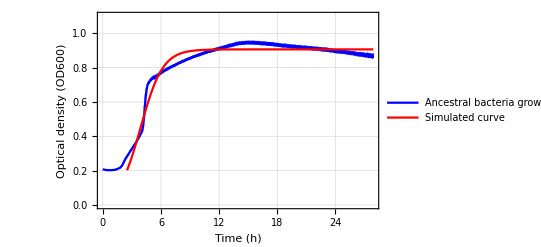

```mathematica
Show[ListLinePlot[bacteriaControl,PlotLegends->Placed[LineLegend[{"Ancestral bacteria\ngrowth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth[k,r,t]/.para[[1,2]],{t,2.5,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,27.9},{0,1.1}}]
```

```mathematica
controldata=Transpose[Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\control_final.xlsx"][[1]]];
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\data_final\\cocktail_growth_data.xlsx"];
TIME=Table[i,{i,0,18,0.1}];
phageA=Transpose[{TIME,experimentData[[4,1]]}];
phageB=Transpose[{TIME,experimentData[[5,1]]}];
phageC=Transpose[{TIME,experimentData[[6,1]]}];
TIME=Table[i,{i,0,27.9,0.1}];
bacteriaControl=controldata;
noLag=Select[bacteriaControl,5.5>#[[1]]≥2&];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==Select[bacteriaControl,#[[1]]==3&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth2[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[phageA,#[[1]]==3.5&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4.2]==Select[phageB,#[[1]]==4.2&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth4[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.8]==Select[phageC,#[[1]]==3.8&][[1,2]]} ,y[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
controldata=Transpose[Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\control_final.xlsx"][[1]]];
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\data_final\\cocktail_growth_data.xlsx"];
TIME=Table[i,{i,0,18,0.1}];
phageA=Transpose[{TIME,experimentData[[4,1]]}];
phageB=Transpose[{TIME,experimentData[[5,1]]}];
phageC=Transpose[{TIME,experimentData[[6,1]]}];
TIME=Table[i,{i,0,27.9,0.1}];
bacteriaControl=controldata;
noLag=Select[bacteriaControl,5.5>#[[1]]≥2&];
germGrowth[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3]==Select[bacteriaControl,#[[1]]==3&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth2[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.5]==Select[phageA,#[[1]]==3.5&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth3[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[4.2]==Select[phageB,#[[1]]==4.2&][[1,2]]} ,y[t],t][[1,1,2]];
germGrowth4[k_,r_,t_]=DSolve[{y'[t]==r *y[t](1-y[t]/k),y[3.8]==Select[phageC,#[[1]]==3.8&][[1,2]]} ,y[t],t][[1,1,2]];
```

Import::nffil: File C:\Users\16337\Dropbox\Stan Yu\Phage project\simulation\control_final.xlsx not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File C:\Users\16337\Dropbox\Stan Yu\Phage project\simulation\data_final\cocktail_growth_data.xlsx not found during Import.

Part::partd: Part specification $Failed⟦4,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦4,1⟧} cannot be transposed.

Part::partd: Part specification $Failed⟦5,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦5,1⟧} cannot be transposed.

Part::partd: Part specification $Failed⟦6,1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«171»},$Failed⟦6,1⟧} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Select[bacteriaControl,#[[1]]==3&][[1,2]]
```

0.327613

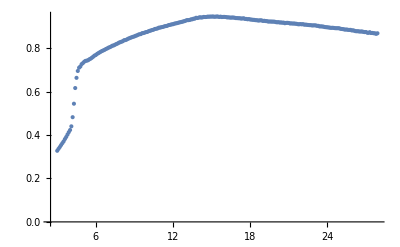

```mathematica
ListPlot[Select[bacteriaControl,#[[1]]≥3&],PlotRange->All]
```

```mathematica
Select[phageA,#[[1]]==3.5&][[1,2]]
```

0.327194

```mathematica
Select[phageB,#[[1]]==4.7&][[1,2]]
```

0.412594

```mathematica
Select[phageC,#[[1]]==4.5&][[1,2]]
```

0.372618

```mathematica
ListPlot[{Select[phageA,#[[1]]>=3.5&],Select[phageB,#[[1]]>=4.2&],Select[phageC,#[[1]]>=3.8&]},PlotLabels->{"a","b","c"},ImageSize->Large]
```

-Graphics-

```mathematica
phageC
```

{{0.,0.209181},{0.1,0.206472},{0.2,0.205931},{0.3,0.204431},{0.4,0.203847},{0.5,0.203576},{0.6,0.203639},{0.7,0.203639},{0.8,0.203535},{0.9,0.203701},{1.,0.204972},{1.1,0.205139},{1.2,0.206056},{1.3,0.205514},{1.4,0.207118},{1.5,0.207493},{1.6,0.207639},{1.7,0.208993},{1.8,0.209097},{1.9,0.210743},{2.,0.211639},{2.1,0.214472},{2.2,0.216347},{2.3,0.21891},{2.4,0.224472},{2.5,0.229201},{2.6,0.235056},{2.7,0.242222},{2.8,0.249785},{2.9,0.257681},{3.,0.263431},{3.1,0.270368},{3.2,0.27666},{3.3,0.281431},{3.4,0.287368},{3.5,0.292931},{3.6,0.297847},{3.7,0.30466},{3.8,0.311076},{3.9,0.317639},{4.,0.32491},{4.1,0.331951},{4.2,0.339806},{4.3,0.347868},{4.4,0.357972},{4.5,0.372618},{4.6,0.396847},{4.7,0.428847},{4.8,0.46766},{4.9,0.506639},{5.,0.544743},{5.1,0.575306},{5.2,0.596701},{5.3,0.608535},{5.4,0.621785},{5.5,0.630951},{5.6,0.641597},{5.7,0.649681},{5.8,0.657472},{5.9,0.666014},{6.,0.673264},{6.1,0.680097},{6.2,0.68516},{6.3,0.689431},{6.4,0.693389},{6.5,0.698201},{6.6,0.702868},{6.7,0.706472},{6.8,0.708576},{6.9,0.711222},{7.,0.715222},{7.1,0.718535},{7.2,0.722326},{7.3,0.724743},{7.4,0.727889},{7.5,0.731451},{7.6,0.733806},{7.7,0.737597},{7.8,0.739764},{7.9,0.742431},{8.,0.744847},{8.1,0.748576},{8.2,0.750306},{8.3,0.752285},{8.4,0.755222},{8.5,0.757618},{8.6,0.757514},{8.7,0.760431},{8.8,0.763347},{8.9,0.765285},{9.,0.767618},{9.1,0.769368},{9.2,0.772306},{9.3,0.774201},{9.4,0.775701},{9.5,0.779181},{9.6,0.779326},{9.7,0.782847},{9.8,0.785264},{9.9,0.786035},{10.,0.788993},{10.1,0.790431},{10.2,0.79241},{10.3,0.793118},{10.4,0.79516},{10.5,0.797056},{10.6,0.799139},{10.7,0.802056},{10.8,0.804347},{10.9,0.803451},{11.,0.805535},{11.1,0.807972},{11.2,0.810764},{11.3,0.810847},{11.4,0.812743},{11.5,0.815889},{11.6,0.818118},{11.7,0.817826},{11.8,0.818306},{11.9,0.821222},{12.,0.822326},{12.1,0.823889},{12.2,0.82516},{12.3,0.826681},{12.4,0.827826},{12.5,0.829139},{12.6,0.830722},{12.7,0.832868},{12.8,0.836618},{12.9,0.836056},{13.,0.837139},{13.1,0.838493},{13.2,0.840056},{13.3,0.840389},{13.4,0.842576},{13.5,0.843264},{13.6,0.844326},{13.7,0.846285},{13.8,0.846181},{13.9,0.847847},{14.,0.848639},{14.1,0.850014},{14.2,0.851514},{14.3,0.85166},{14.4,0.853389},{14.5,0.852764},{14.6,0.855306},{14.7,0.856743},{14.8,0.85641},{14.9,0.856743},{15.,0.857722},{15.1,0.858056},{15.2,0.861743},{15.3,0.861326},{15.4,0.861306},{15.5,0.861097},{15.6,0.86191},{15.7,0.863847},{15.8,0.864764},{15.9,0.865035},{16.,0.866222},{16.1,0.868868},{16.2,0.868681},{16.3,0.86916},{16.4,0.869681},{16.5,0.869014},{16.6,0.869181},{16.7,0.86941},{16.8,0.870306},{16.9,0.87141},{17.,0.870972},{17.1,0.872514},{17.2,0.873285},{17.3,0.871618},{17.4,0.871597},{17.5,0.873243},{17.6,0.871951},{17.7,0.872368},{17.8,0.874785},{17.9,0.87441},{18.,0.872701}}

```mathematica
bacteriaControl
```

{{0.,0.223929},{0.1,0.221518},{0.2,0.220322},{0.3,0.219714},{0.4,0.219134},{0.5,0.219134},{0.6,0.21867},{0.7,0.219286},{0.8,0.219804},{0.9,0.220411},{1.,0.220554},{1.1,0.222116},{1.2,0.223161},{1.3,0.225616},{1.4,0.228598},{1.5,0.231688},{1.6,0.235804},{1.7,0.240161},{1.8,0.247688},{1.9,0.254098},{2.,0.261429},{2.1,0.269625},{2.2,0.278072},{2.3,0.287411},{2.4,0.296697},{2.5,0.305339},{2.6,0.31367},{2.7,0.322464},{2.8,0.331188},{2.9,0.339081},{3.,0.347706},{3.1,0.356572},{3.2,0.364991},{3.3,0.374661},{3.4,0.383714},{3.5,0.394973},{3.6,0.408223},{3.7,0.423706},{3.8,0.438214},{3.9,0.45817},{4.,0.485813},{4.1,0.512259},{4.2,0.53617},{4.3,0.559643},{4.4,0.590366},{4.5,0.619482},{4.6,0.647098},{4.7,0.666313},{4.8,0.679232},{4.9,0.692536},{5.,0.701366},{5.1,0.710411},{5.2,0.717241},{5.3,0.723661},{5.4,0.726563},{5.5,0.730991},{5.6,0.733759},{5.7,0.736232},{5.8,0.740054},{5.9,0.744188},{6.,0.745098},{6.1,0.748482},{6.2,0.749348},{6.3,0.753304},{6.4,0.756973},{6.5,0.758732},{6.6,0.760081},{6.7,0.76175},{6.8,0.764947},{6.9,0.767732},{7.,0.770232},{7.1,0.770866},{7.2,0.773009},{7.3,0.776482},{7.4,0.777723},{7.5,0.778688},{7.6,0.780777},{7.7,0.784188},{7.8,0.785},{7.9,0.789018},{8.,0.795714},{8.1,0.79725},{8.2,0.790866},{8.3,0.787777},{8.4,0.785357},{8.5,0.784625},{8.6,0.785232},{8.7,0.784741},{8.8,0.782536},{8.9,0.7825},{9.,0.780714},{9.1,0.779107},{9.2,0.777456},{9.3,0.775545},{9.4,0.771813},{9.5,0.773331},{9.6,0.786072},{9.7,0.818723},{9.8,0.863197},{9.9,0.913116},{10.,0.949911},{10.1,0.972098},{10.2,0.985563},{10.3,0.993384},{10.4,0.999214},{10.5,1.00286},{10.6,1.00853},{10.7,1.01193},{10.8,1.01419},{10.9,1.01688},{11.,1.01908},{11.1,1.02091},{11.2,1.02475},{11.3,1.02601},{11.4,1.02978},{11.5,1.03046},{11.6,1.03326},{11.7,1.03518},{11.8,1.03663},{11.9,1.03972},{12.,1.03952},{12.1,1.04306},{12.2,1.04407},{12.3,1.04561},{12.4,1.04839},{12.5,1.04903},{12.6,1.05134},{12.7,1.05233},{12.8,1.05496},{12.9,1.05516},{13.,1.05773},{13.1,1.05795},{13.2,1.05914},{13.3,1.06082},{13.4,1.06256},{13.5,1.0651},{13.6,1.06607},{13.7,1.06683},{13.8,1.06888},{13.9,1.06957},{14.,1.07039},{14.1,1.07277},{14.2,1.07294},{14.3,1.07337},{14.4,1.07582},{14.5,1.07609},{14.6,1.0784},{14.7,1.08038},{14.8,1.08065},{14.9,1.08158},{15.,1.08364},{15.1,1.08368},{15.2,1.08463},{15.3,1.08651},{15.4,1.08663},{15.5,1.08788},{15.6,1.08885},{15.7,1.09011},{15.8,1.09054},{15.9,1.09135},{16.,1.09155},{16.1,1.09279},{16.2,1.0946},{16.3,1.09504},{16.4,1.09563},{16.5,1.09613},{16.6,1.09605},{16.7,1.09724},{16.8,1.09778},{16.9,1.09761},{17.,1.09804},{17.1,1.09962},{17.2,1.10101},{17.3,1.0987},{17.4,1.09987},{17.5,1.1017},{17.6,1.10081},{17.7,1.10043},{17.8,1.10049},{17.9,1.10096},{18.,1.10043},{18.1,1.10054},{18.2,1.10131},{18.3,1.10101},{18.4,1.10134},{18.5,1.09996},{18.6,1.10022},{18.7,1.10021},{18.8,1.09941},{18.9,1.09901},{19.,1.10121},{19.1,1.09958},{19.2,1.09887},{19.3,1.09756},{19.4,1.09766},{19.5,1.09716},{19.6,1.09721},{19.7,1.09638},{19.8,1.0956},{19.9,1.09521},{20.,1.09464},{20.1,1.09413},{20.2,1.09333},{20.3,1.0934},{20.4,1.09315},{20.5,1.09054},{20.6,1.09106},{20.7,1.08905},{20.8,1.09104},{20.9,1.08859},{21.,1.08804},{21.1,1.08718},{21.2,1.08654},{21.3,1.08684},{21.4,1.08657},{21.5,1.08574},{21.6,1.08269},{21.7,1.08296},{21.8,1.08321},{21.9,1.08184},{22.,1.08066},{22.1,1.07957},{22.2,1.07841},{22.3,1.07902},{22.4,1.0783},{22.5,1.07779},{22.6,1.0742},{22.7,1.07442},{22.8,1.07462},{22.9,1.07423},{23.,1.07334},{23.1,1.07192},{23.2,1.07083},{23.3,1.06963},{23.4,1.06833},{23.5,1.06701},{23.6,1.06551},{23.7,1.06486},{23.8,1.06363},{23.9,1.06288},{24.,1.05998},{24.1,1.05949},{24.2,1.05873},{24.3,1.05783},{24.4,1.0548},{24.5,1.05324},{24.6,1.05242},{24.7,1.05019},{24.8,1.04899},{24.9,1.04761},{25.,1.04759},{25.1,1.04588},{25.2,1.04346},{25.3,1.04168},{25.4,1.04206},{25.5,1.04041},{25.6,1.03936},{25.7,1.03731},{25.8,1.03591},{25.9,1.03578},{26.,1.03313},{26.1,1.03137},{26.2,1.03026},{26.3,1.02867},{26.4,1.02596},{26.5,1.02372},{26.6,1.02404},{26.7,1.02446},{26.8,1.02347},{26.9,1.02182},{27.,1.02006},{27.1,1.01866},{27.2,1.01593},{27.3,1.01563},{27.4,1.01212},{27.5,1.01397},{27.6,1.01369},{27.7,1.01086},{27.8,1.01037},{27.9,1.00911}}

```mathematica
para=FindFit[noLag,{germGrowth[k,r,t],0.881>r>0.88,1.1>k>0},{{k,0.9},{r,0.88}},t]
```

{k→0.913762,r→0.880001}

```mathematica
para2=FindFit[Select[phageA,#[[1]]>=3.5&],{germGrowth2[0.88,r,t],r>0.77},{{r,0.89}},t]
```

{r→0.77}

```mathematica
para3=FindFit[Select[phageB,#[[1]]>=4.2&],{germGrowth3[0.998,r,t],r>0.8},{{r,0.88}},t]
```

{r→0.8}

```mathematica
para4=FindFit[Select[phageC,#[[1]]>=3.8&],{germGrowth4[0.88,r,t],r>0.81},{{r,0.88}},t]
```

{r→0.81}

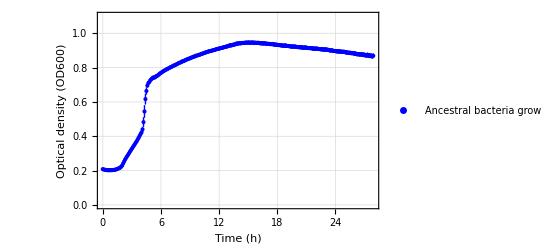

```mathematica
ListPlot[bacteriaControl,PlotLegends->Placed[LineLegend[{"Ancestral bacteria\ngrowth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,27.9},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"}]
```

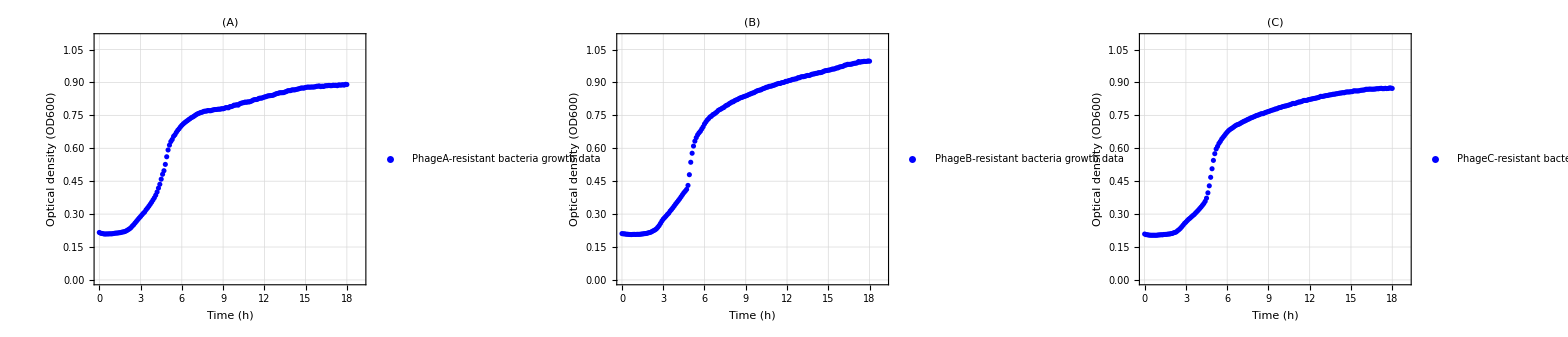

```mathematica
GraphicsGrid[{{ListPlot[phageA,PlotLegends->Placed[LineLegend[{"PhageA-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(A)"],ListPlot[phageB,PlotLegends->Placed[LineLegend[{"PhageB-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(B)"],ListPlot[phageC,PlotLegends->Placed[LineLegend[{"PhageC-resistant\nbacteria growth data"}],{0.15,0.9}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->{{0,19},{0,1.1}},ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotLabel->"(C)"]}},Alignment->Center,Spacings->0]
```

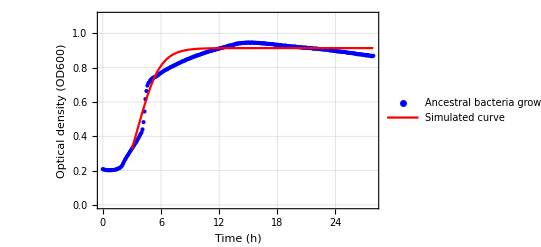

```mathematica
Anfit=Show[ListPlot[bacteriaControl,PlotLegends->Placed[LineLegend[{"Ancestral bacteria\ngrowth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth[k,r,t]/.para,{t,3,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,27.9},{0,1.1}}]
```

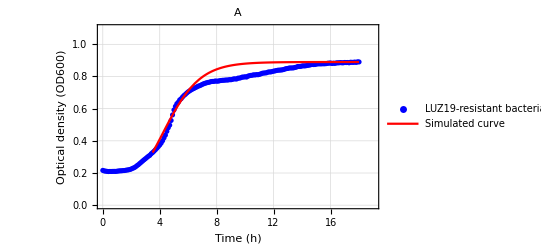

```mathematica
Afit=Show[ListPlot[phageA,PlotLegends->Placed[LineLegend[{"LUZ19-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth2[0.89,r,t]/.para2,{t,3.5,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"A"]
```

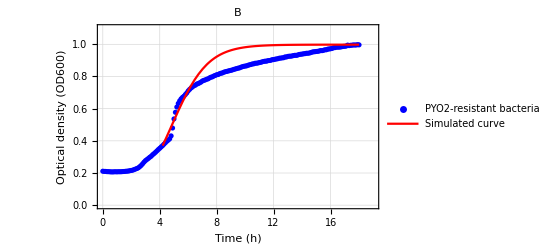

```mathematica
Bfit=Show[ListPlot[phageB,PlotLegends->Placed[LineLegend[{"PYO2-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth3[0.998,r,t]/.para3,{t,4.2,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"B"]
```

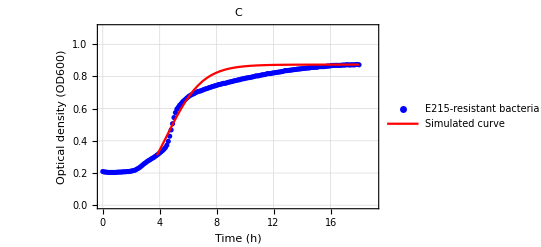

```mathematica
Cfit=Show[ListPlot[phageC,PlotLegends->Placed[LineLegend[{"E215-resistant\nbacteria growth data"}],{0.75,0.5}],PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"},PlotRange->All],Plot[germGrowth4[0.874,r,t]/.para4,{t,3.8,18},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated curve"}],{0.75,0.37}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,25},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Frame->True,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,19},{0,1.1}},PlotLabel->"C"]
```

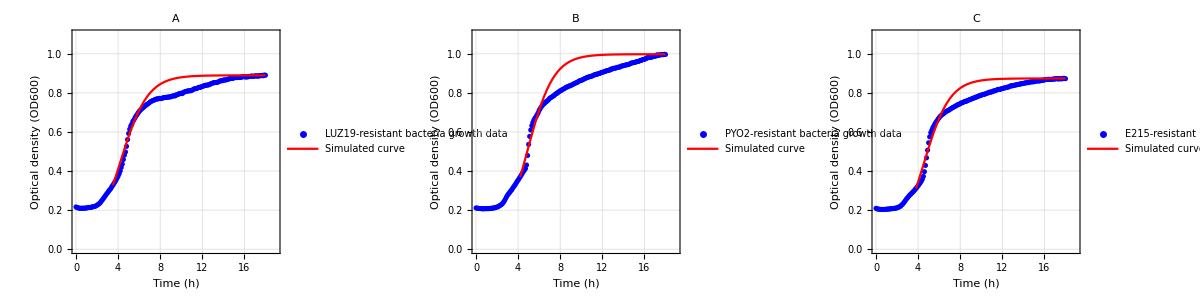

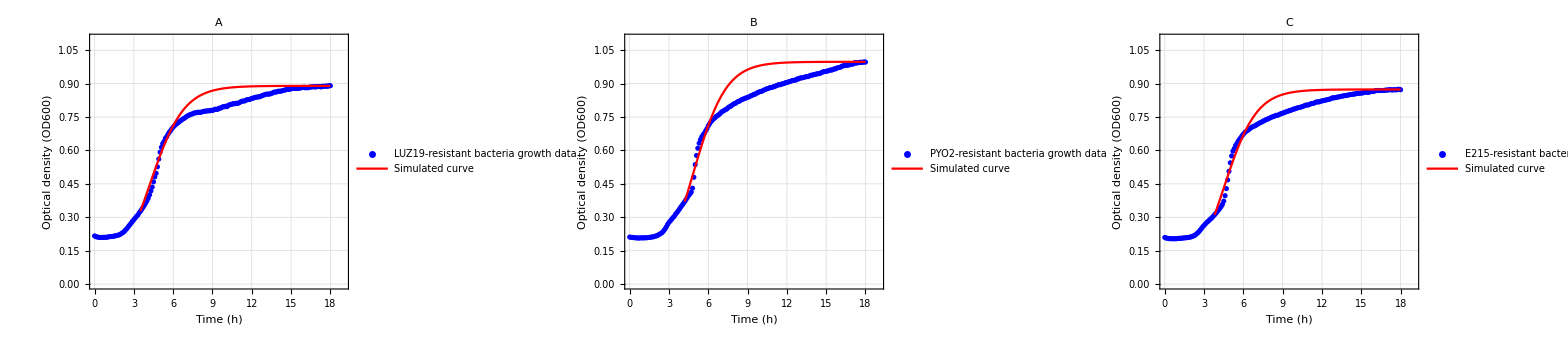

```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-,-Graphics-}},ImageSize->3000]
```

## Estimate phage-A-specific parameter values

### ra

```mathematica
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
```

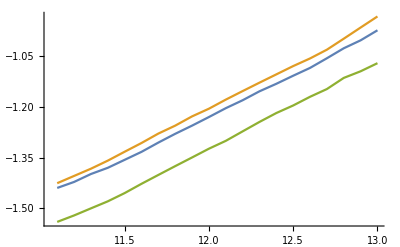

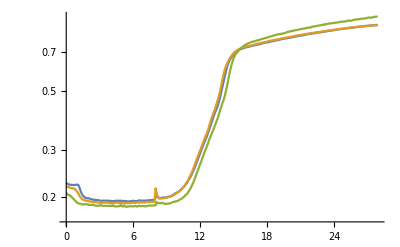

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageAMOI01=Transpose[{TIME,experimentData[[1,1]]}];
phageAMOI1=Transpose[{TIME,experimentData[[2,1]]}];
phageAMOI10=Transpose[{TIME,experimentData[[3,1]]}];
expA01=Select[phageAMOI01,11.1<=#[[1]]≤13&];
expA1=Select[phageAMOI1,11.1<=#[[1]]≤13&];
expA10=Select[phageAMOI10,11.1<=#[[1]]≤13&];
logExpA01=Replace[expA01,{x_,y_}->{x,Log[y]},1];
logExpA1=Replace[expA1,{x_,y_}->{x,Log[y]},1];
logExpA10=Replace[expA10,{x_,y_}->{x,Log[y]},1];
ListLinePlot[{logExpA01,logExpA1,logExpA10}]
ListLogPlot[{phageAMOI01,phageAMOI1,phageAMOI10},Joined->True]
```

```mathematica
linear1=LinearModelFit[logExpA01,{1,t},t]
linear1["ANOVATable"]
linear2=LinearModelFit[logExpA1,{1,t},t]
linear2["ANOVATable"]
linear3=LinearModelFit[logExpA10,{1,t},t]
linear3["ANOVATable"]
```

FittedModel[-8.62028+0.53644 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 1.91366 | 1.91366 | 5978.55 | 3.67455×10^-24
Error | 18 | 0.00576157 | 0.000320087 |  | 
Total | 19 | 1.91942 |  |  |

FittedModel[-9.29502+0.602517 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 2.41413 | 2.41413 | 4181.29 | 9.0779×10^-23
Error | 18 | 0.0103926 | 0.000577365 |  | 
Total | 19 | 2.42452 |  |  |

FittedModel[-9.62721+0.633488 t]

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 2.66869 | 2.66869 | 2390.55 | 1.35332×10^-20
Error | 18 | 0.0200943 | 0.00111635 |  | 
Total | 19 | 2.68878 |  |  |

```mathematica
(* Approximate value for ra, used as guess in findfit *)
```

```mathematica
Mean[{0.5364401982391751 ,0.602517499659348,0.6334877403684634}]
```

0.590815

#### Fitting using data from phage A only experiment

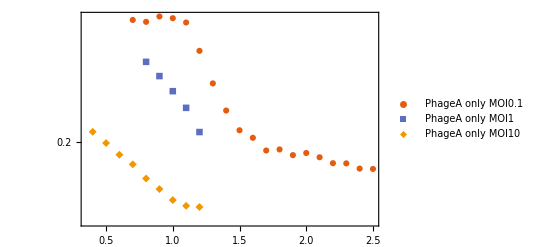

```mathematica
experimentData=Import["C:\\Users\\16337\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageAMOI01=Transpose[{TIME,experimentData[[1,1]]}];
phageAMOI1=Transpose[{TIME,experimentData[[2,1]]}];
phageAMOI10=Transpose[{TIME,experimentData[[3,1]]}];
(* Different ranges for different MOI. Different lags? *)
beginA01=Select[phageAMOI01,0.7<=#[[1]]≤2.5&];
beginA1=Select[phageAMOI1,0.8<=#[[1]]≤1.2&];
beginA10=Select[phageAMOI10,0.4<=#[[1]]≤1.2&];g1=ListLogPlot[{beginA01,beginA1,beginA10},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotRange->All,ImageSize->Full]
```

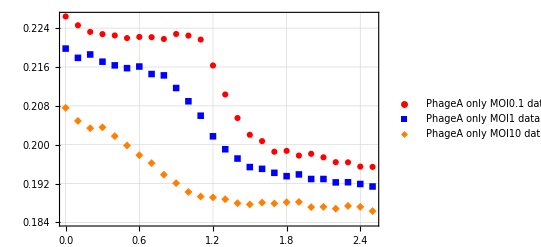

```mathematica
earlyData=ListPlot[{Select[phageAMOI01,0<=#[[1]]≤2.5&],Select[phageAMOI1,0<=#[[1]]≤2.5&],Select[phageAMOI10,0<=#[[1]]≤2.5&]},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1 data","PhageA only MOI1 data","PhageA only MOI10 data"}],{0.2,0.2}],Frame->True,PlotTheme->"Detailed",BaseStyle->{Bold,14},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotStyle->{Red,Blue,Orange}]
```

```mathematica
(* Models for different MOI, used to estimate b, h, s, and p *)
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.8772547720626924*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
sol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
sol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.4]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
model1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol1[a,k,b,h,s,p,B0,MOI][t]
model2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol2[a,k,b,h,s,p,B0,MOI][t]
model3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=sol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
MOI01INI=Select[phageAMOI01,0.7==#[[1]]&][[1,2]];
MOI1INI=Select[phageAMOI1,0.8==#[[1]]&][[1,2]];
MOI10INI=Select[phageAMOI10,0.4==#[[1]]&][[1,2]];
```

ParametricNDSolveValue::ndsz: At t == 0.678878, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 0.678879, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 0.678878, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

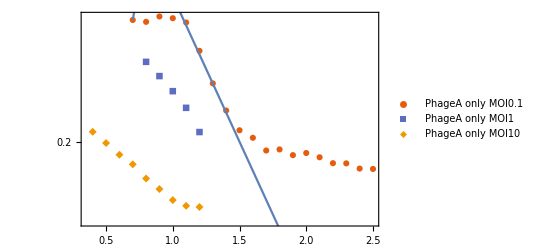

{b→460.,s→0.250001}

```mathematica
(* Fit to phageA MOI01 data 1.1 to 5 hours *)
fitModel1=NonlinearModelFit[beginA01,{model1[0,1,b,100,s,0.09,MOI01INI,0.1,t],b==460,0.25<s<1},{b,s},t];
Show[g1,LogPlot[fitModel1[t],{t,0.7,2.5}]]
fitModel1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.790001, step size is effectively zero; singularity or stiff system suspected.

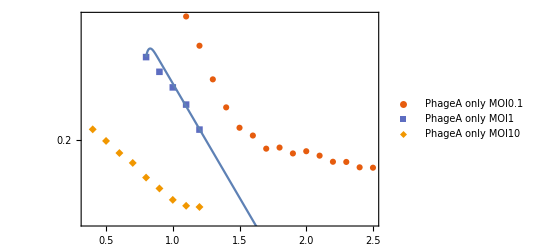

{b→460.,s→0.19}

```mathematica
fitModel2=NonlinearModelFit[beginA1,{model2[0,1,b,100,s,0.09,MOI1INI,1,t],b==460,s==0.19},{b,s},t];
Show[g1,LogPlot[fitModel2[t],{t,0.8,5}]]
fitModel2[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.389561, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

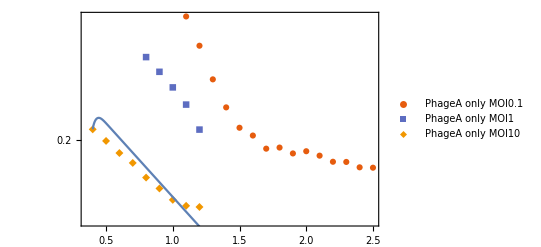

{b→460.,s→0.122835}

```mathematica
fitModel3=NonlinearModelFit[beginA10,{model3[0,1,b,100,s,0.09,MOI10INI,1,t],b==460,0.1<s<3},{b,s},t];
Show[g1,LogPlot[fitModel3[t],{t,0.4,1.2}]]
fitModel3[[1,2]]
```

```mathematica
(* Estimated value for b *)
Mean[{278.29302358448314,269.29353987583715,283.50759875150936}]
```

277.031

```mathematica
(* Estimated value for s*)
Mean[{2.940544982380593,2.989984068243238,2.9947033290569367}]
```

2.97508

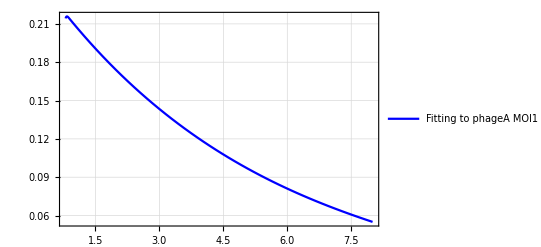

```mathematica
GphageAMOI1Early=Plot[{fitModel2[t]},{t,0.8,8},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to phageA MOI1 data"}],{0.2,0.3}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

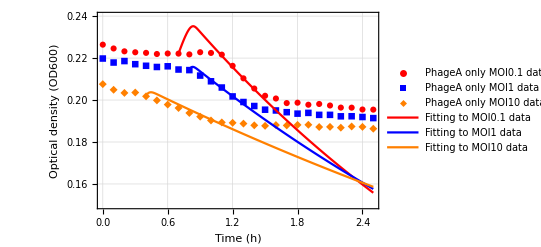

```mathematica
Show[earlyData,Plot[{fitModel1[t]},{t,0.7,2.5},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"}],{0.5,0.3}]],Plot[{fitModel2[t]},{t,0.8,2.5},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"}],{0.5,0.2}]],Plot[{fitModel3[t]},{t,0.4,2.5},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"}],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},PlotRange->{{0,2.5},{0.15,0.24}}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
```

```mathematica
Remove[s]
```

```mathematica
X[t]
```

{B[t],Bi[t],Br[t],P[t],Bt[t]}

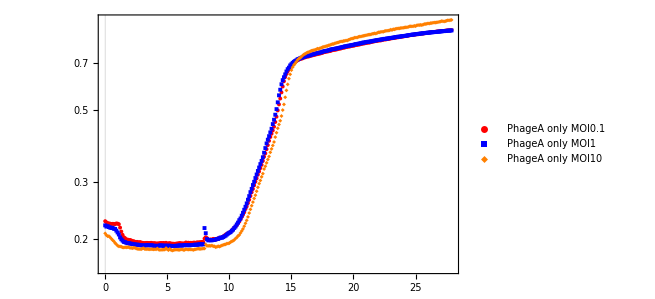

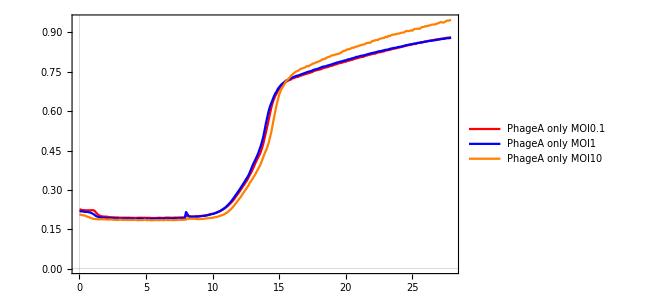

```mathematica
(* Models for different MOI, used to estimate a *)
PH2[a_,k_,b_,h_,s_,p_,ra_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
sol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[1.1]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
solFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,0.8,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol5new=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},{B,Br},{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
sol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,ra]/.Thread[stateVar2->X[t]])},X[0.4]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,ra,B0,MOI}];
model4[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol4[a,k,b,h,s,p,ra,B0,MOI][t]
model5[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol5[a,k,b,h,s,p,ra,B0,MOI][t]
model6[a_,k_,b_,h_,s_,p_,ra_,B0_,MOI_,t_]:=sol6[a,k,b,h,s,p,ra,B0,MOI][t]
afterA01=Select[phageAMOI01,1.1<=#[[1]]&];
afterA1=Select[phageAMOI1,0.8<=#[[1]]&];
afterA10=Select[phageAMOI10,0.4<=#[[1]]&];
MOI01INI=Select[phageAMOI01,1.1==#[[1]]&][[1,2]];
MOI1INI=Select[phageAMOI1,0.8==#[[1]]&][[1,2]];
MOI10INI=Select[phageAMOI10,0.4==#[[1]]&][[1,2]];
g2=ListLogPlot[{phageAMOI01,phageAMOI1,phageAMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
g3=ListLinePlot[{phageAMOI01,phageAMOI1,phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1","PhageA only MOI1","PhageA only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
fitModel4=NonlinearModelFit[afterA01,{model4[0.008,0.625,277.3725714997275,100,2.975335485731218,0.08,ra,MOI01INI,0.1,t],0.7<ra<0.75},ra,t];
```

ParametricNDSolveValue::ndsz: At t == 0.965728, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

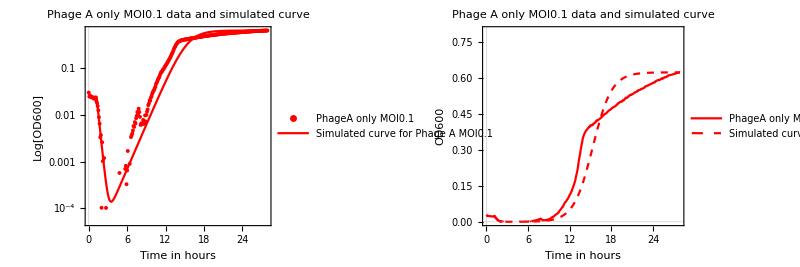

{ra→0.73}

```mathematica
g4=GraphicsGrid[{{Show[ListLogPlot[{phageAMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel4[t],{t,1.1,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageAMOI01},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotRange->{{0,27.9},{0,0.8}}],Plot[fitModel4[t],{t,1.1,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
fitModel4[[1,2]]
```

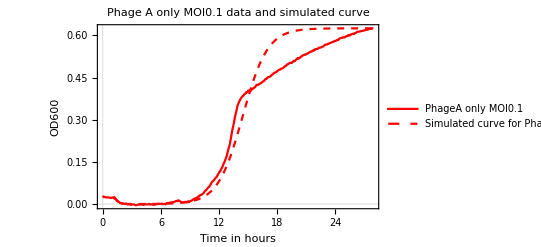

```mathematica
singlePhageG1=Show[ListLinePlot[{phageAMOI01},PlotLegends->Placed[LineLegend[{"PhageA only MOI0.1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel4[t],{t,1.1,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
fitModel5=NonlinearModelFit[afterA1,{model5[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1,t],ra==0.77,a>0.01},{ra,{a,0.027}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.790003, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

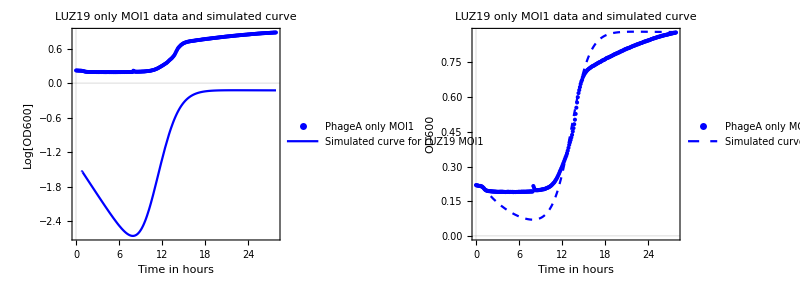

{ra→0.77,a→0.0170428}

```mathematica
g5=GraphicsGrid[{{Show[ListPlot[{phageAMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel5[t],{t,0.8,27.9},PlotStyle->Blue,
PlotLegends->Placed[LineLegend[{"Simulated curve for\nLUZ19 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"LUZ19 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange-> All],Show[ListPlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nLUZ19 MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"LUZ19 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0,PlotRange-> {{0,27.9},{0,1}}]
fitModel5[[1,2]]
```

```mathematica
{a,{b,c,d}}
```

{a,{b,c,d}}

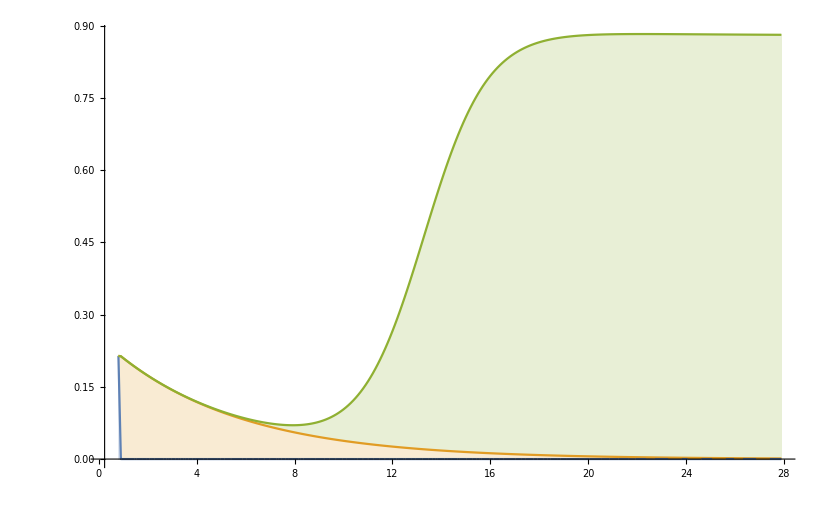

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]])[[1;;3]]]],{t,0.8,27.9,0.1}]]]
```

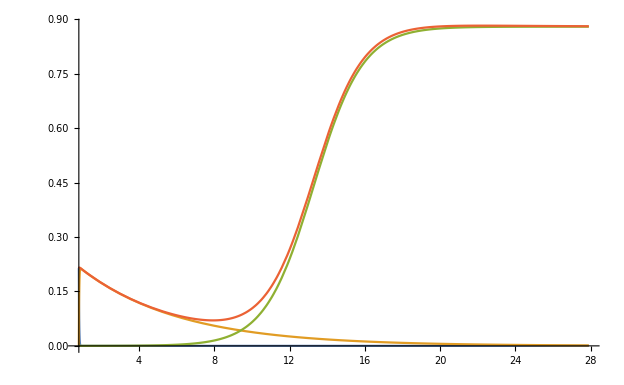

```mathematica
Plot[Evaluate[solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]]],{t,0.8,27.9}]
```

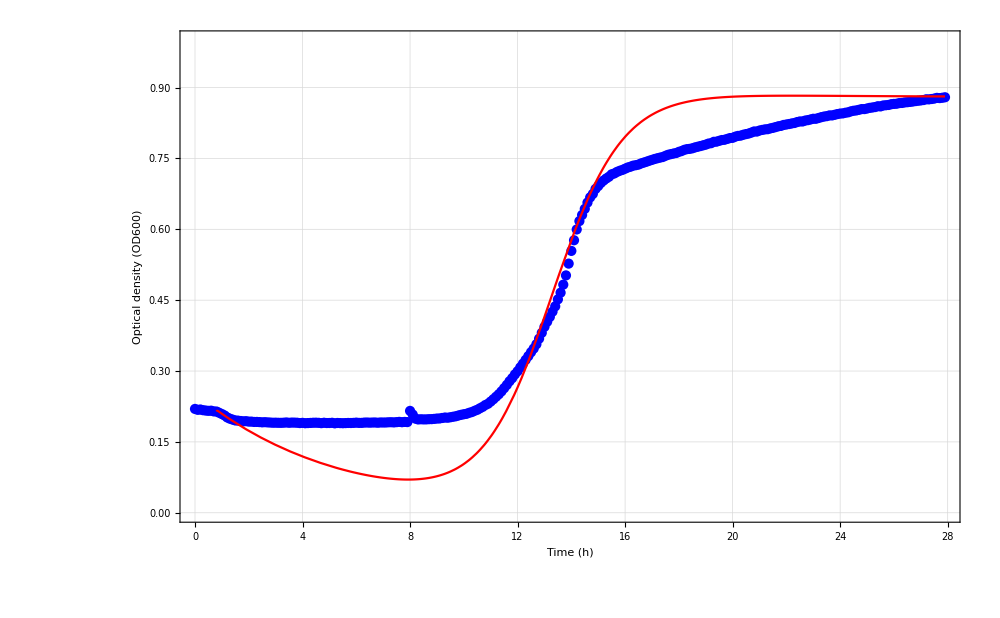

```mathematica
gf11=Show[ListPlot[{phageAMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"LUZ19-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,23},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",BaseStyle->{Bold,25,FontFamily->"Times"},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,14,FontFamily->"Times"},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

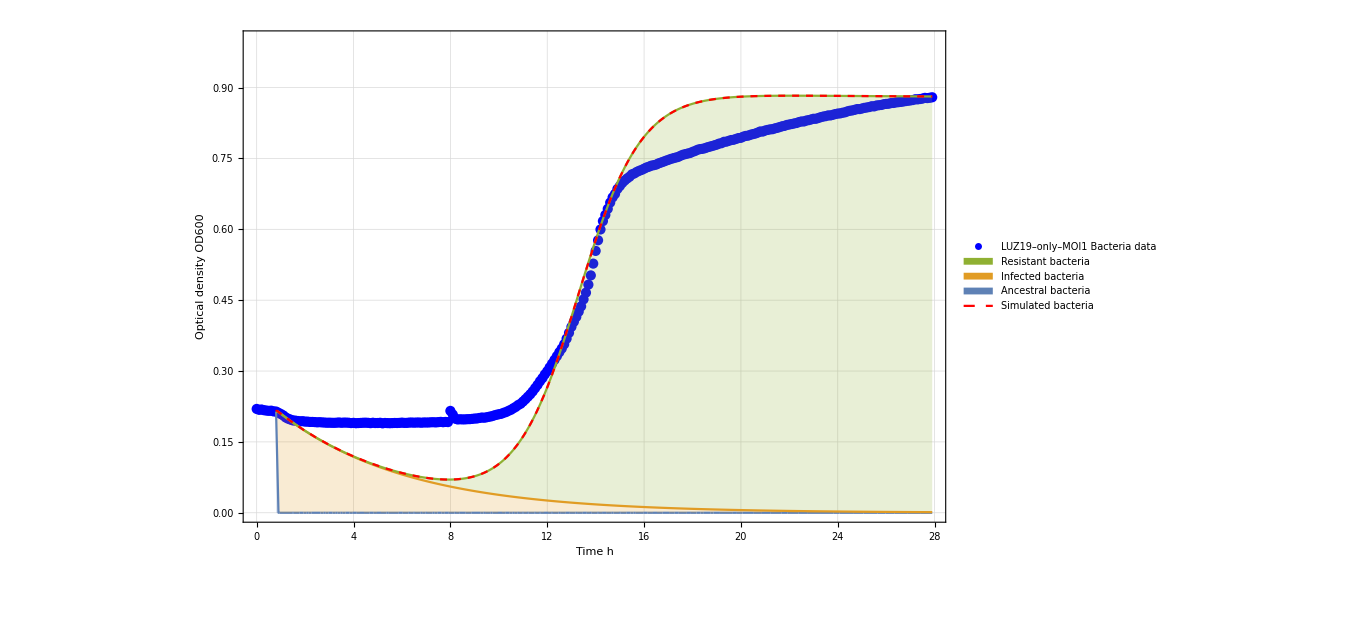
-Graphics-A

```mathematica
gf12=Labeled[Show[ListPlot[{phageAMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"LUZ19–only–MOI1 Bacteria data"}],{0.35,0.9}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{FontFamily->"Times",Bold,35},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(solFinal[a,0.88,460,100,0.19,0.09,ra,MOI1INI,1]/.fitModel5[[1,2]])[[1;;3]]]],{t,0.8,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.22,0.7}],LabelStyle->{FontFamily->"Times"}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.22,0.5}],PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{Bold,Black},GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time h","Optical density OD600"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}],Style["A","Section",Bold,50,Black,FontFamily->"Times"],{{Top,Left}}]
```

```mathematica
Export["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\test_img.svg",StringReplace[ExportString[gf12,"SVG"],{"stroke-linecap:square"->"stroke-linecap:round","stroke-miterlimit:3.25"->"stroke-miterlimit:0.1"}],"Text"]
```

C:\Users\zhiyu\Dropbox\Stan Yu\Phage project\simulation\test_img.svg

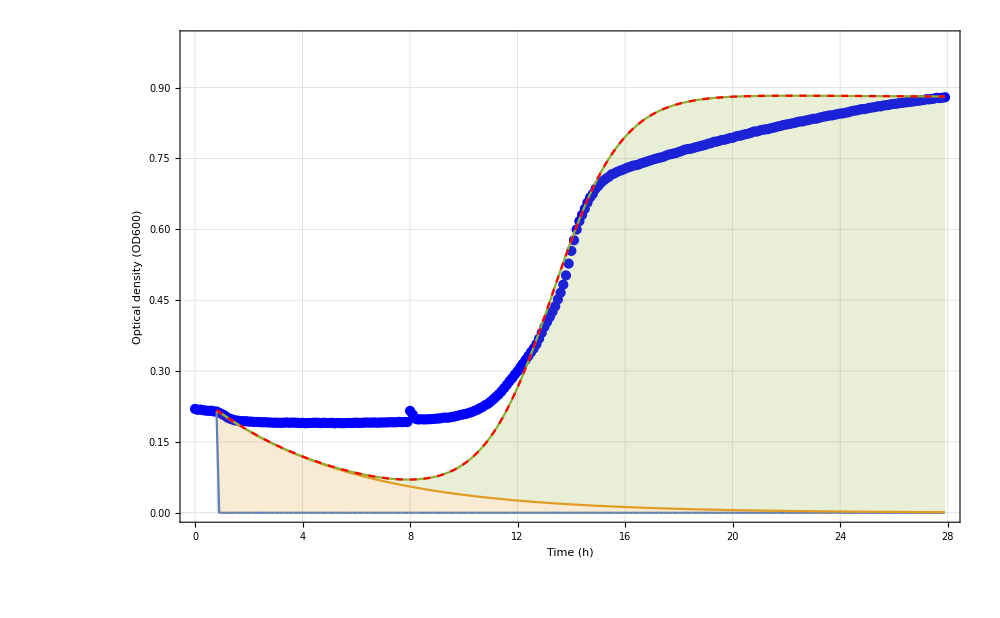
A
-Graphics-
-Graphics-

```mathematica
gf1=Grid[{{Style["A",FontFamily->"Times",FontSize->30]},{gf11},{gf12}}]
```

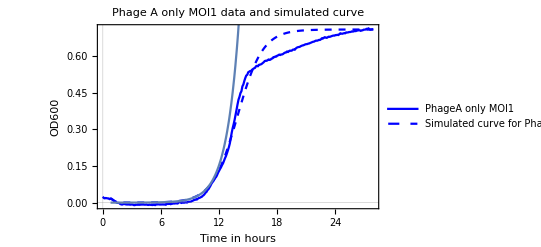

```mathematica
singlePhageG2=Show[ListLinePlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"PhageA only MOI1"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel5[t],{t,0.8,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],Plot[0.000015*E^((0.77+0.09/(277*100)*0.027)*t),{t,0.8,27.9},PlotRange->All],PlotLabel->"Phage A only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
Through[sol5new[0.027,0.88,460,100,0.17,0.09,0.77,MOI1INI,1][5]]
```

{9.75938×10^-11,0.00139147}

```mathematica
fitModel5[0.8]
```

0.0164528

```mathematica
MOI1INI*0.027*0.1
```

0.0000444226

```mathematica
0.000015*E^((0.77+0.09/(277*100)*0.027)*0.8)
```

0.0000277726

```mathematica
0.09/(277*100)*0.027
```

8.77256×10^-8

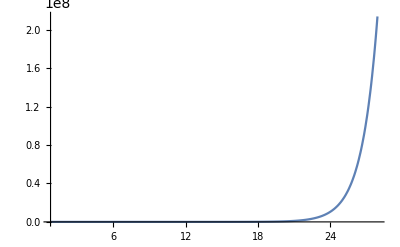

```mathematica
Plot[0.1*E^((0.77+0.09/(277*100)*0.027)*t),{t,0.8,27.9},PlotRange->All]
```

```mathematica
fitModel6=NonlinearModelFit[afterA10,{model6[0.008,0.74,277.3725714997275,100,2.975335485731218,0.09,ra,MOI10INI,1,t],0.77<ra<0.78},ra,t];
```

ParametricNDSolveValue::ndsz: At t == 0.288376, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

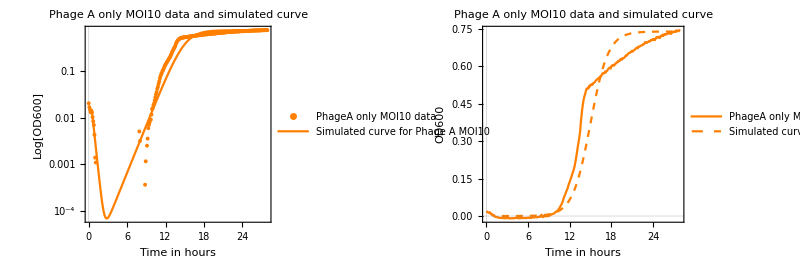

{ra→0.78}

```mathematica
g6=GraphicsGrid[{{Show[ListLogPlot[{phageAMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[fitModel6[t],{t,0.4,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[fitModel6[t],{t,0.4,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
fitModel6[[1,2]]
```

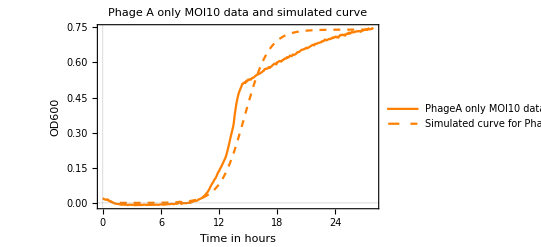

```mathematica
singlePhageG3=Show[ListLinePlot[{phageAMOI10},PlotLegends->Placed[LineLegend[{"PhageA only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[fitModel6[t],{t,0.4,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage A MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage A only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
(* Estimated value for mutation rate(mutate to phageA-resistant)*)
Mean[{0.02467596629360689,0.019187907363862885,0.024999519798104046}]
```

0.0229545

```mathematica
(* Estimated value for ra *)
Mean[{0.7299999924120847,0.8,0.78}]
```

0.77

```mathematica
GraphicsGrid[{{g4},{g5},{g6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

## Estimate phage-B-specific parameter values

### rb

```mathematica
expB01=Select[phageBMOI01,13<=#[[1]]≤15&];
expB1=Select[phageBMOI1,13<=#[[1]]≤15&];
expB10=Select[phageBMOI10,13<=#[[1]]≤15&];
logExpB01=Replace[expB01,{x_,y_}->{x,Log[y]},1];
logExpB1=Replace[expB1,{x_,y_}->{x,Log[y]},1];
logExpB10=Replace[expB10,{x_,y_}->{x,Log[y]},1];
ListLogPlot[{phageBMOI01,phageBMOI1,phageBMOI10},Joined->True,PlotLegends->{"MOI0.1","MOI1","MOI10"}]
ListLinePlot[{logExpB01,logExpB1,logExpB10}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI01,13≤#1⟦1⟧≤15&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI1,13≤#1⟦1⟧≤15&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI10,13≤#1⟦1⟧≤15&].

-Graphics-

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI01,13.≤#1⟦1⟧≤15.&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI1,13.≤#1⟦1⟧≤15.&].

Select::normal: Nonatomic expression expected at position 1 in Select[phageBMOI10,13.≤#1⟦1⟧≤15.&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

-Graphics-

```mathematica
linear1=LinearModelFit[logExpB01,{1,t},t]
linear1["ANOVATable"]
linear2=LinearModelFit[logExpB1,{1,t},t]
linear2["ANOVATable"]
linear3=LinearModelFit[logExpB10,{1,t},t]
linear3["ANOVATable"]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI01,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI01,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI1,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI1,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Select[phageBMOI10,13≤#1⟦1⟧≤15&],{1,t},t]

LinearModelFit[Select[phageBMOI10,13≤#1⟦1⟧≤15&],{1,t},t][ANOVATable]

```mathematica
Mean[{0.6261622776470807,0.6617650507813915 ,0.7471335578274599}]
```

0.678354

#### Fitting using data from phage B only experiment

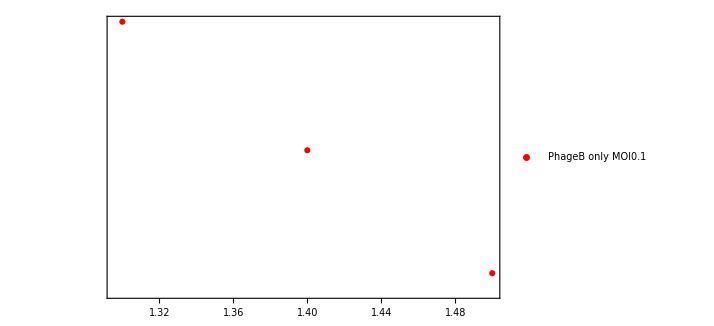

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageBMOI01=Transpose[{TIME,experimentData[[4,1]]}];
phageBMOI1=Transpose[{TIME,experimentData[[5,1]]}];
phageBMOI10=Transpose[{TIME,experimentData[[6,1]]}];
beginB01=Select[phageBMOI01,1.6<=#[[1]]≤2.4&];
beginB1=Select[phageBMOI1,1.3<=#[[1]]≤1.5&];
beginB10=Select[phageBMOI10,0.7<=#[[1]]≤1.7&];PBg1=ListLogPlot[{beginB1},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange}]
```

```mathematica
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.8772547720626924*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.8772547720626924*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PBsol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.6]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBsol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBsol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,5},{a,k,b,h,s,p,B0,MOI}];
PBmodel1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol1[a,k,b,h,s,p,B0,MOI][t]
PBmodel2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol2[a,k,b,h,s,p,B0,MOI][t]
PBmodel3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PBsol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
PBMOI01INI=Select[phageBMOI01,1.6==#[[1]]&][[1,2]];
PBMOI1INI=Select[phageBMOI1,1.3==#[[1]]&][[1,2]];
PBMOI10INI=Select[phageBMOI10,0.7==#[[1]]&][[1,2]];
```

ParametricNDSolveValue::ndsz: At t == 1.25244, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 1.25245, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 1.25244, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

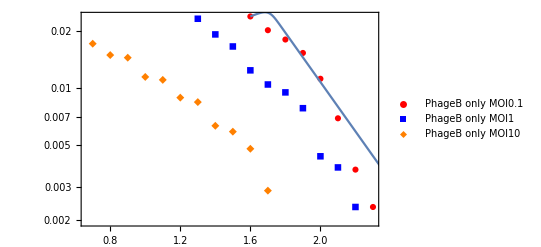

{b→277.,s→2.9934}

```mathematica
PBfitModel1=NonlinearModelFit[beginB01,{PBmodel1[0,1,b,100,s,0.09,PBMOI01INI,0.1,t],b==277,0<s<3},{b,s},t];
Show[PBg1,LogPlot[PBfitModel1[t],{t,1.6,2.4}]]
PBfitModel1[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 1.29028, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

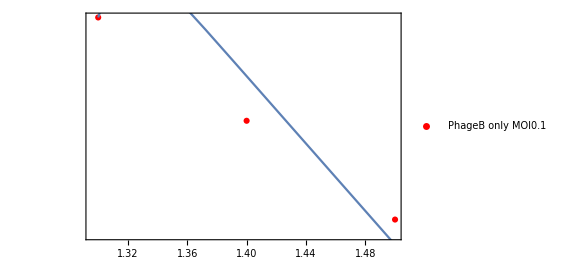

{b→460.,s→0.252181}

```mathematica
PBfitModel2=NonlinearModelFit[beginB1,{PBmodel2[0,1,b,100,s,0.09,PBMOI1INI,1,t],b==460,0<s},{b,s},t];
Show[PBg1,LogPlot[PBfitModel2[t],{t,1.3,2.2}]]
PBfitModel2[[1,2]]
```

ParametricNDSolveValue::ndsz: At t == 0.619856, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

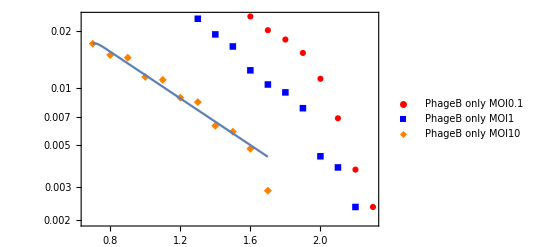

{b→277.,s→1.4172}

```mathematica
PBfitModel3=NonlinearModelFit[beginB10,{PBmodel3[0,1,b,100,s,0.09,PBMOI10INI,10,t],b==277,0<s<3},{b,s},t];
Show[PBg1,LogPlot[PBfitModel3[t],{t,0.7,1.7}]]
PBfitModel3[[1,2]]
```

```mathematica
Mean[{334.5245442504598,324.65273103451716,269.31594362029426}]
```

309.498

```mathematica
Mean[{2.9761581747874795,2.4973376745479787,1.4171960399590724}]
```

2.2969

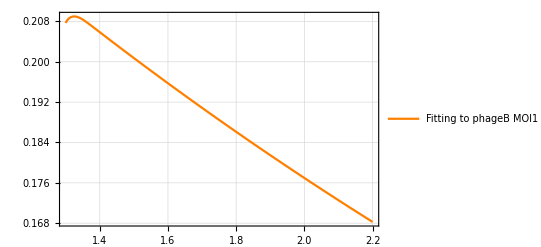

```mathematica
GphageBMOI1Early=Plot[{PBfitModel2[t]},{t,1.3,2.2},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to phageB MOI1 data"}],{0.2,0.2}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

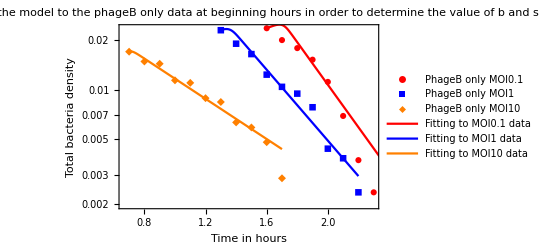

```mathematica
Show[PBg1,LogPlot[{PBfitModel1[t]},{t,1.6,2.4},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"},LegendFunction->Framed],{0.5,0.3}]],LogPlot[{PBfitModel2[t]},{t,1.3,2.2},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"},LegendFunction->Framed],{0.5,0.2}]],LogPlot[{PBfitModel3[t]},{t,0.7,1.7},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"},LegendFunction->Framed],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotLabel->"Fitting the model to the phageB only data at beginning hours in order to determine the value of b and s",FrameLabel->{"Time in hours","Total bacteria density"}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,rb_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rb*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rb*Br*(1-(B+Br)/k)};
```

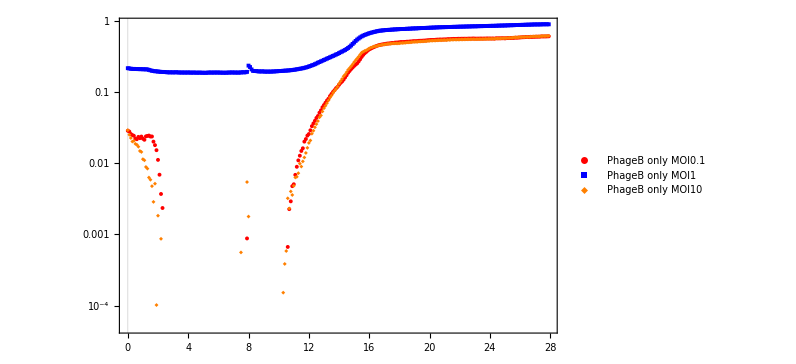

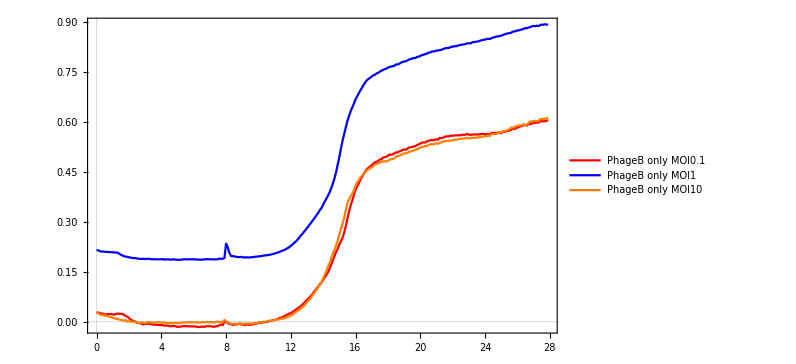

```mathematica
(* Models for different MOI, used to estimate a and rb *)
PH2[a_,k_,b_,h_,s_,p_,rb_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rb*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rb*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
PBsol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsolFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,1.3,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBsol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rb]/.Thread[stateVar2->X[t]])},X[0.7]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rb,B0,MOI}];
PBmodel4[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol4[a,k,b,h,s,p,rb,B0,MOI][t]
PBmodel5[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol5[a,k,b,h,s,p,rb,B0,MOI][t]
PBmodel6[a_,k_,b_,h_,s_,p_,rb_,B0_,MOI_,t_]:=PBsol6[a,k,b,h,s,p,rb,B0,MOI][t]
afterB01=Select[phageBMOI01,1.5<=#[[1]]&];
afterB1=Select[phageBMOI1,1.3<=#[[1]]&];
afterB10=Select[phageBMOI10,0.7<=#[[1]]&];
PBMOI01INI=Select[phageBMOI01,1.5==#[[1]]&][[1,2]];
PBMOI1INI=Select[phageBMOI1,1.3==#[[1]]&][[1,2]];
PBMOI10INI=Select[phageBMOI10,0.7==#[[1]]&][[1,2]];
PBg2=ListLogPlot[{phageBMOI01,phageBMOI1,phageBMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
PBg3=ListLinePlot[{phageBMOI01,phageBMOI1,phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1","PhageB only MOI1","PhageB only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
PBfitModel4=NonlinearModelFit[afterB01,{PBmodel4[a,k,277,100,2.273507296714341,0.09,rb,PBMOI01INI,0.1,t],0.008==a,k==0.605,0.85>rb>0.75},{{a,0.023},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 1.35183, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

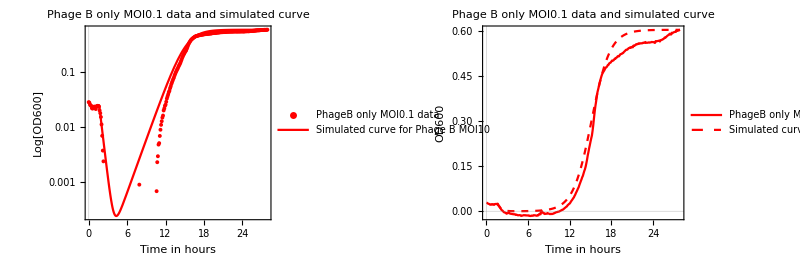

{a→0.008,k→0.605,rb→0.75}

```mathematica
PBg4=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific",PlotRange->All],PlotLabel->"Phage B only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageBMOI01},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PBfitModel4[[1,2]]
```

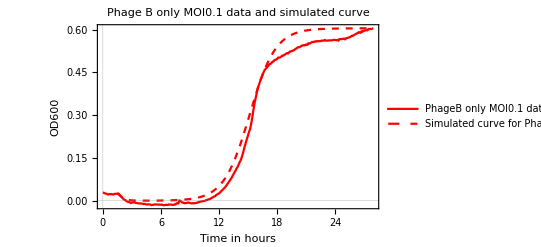

```mathematica
singlePhageG4=Show[ListLinePlot[{phageBMOI01},PlotLegends->Placed[LineLegend[{"PhageB only MOI0.1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel4[t],{t,1.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PBfitModel5=NonlinearModelFit[afterB1,{PBmodel5[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1,t],a==0.005,k==0.893,rb==0.8},{{a,0.006},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 1.28974, step size is effectively zero; singularity or stiff system suspected.

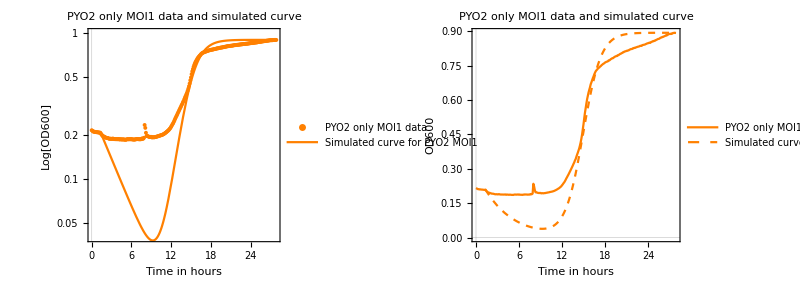

{a→0.005,k→0.893,rb→0.8}

```mathematica
PBg5=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PYO2 only MOI1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotRange->{{0,27.9},{0.04,1}}],LogPlot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPYO2 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"PYO2 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PYO2 only MOI1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPYO2 MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"PYO2 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0]
PBfitModel5[[1,2]]
```

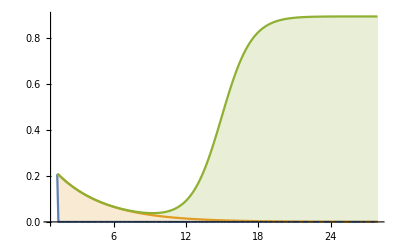

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PBsolFinal[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1]/.PBfitModel5[[1,2]])[[1;;3]]]],{t,1.3,27.9,0.1}]]]
```

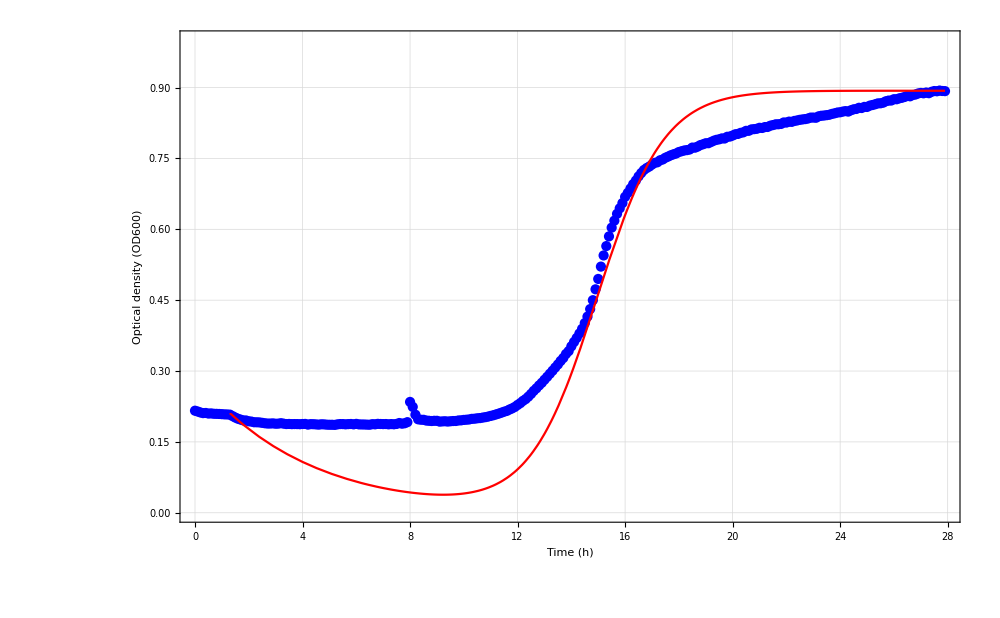

```mathematica
gf21=Show[ListPlot[{phageBMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"PYO2-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

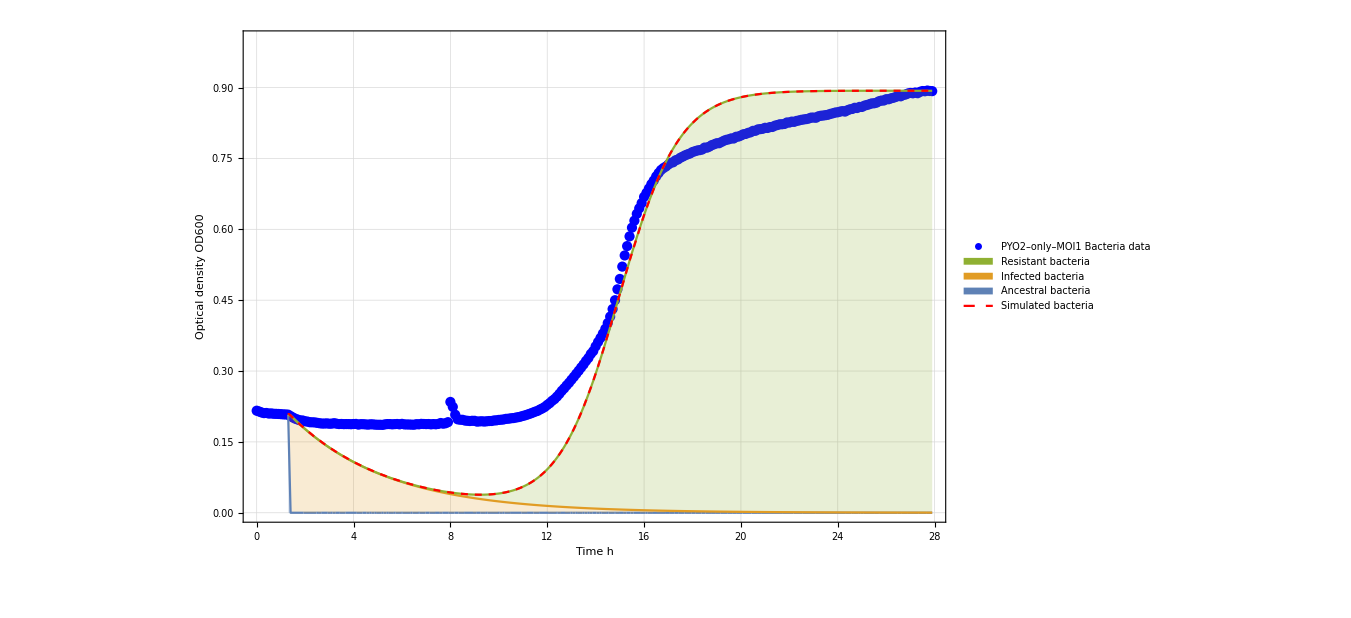
-Graphics-B

```mathematica
gf22=Labeled[Show[ListPlot[{phageBMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"PYO2–only–MOI1 Bacteria data"}],{0.35,0.9}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PBsolFinal[a,k,460,100,0.25,0.09,rb,PBMOI1INI,1]/.PBfitModel5[[1,2]])[[1;;3]]]],{t,1.3,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.22,0.7}],LabelStyle->{35,FontFamily->"Times"}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.22,0.5}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],FrameLabel->{"Time h","Optical density OD600"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}],Style["B","Section",Bold,50,Black,FontFamily->"Times"],{{Top,Left}}]
```

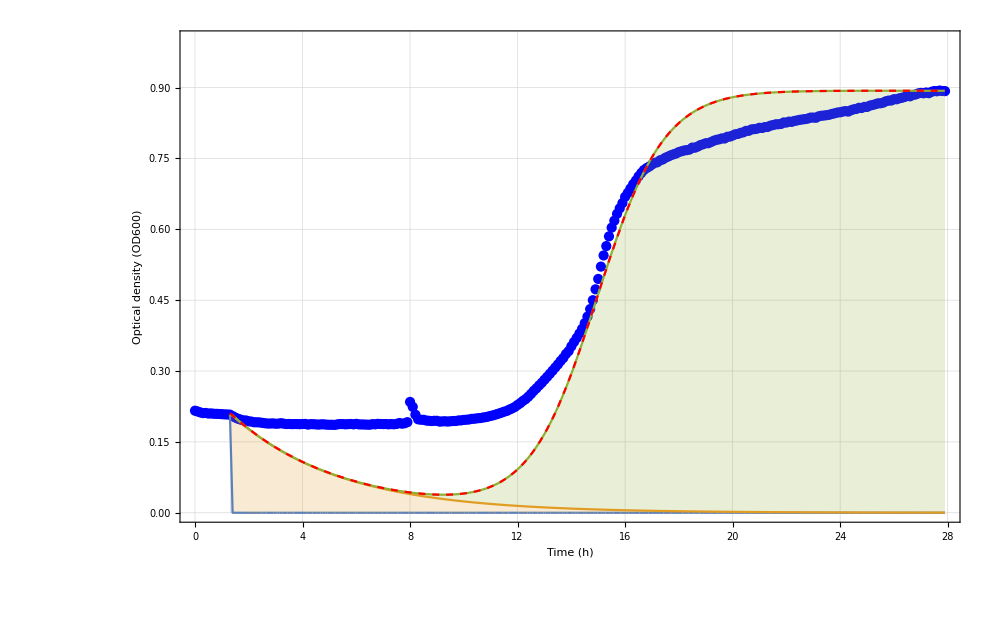
B
-Graphics-
-Graphics-

```mathematica
gf2=Grid[{{Style["B",FontFamily->"Times",FontSize->30]},{gf21},{gf22}}]
```

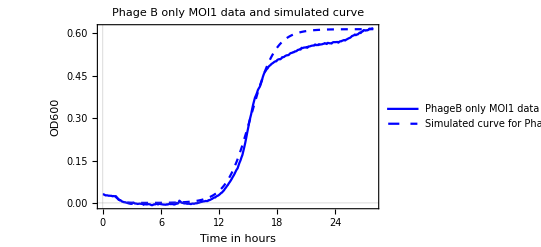

```mathematica
singlePhageG5=Show[ListLinePlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PhageB only MOI1 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel5[t],{t,1.3,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PBfitModel6=NonlinearModelFit[afterB10,{PBmodel6[a,k,309.49773963509045,100,2.273507296714341,0.09,rb,PBMOI10INI,10,t],0.008==a,k==0.61,0.87>rb>0.86},{{a,0.023},k,{rb,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.654981, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

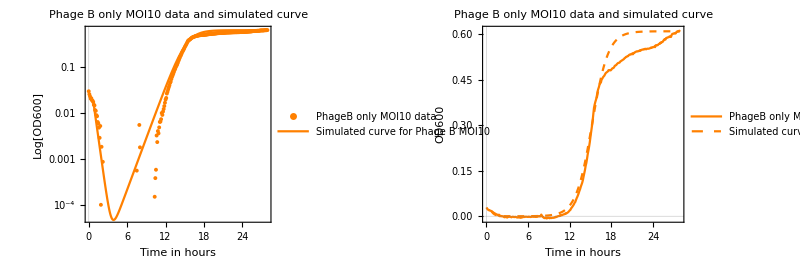

{a→0.008,k→0.61,rb→0.86}

```mathematica
PBg6=GraphicsGrid[{{Show[ListLogPlot[{phageBMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"}],Show[ListLinePlot[{phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PBfitModel6[[1,2]]
```

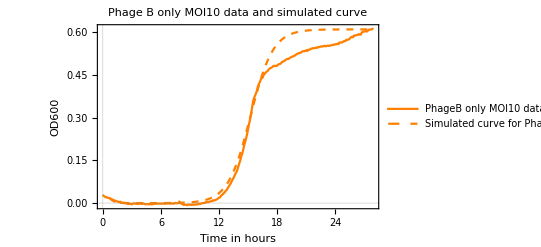

```mathematica
singlePhageG6=Show[ListLinePlot[{phageBMOI10},PlotLegends->Placed[LineLegend[{"PhageB only MOI10 data"},LegendFunction->Framed],{0.75,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PBfitModel6[t],{t,0.7,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage B MOI10"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage B only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
(* a2 *)
```

```mathematica
Mean[{0.0030000521236647165,0.00446884398942673,0.00699999756671431}]
```

0.00482296

```mathematica
(* rb *)
```

```mathematica
Mean[{0.7500000146395103,0.7900009634864262,0.860000028893722}]
```

0.8

```mathematica
GraphicsGrid[{{PBg4},{PBg5},{PBg6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

## Estimate phage-C-specific parameter values

#### Fitting using data from phage C only experiment

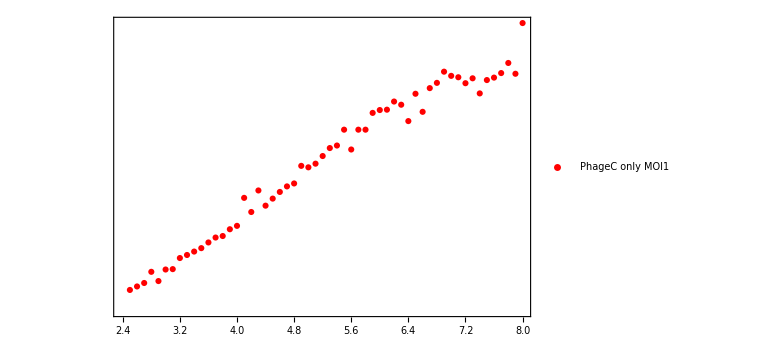

```mathematica
experimentData=Import["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\experimentNew.xlsx"];
TIME=Table[i,{i,0,27.9,0.1}];
phageCMOI01=Transpose[{TIME,experimentData[[7,1]]}];
phageCMOI1=Transpose[{TIME,experimentData[[8,1]]}];
phageCMOI10=Transpose[{TIME,experimentData[[9,1]]}];
beginC01=Select[phageCMOI01,0.5<=#[[1]]≤8&];
beginC1=Select[phageCMOI1,2.5<=#[[1]]≤8&];
beginC10=Select[phageCMOI10,1.3<=#[[1]]≤8&];PCg1=ListLogPlot[{beginC1},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageC only MOI1"},LegendFunction->Framed],{0.2,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange}]
```

```mathematica
PH[a_,k_,b_,h_,s_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+0.81*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+0.81*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PCsol1=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[0.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0.5,8},{a,k,b,h,s,p,B0,MOI}];
PCsol2=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,2.5,8},{a,k,b,h,s,p,B0,MOI}];
PCsol3=ParametricNDSolveValue[{{X'[t]==(PH[a,k,b,h,s,p]/.Thread[stateVar->X[t]])},X[1.3]=={B0,0,0,B0*MOI,B0}},Bt,{t,1.3,8},{a,k,b,h,s,p,B0,MOI}];
PCmodel1[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol1[a,k,b,h,s,p,B0,MOI][t]
PCmodel2[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol2[a,k,b,h,s,p,B0,MOI][t]
PCmodel3[a_,k_,b_,h_,s_,p_,B0_,MOI_,t_]:=PCsol3[a,k,b,h,s,p,B0,MOI][t]
```

```mathematica
(* Initial bacteria values *)
PCMOI01INI=Select[phageCMOI01,0.5==#[[1]]&][[1,2]];
PCMOI1INI=Select[phageCMOI1,2.5==#[[1]]&][[1,2]];
PCMOI10INI=Select[phageCMOI10,1.3==#[[1]]&][[1,2]];
```

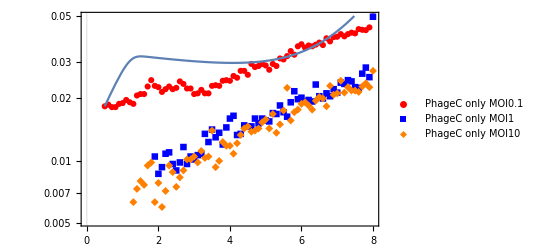

{b→129.998,s→0.0499989}

```mathematica
PCfitModel1=NonlinearModelFit[beginC01,{PCmodel1[0.008,1,b,200,s,0.09,PCMOI01INI,0.1,t],130>b>0,0<s<0.05},{b,s},t];
Show[PCg1,LogPlot[PCfitModel1[t],{t,0.5,8}]]
PCfitModel1[[1,2]]
```

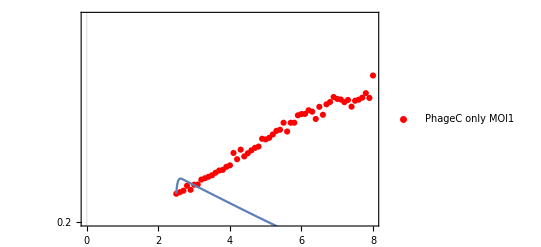

{b→460.,s→0.0200001}

```mathematica
PCfitModel2=NonlinearModelFit[beginC1,{PCmodel2[0.008,1,b,200,s,0.09,PCMOI1INI,1,t],b==460,0.02<s},{b,s},t];
Show[PCg1,LogPlot[PCfitModel2[t],{t,2.5,8},PlotRange->All],PlotRange->{{0,8},{0.2,0.25}//Log}]
PCfitModel2[[1,2]]
```

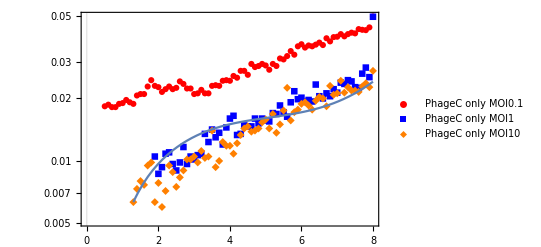

{b→20.1643,s→0.0100171}

```mathematica
PCfitModel3=NonlinearModelFit[beginC10,{PCmodel3[0.008,1,b,200,s,0.09,PCMOI10INI,10,t],100>b>20,0.01<s<3},{b,s},t];
Show[PCg1,LogPlot[PCfitModel3[t],{t,1.3,8}]]
PCfitModel3[[1,2]]
```

```mathematica
(* b *)
```

```mathematica
Mean[{279.2900341706015,276.221780102454,273.4717985074662}]
```

276.328

```mathematica
(* s *)
```

```mathematica
Mean[{1.0795990086697207,1.0427361634232657,1.0203150092631175}]
```

1.04755

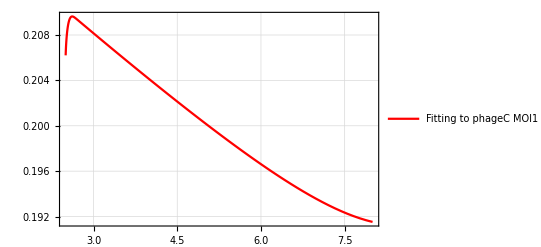

```mathematica
GphageCMOI1Early=Plot[{PCfitModel2[t]},{t,2.5,8},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to phageC MOI1 data"}],{0.2,0.1}],PlotTheme->"Detailed",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

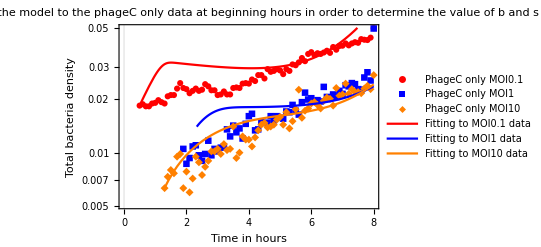

```mathematica
Show[PCg1,LogPlot[{PCfitModel1[t]},{t,0.5,8},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Fitting to MOI0.1 data"},LegendFunction->Framed],{0.5,0.3}]],LogPlot[{PCfitModel2[t]},{t,1.9,8},PlotStyle->Blue,PlotLegends->Placed[LineLegend[{"Fitting to MOI1 data"},LegendFunction->Framed],{0.5,0.2}]],LogPlot[{PCfitModel3[t]},{t,1.3,8},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Fitting to MOI10 data"},LegendFunction->Framed],{0.5,0.1}]],Frame->True,PlotTheme->"Scientific",ImageSize->Full,BaseStyle->{Bold,14},FrameStyle->{Bold,Black},PlotLabel->"Fitting the model to the phageC only data at beginning hours in order to determine the value of b and s",FrameLabel->{"Time in hours","Total bacteria density"}]
```

```mathematica
PH2[a_,k_,b_,h_,s_,p_,rc_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rc*Br*(1-(B+Br)/k)};
```

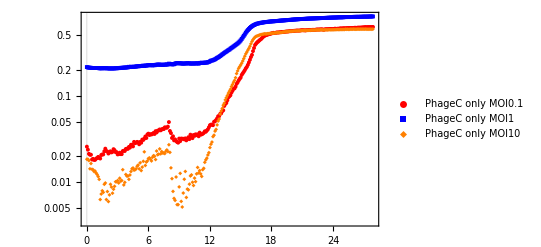

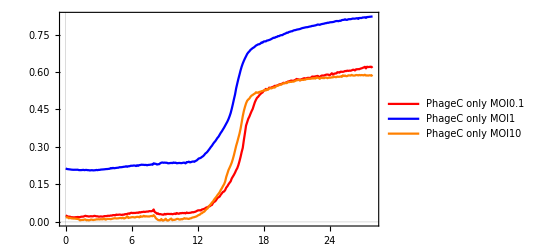

```mathematica
(* Models for different MOI, used to estimate a and rb *)
PH2[a_,k_,b_,h_,s_,p_,rc_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+rc*Br*(1-(B+Br)/k)};
stateVar2={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar2[t]];
PCsol4=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[0]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol5=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol5New=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},{B,Bt},{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsolFinal=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[2.5]=={B0,0,0,B0*MOI,B0}},{B[t],Bi[t],Br[t],Bt[t]},{t,2.5,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCsol6=ParametricNDSolveValue[{{X'[t]==(PH2[a,k,b,h,s,p,rc]/.Thread[stateVar2->X[t]])},X[0.8]=={B0,0,0,B0*MOI,B0}},Bt,{t,0,27.9},{a,k,b,h,s,p,rc,B0,MOI}];
PCmodel4[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol4[a,k,b,h,s,p,rc,B0,MOI][t]
PCmodel5[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol5[a,k,b,h,s,p,rc,B0,MOI][t]
PCmodel6[a_,k_,b_,h_,s_,p_,rc_,B0_,MOI_,t_]:=PCsol6[a,k,b,h,s,p,rc,B0,MOI][t]
afterC01=Select[phageCMOI01,0<=#[[1]]&];
afterC1=Select[phageCMOI1,2.5<=#[[1]]&];
afterC10=Select[phageCMOI10,0.8<=#[[1]]&];
PCMOI01INI=Select[phageCMOI01,0==#[[1]]&][[1,2]];
PCMOI1INI=Select[phageCMOI1,2.5==#[[1]]&][[1,2]];
PCMOI10INI=Select[phageCMOI10,0.8==#[[1]]&][[1,2]];
PCg2=ListLogPlot[{phageCMOI01,phageCMOI1,phageCMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI0.1","PhageC only MOI1","PhageC only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
PCg3=ListLinePlot[{phageCMOI01,phageCMOI1,phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1","PhageC only MOI1","PhageC only MOI10"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red,Blue,Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}]
```

```mathematica
PCfitModel4=NonlinearModelFit[afterC01,{PCmodel4[a,k,276.3278709268406,100,1.0475500604520347,0.09,rc,PCMOI01INI,0.1,t],0.008==a,k==0.62,0.85>rc>0.8},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

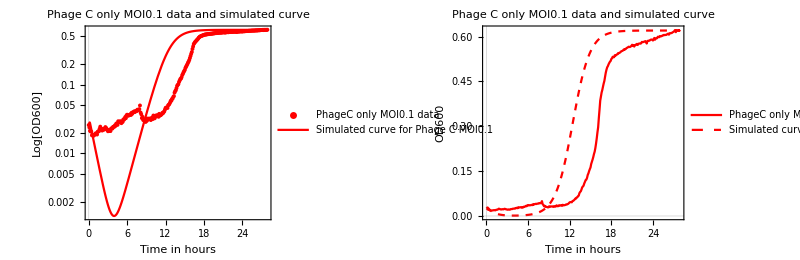

{a→0.008,k→0.62,rc→0.8}

```mathematica
PCg4=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI01},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel4[t],{t,0,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[
{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI01},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.76,0.15}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel4[t],{t,0,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PCfitModel4[[1,2]]
```

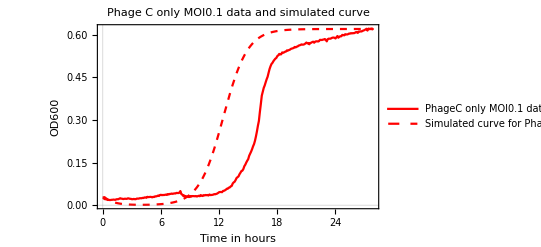

```mathematica
singlePhageG7=Show[ListLinePlot[{phageCMOI01},PlotLegends->Placed[LineLegend[{"PhageC only MOI0.1 data"},LegendFunction->Framed],{0.76,0.15}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel4[t],{t,0,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI0.1"},LegendFunction->Framed],{0.25,0.8}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI0.1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PCfitModel5=NonlinearModelFit[afterC1,{PCmodel5[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1,t],0.005==a,k==0.695,rc==0.81},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 2.48949, step size is effectively zero; singularity or stiff system suspected.

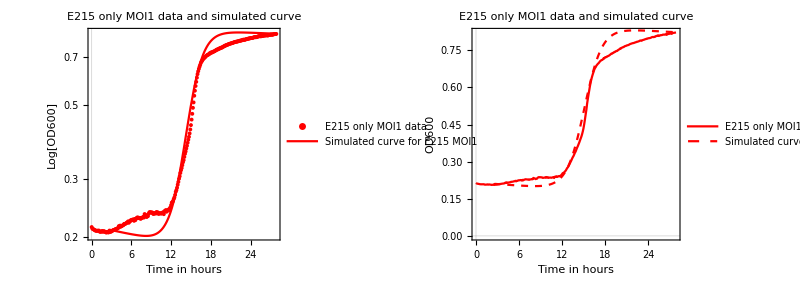

{a→0.0045,k→0.66,rc→0.81}

```mathematica
PCg5=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI1},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"E215 only MOI1 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Simulated curve for\nE215 MOI1"},LegendFunction->Framed],{0.67,0.4}],PlotTheme->"Scientific"],PlotLabel->"E215 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"E215 only MOI1 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Red},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Dashed,Red},PlotLegends->Placed[LineLegend[{"Simulated curve for\nE215 MOI1"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"E215 only MOI1 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full,Frame->True,Alignment->Center,Spacings->0]
PCfitModel5[[1,2]]
```

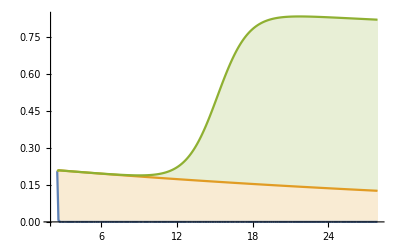

```mathematica
StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PCsolFinal[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1]/.PCfitModel5[[1,2]])[[1;;3]]]],{t,2.5,27.9,0.1}]]]
```

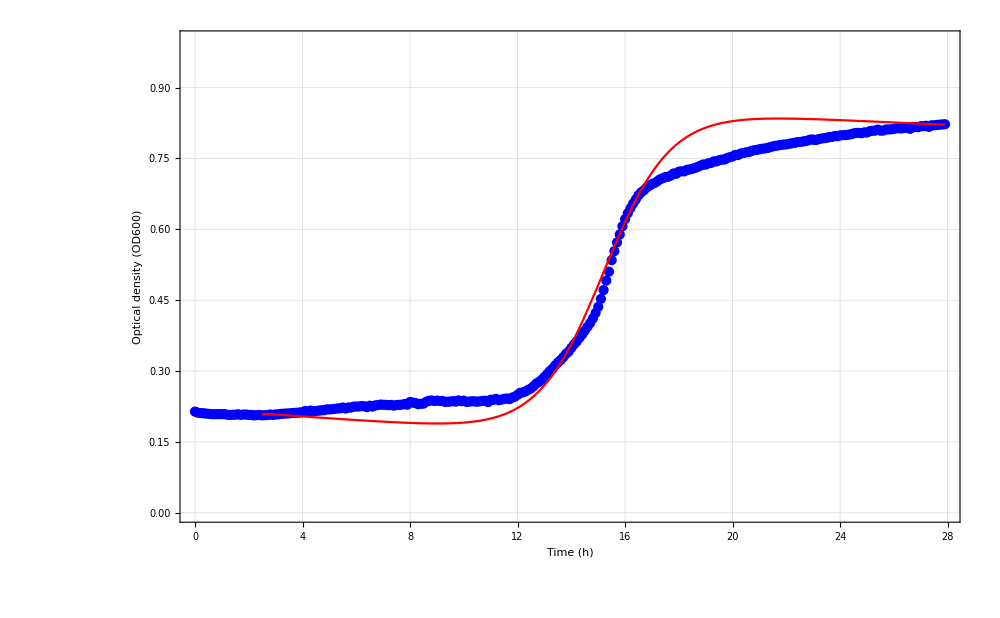

```mathematica
gf31=Show[ListPlot[{phageCMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"E215-only-MOI1 Bacteria data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,23},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.25,0.6}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black,FontFamily->"Times"}],FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}]
```

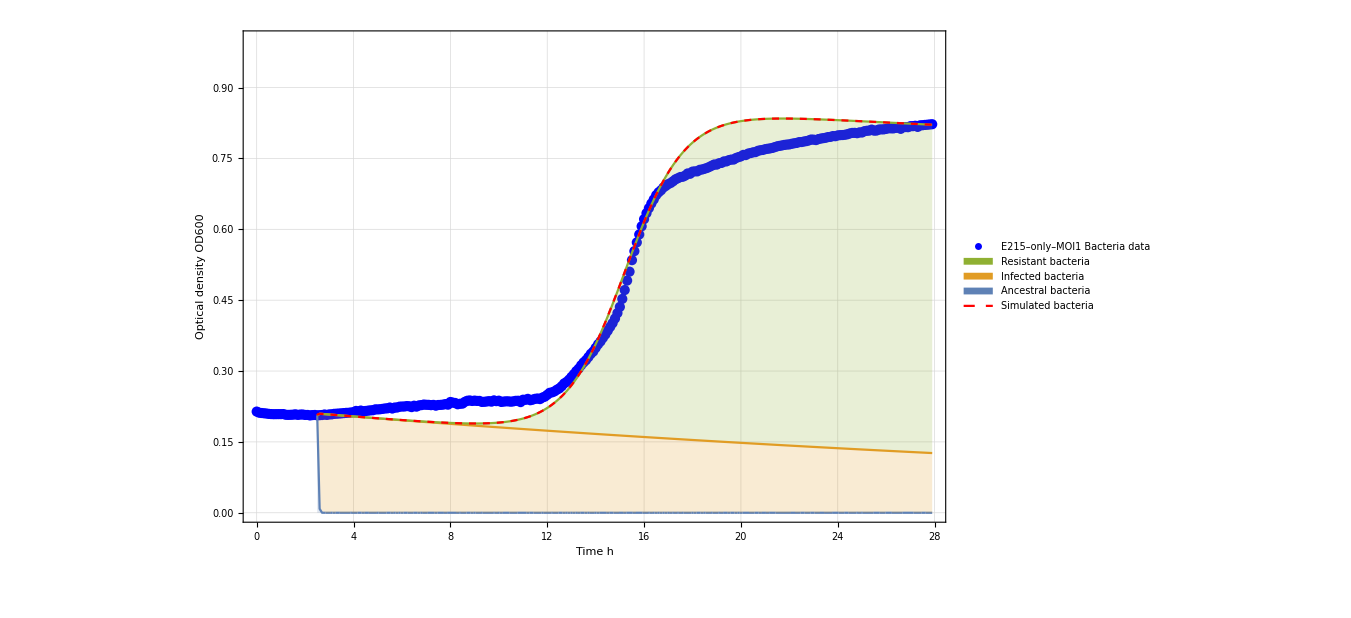
-Graphics-C

```mathematica
gf32=Labeled[Show[ListPlot[{phageCMOI1},PlotLegends->Placed[PointLegend[{Directive[Blue,AbsolutePointSize[10]]},{"E215–only–MOI1 Bacteria data"}],{0.35,0.9}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],StackedListPlot[Transpose[Table[Map[{t,#}&,Evaluate[(PCsolFinal[a,k,460,200,0.02,0.09,rc,PCMOI1INI,1]/.PCfitModel5[[1,2]])[[1;;3]]]],{t,2.5,27.9,0.1}]],PlotLegends->Placed[SwatchLegend[{"Ancestral bacteria","Infected bacteria","Resistant bacteria"}],{0.22,0.7}],LabelStyle->{35,FontFamily->"Times"}],Plot[PCfitModel5[t],{t,2.5,27.9},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"Simulated bacteria"}],{0.22,0.5}],PlotTheme->"Detailed",GridLines->Automatic,BaseStyle->{Bold,35},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,35,Black,FontFamily->"Times"}],FrameLabel->{"Time h","Optical density OD600"},ImageSize->1000,PlotRange-> {{0,27.9},{0,1}}],Style["C","Section",Bold,50,Black,FontFamily->"Times"],{{Top,Left}}]
```

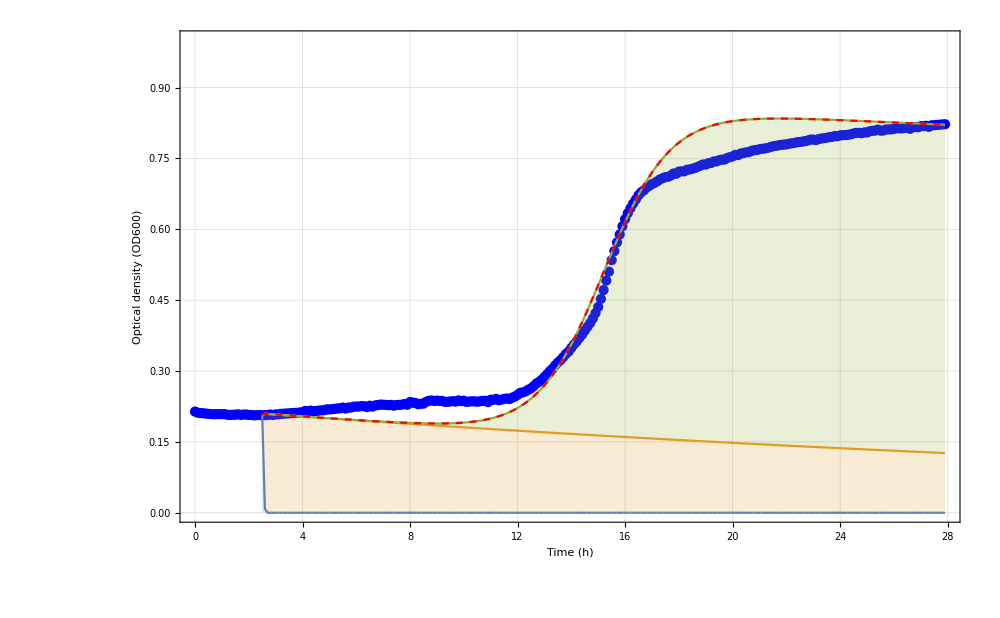
C
-Graphics-
-Graphics-

```mathematica
gf3=Grid[{{Style["C",FontFamily->"Times",FontSize->30]},{gf31},{gf32}}]
```

```mathematica
Through[PCsol5New[0.008,0.88,460,200,0.001,0.09,0.81,PCMOI1INI,1][20]]
```

{-1.20298×10^-15,1.05424}

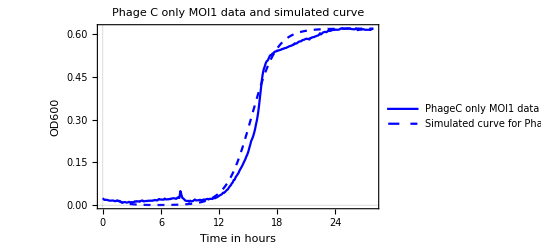

```mathematica
singlePhageG8=Show[ListLinePlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"PhageC only MOI1 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Blue},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel5[t],{t,1.4,27.9},PlotStyle->{Dashed,Blue},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI1"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI1 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
PCfitModel6=NonlinearModelFit[afterC10,{PCmodel6[a,k,276.3278709268406,100,1.0475500604520347,0.09,rc,PCMOI10INI,10,t],0.008==a,k==0.59,0.87>rc>0.86},{{a,0.023},k,{rc,0.6783536287519775}},t];
```

ParametricNDSolveValue::ndsz: At t == 0.728523, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

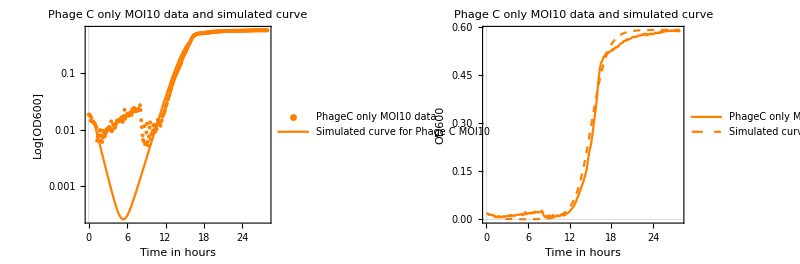

{a→0.008,k→0.59,rc→0.86}

```mathematica
PCg6=GraphicsGrid[{{Show[ListLogPlot[{phageCMOI10},PlotMarkers->{Automatic,Tiny},PlotLegends->Placed[PointLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.7,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],LogPlot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.7,0.5}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data and simulated curve",FrameLabel->{"Time in hours","Log[OD600]"},PlotRange->All],Show[ListLinePlot[{phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,14},FrameStyle->{Bold,Black}],Plot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data and simulated curve",FrameLabel->{"Time in hours","OD600"}]}},ImageSize->Full]
PCfitModel6[[1,2]]
```

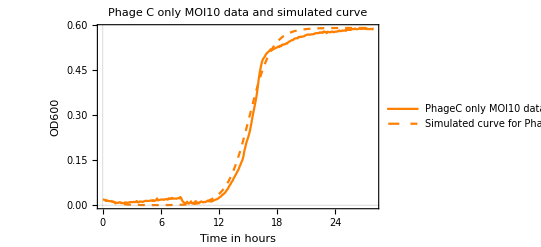

```mathematica
singlePhageG9=Show[ListLinePlot[{phageCMOI10},PlotLegends->Placed[LineLegend[{"PhageC only MOI10 data"},LegendFunction->Framed],{0.77,0.2}],Frame->True,PlotTheme->"Scientific",PlotStyle->{Orange},BaseStyle->{Bold,8},FrameStyle->{Bold,Black}],Plot[PCfitModel6[t],{t,0.8,27.9},PlotStyle->{Dashed,Orange},PlotLegends->Placed[LineLegend[{"Simulated curve for\nPhage C MOI10"},LegendFunction->Framed],{0.26,0.85}],PlotTheme->"Scientific"],PlotLabel->"Phage C only MOI10 data \n and simulated curve",FrameLabel->{"Time in hours","OD600"},ImageSize->Full]
```

```mathematica
Mean[{0.8,0.7800000138400899,0.8600000337190107}]
```

0.813333

```mathematica
GraphicsGrid[{{PCg4},{PCg5},{PCg6}},Alignment->Center,Spacings->0,Frame->True,ImageSize->Full]
```

-Graphics-

-Graphics-

-Graphics-

## Single with simultaneous

```mathematica
gsinsim=Grid[{{gf12,gf22,gf32},{GABSIMOI1,GACSIMOI1,GBCSIMOI1}},Spacings->5];
```

```mathematica
Export["C:\\Users\\zhiyu\\Dropbox\\Stan Yu\\Phage project\\simulation\\Image_final_12_1_23\\Figure_4_In_vitro_and_in_silico_time-kill_kinetics.pdf",gsinsim,Spacings->5]
```

C:\Users\zhiyu\Dropbox\Stan Yu\Phage project\simulation\Image_final_12_1_23\Figure_4_In_vitro_and_in_silico_time-kill_kinetics.pdf

## Summary

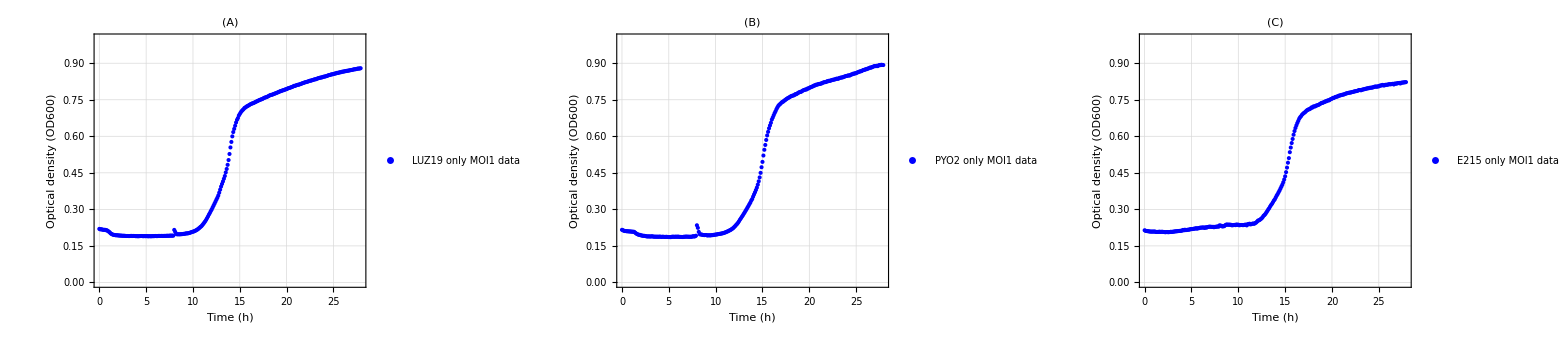

```mathematica
GraphicsGrid[{{ListPlot[{phageAMOI1},PlotLegends->Placed[LineLegend[{"LUZ19 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(A)"],ListPlot[{phageBMOI1},PlotLegends->Placed[LineLegend[{"PYO2 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotStyle->{Blue},PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(B)"],ListPlot[{phageCMOI1},PlotLegends->Placed[LineLegend[{"E215 only MOI1 data"}],{0.25,0.6}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue},GridLines->Automatic,BaseStyle->{Bold,14},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Optical density (OD600)"},ImageSize->Full,PlotRange-> {{0,27.9},{0,1}},PlotLabel->"(C)"]}},Alignment->Center,Spacings->0]
```

## Different phage lysis rates

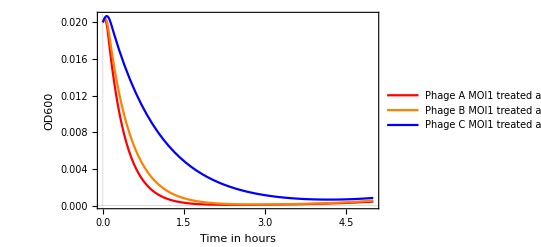

```mathematica
Module[{PH,stateVar,X,solution},
PH[a_,k_,b_,h_,s_,p_,r_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+r*Br*(1-(B+Br)/k),-p*P+h*s*Bi,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+r*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
solution=ParametricNDSolveValue[{{X'[t]==(PH[0.008,0.6,277,100,s,0.09,r]/.Thread[stateVar->X[t]])},X[0]=={B0,0,0,B0,B0}},Bt[t],{t,0,27.9},{s,r,B0}];
Plot[{solution[2.98,0.77,0.02],solution[2.3,0.8,0.02],solution[1.05,0.81,0.02]},{t,0,5},PlotTheme->"Scientific",PlotStyle->{Red,Orange,Blue},BaseStyle->{Bold,14},ImageSize->Full,PlotRange->All,PlotLegends->Placed[LineLegend[{"Phage A MOI1 treated at hour 0","Phage B MOI1 treated at hour 0","Phage C MOI1 treated at hour 0"},LegendFunction->Framed],{0.5,0.8}],FrameLabel->{"Time in hours","OD600"}]
]
```

## Single Phage Summary

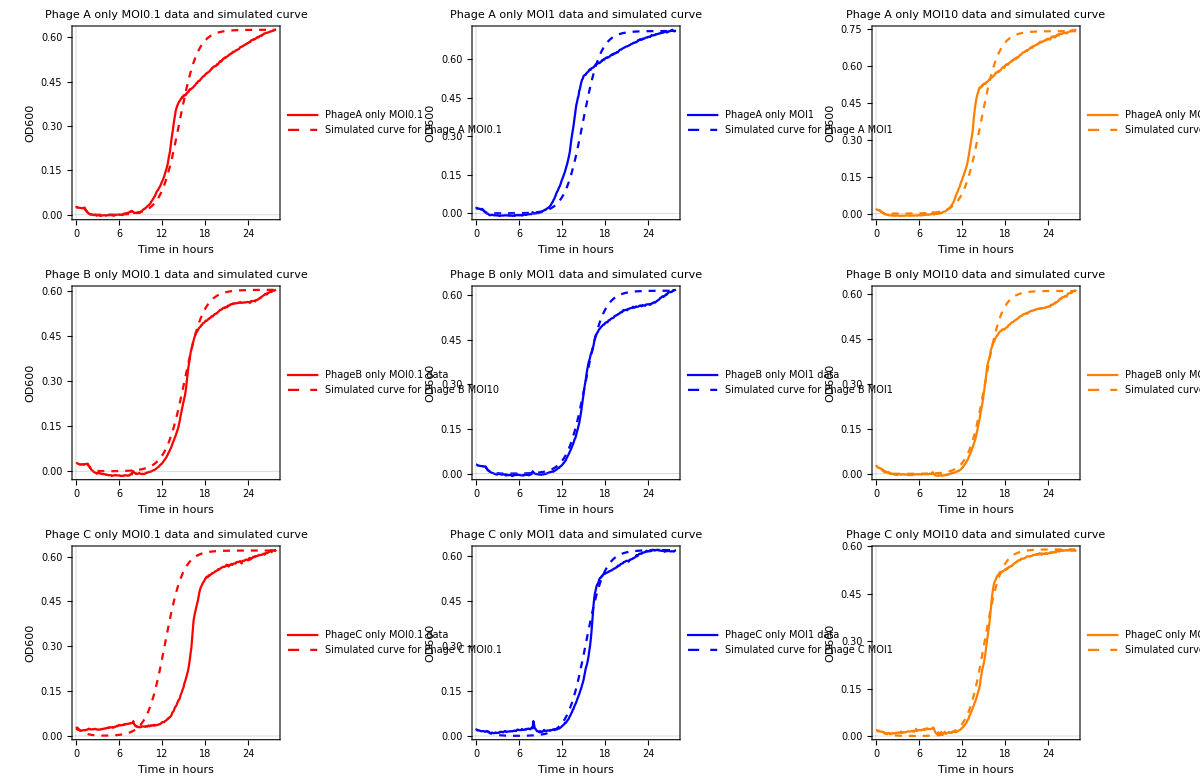

```mathematica
GraphicsGrid[{{singlePhageG1,singlePhageG2,singlePhageG3},{singlePhageG4,singlePhageG5,singlePhageG6},{singlePhageG7,singlePhageG8,singlePhageG9}},ImageSize->Full,Spacings->0,Frame->True,Alignment->Center]
```

## MOI1

```mathematica
GraphicsGrid[{{g5},{PBg5},{PCg5}},ImageSize->Full,Alignment->Center,Spacings->0,Frame->True]
```

-Graphics-

```mathematica
A=1
B=2
```

1

2

```mathematica
{{□, □}}
```

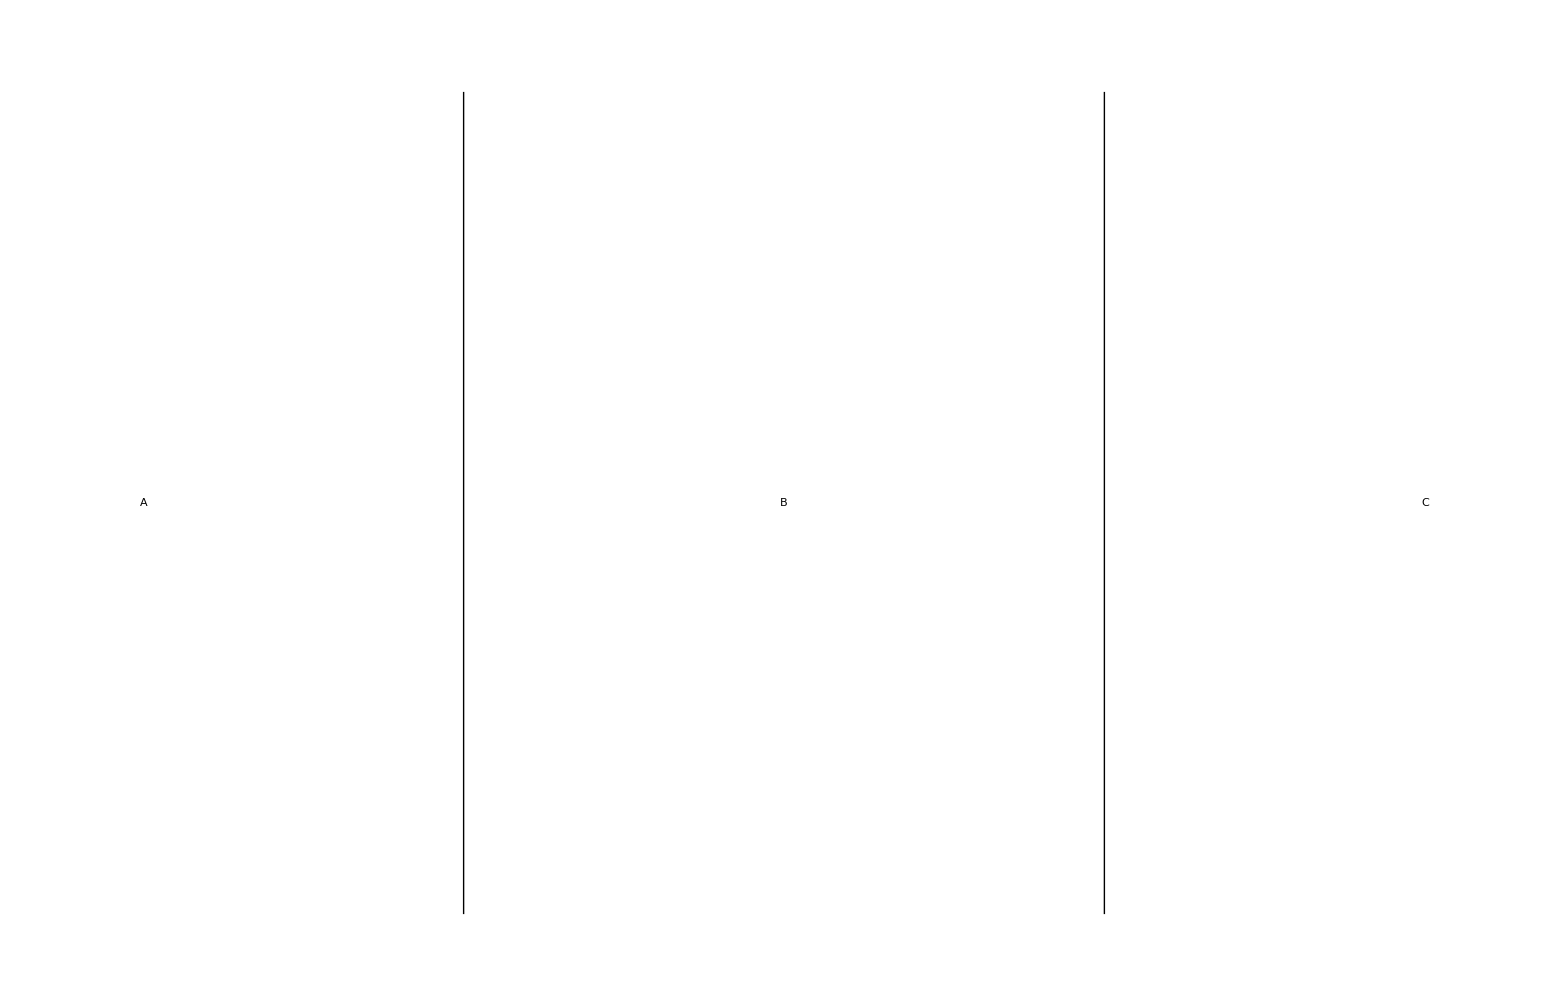

```mathematica
GraphicsGrid[{{gf1,gf2,gf3}},Alignment->Center,ImageSize->3200,Dividers->{{False,True,True,False},False}]
```

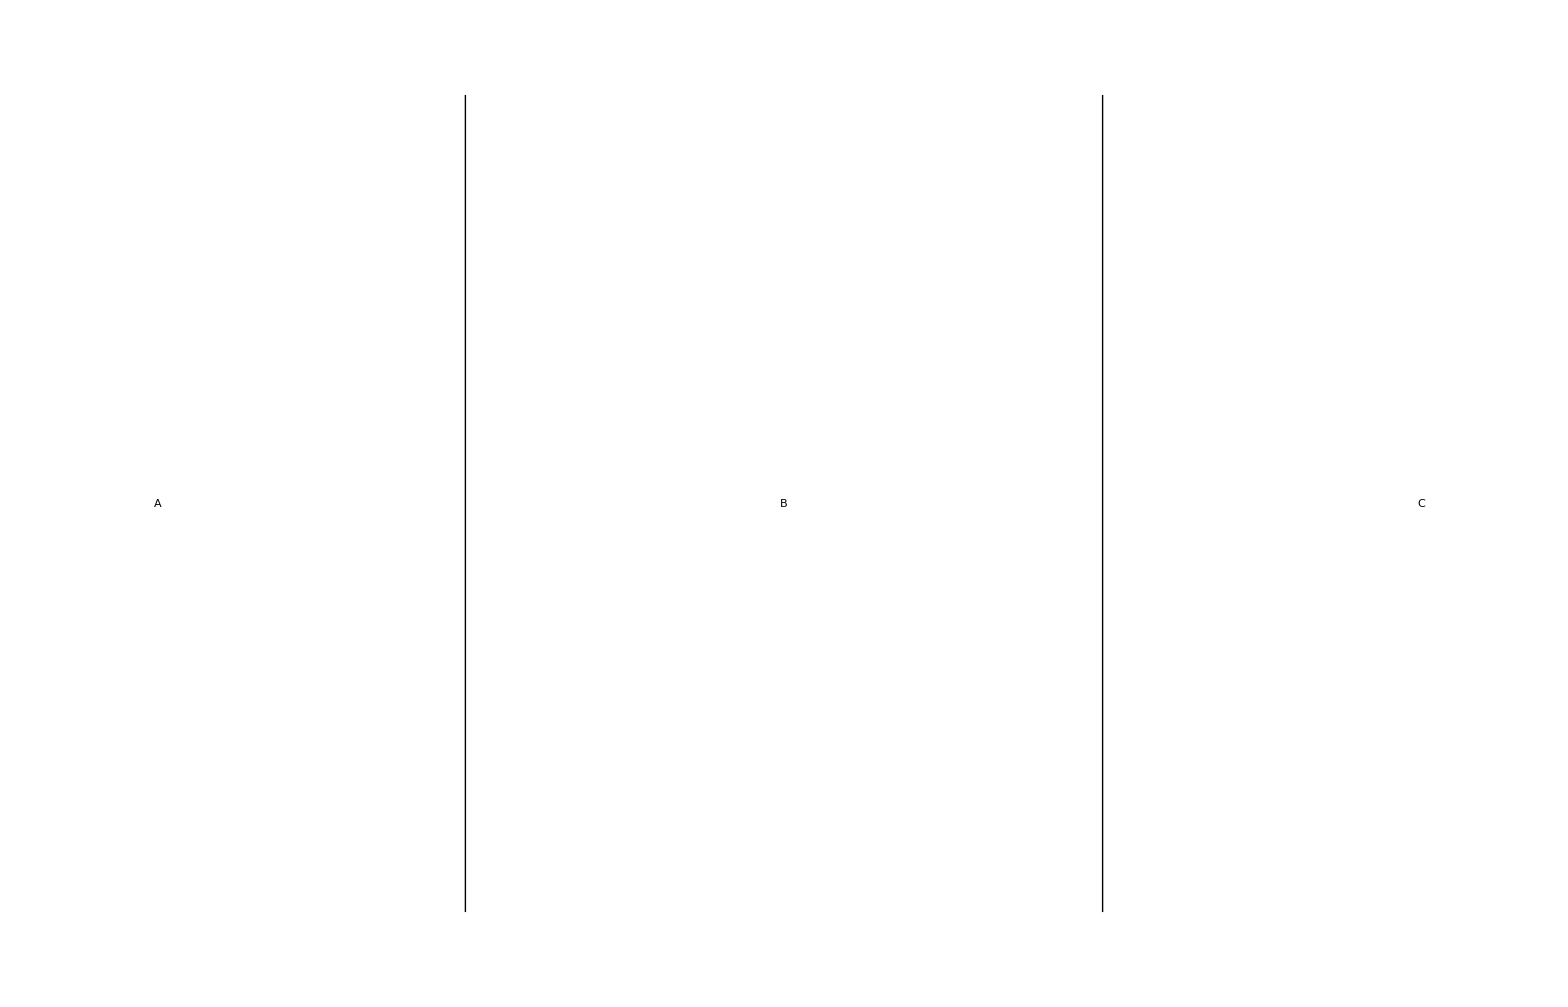

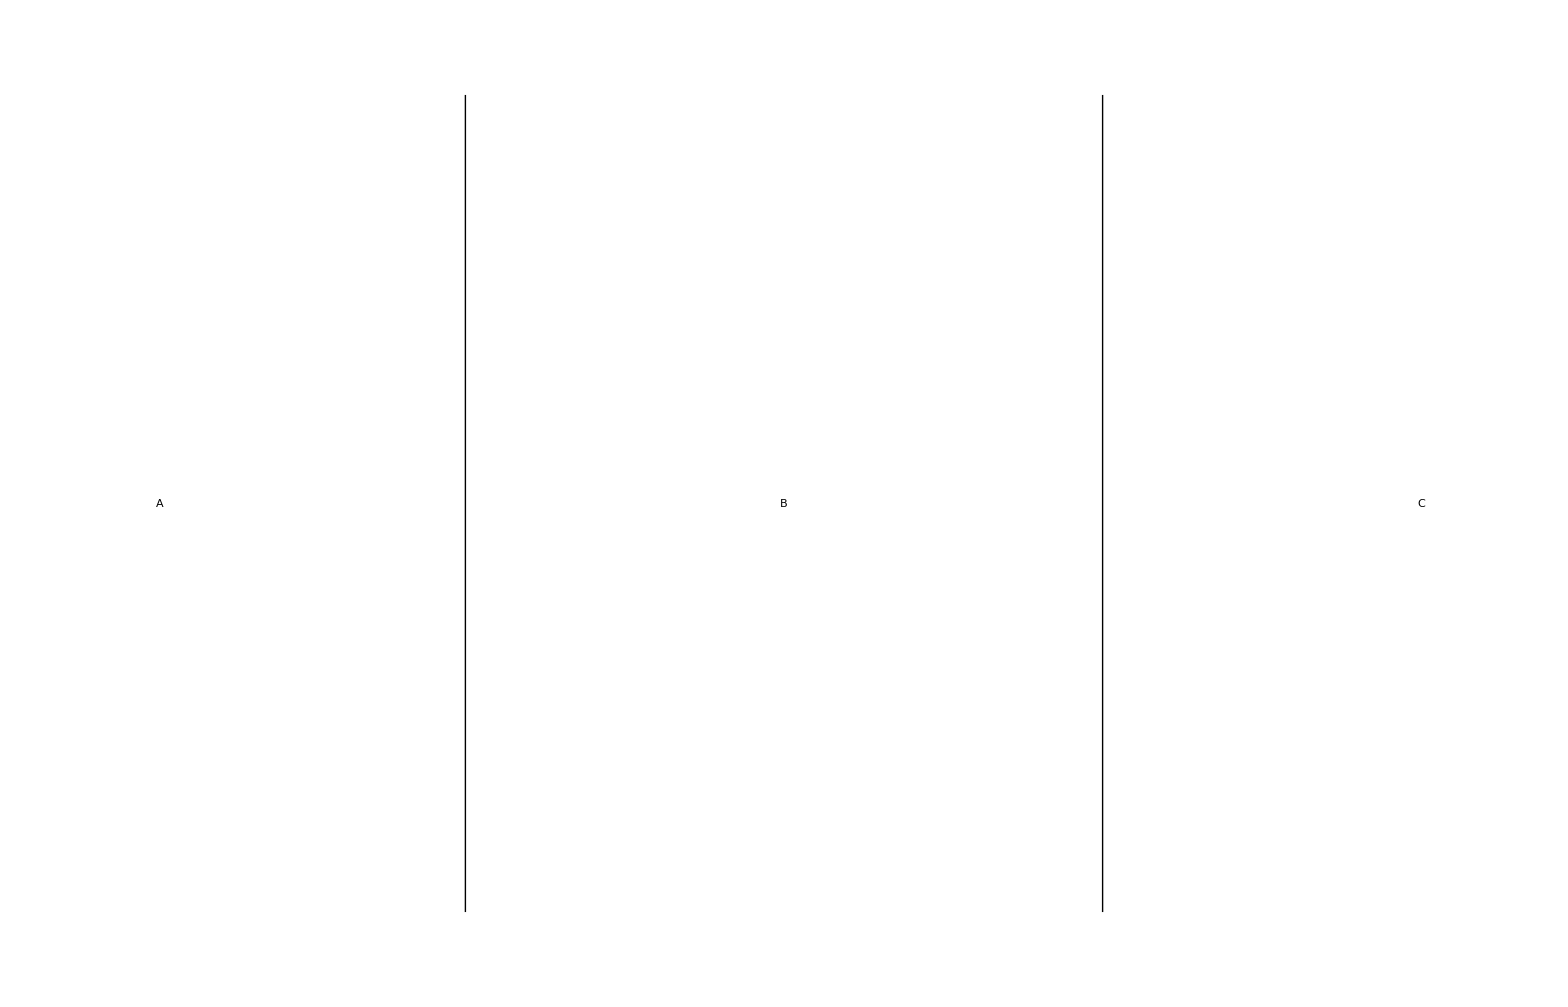

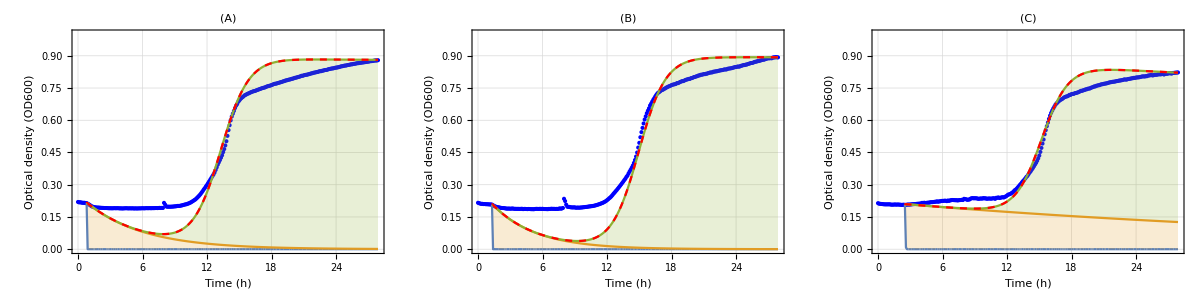

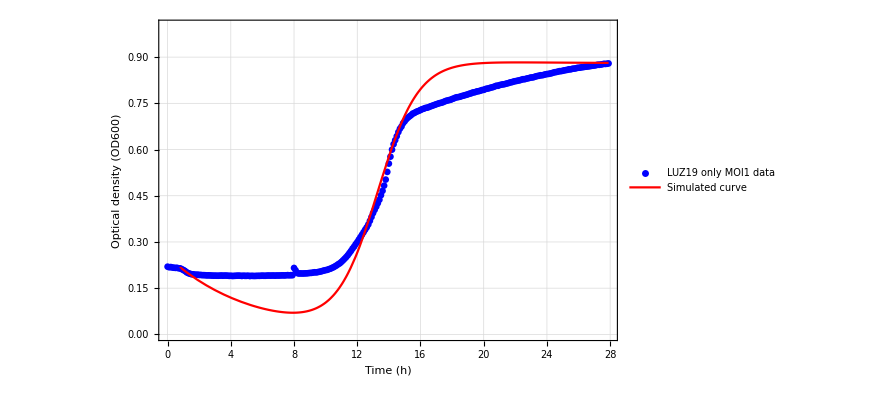
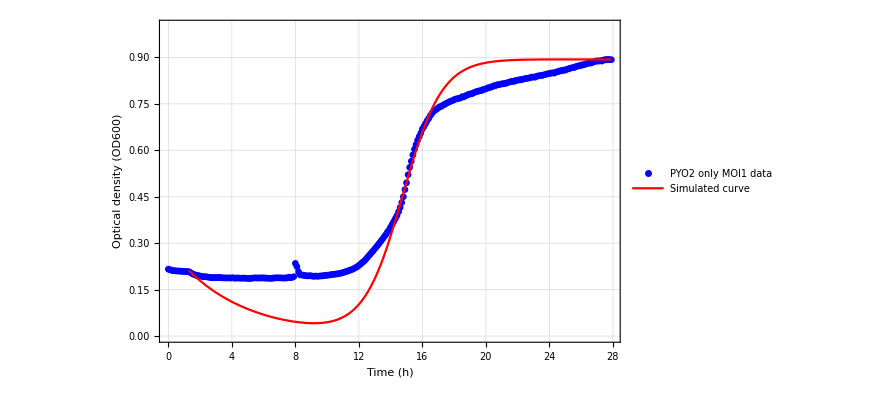
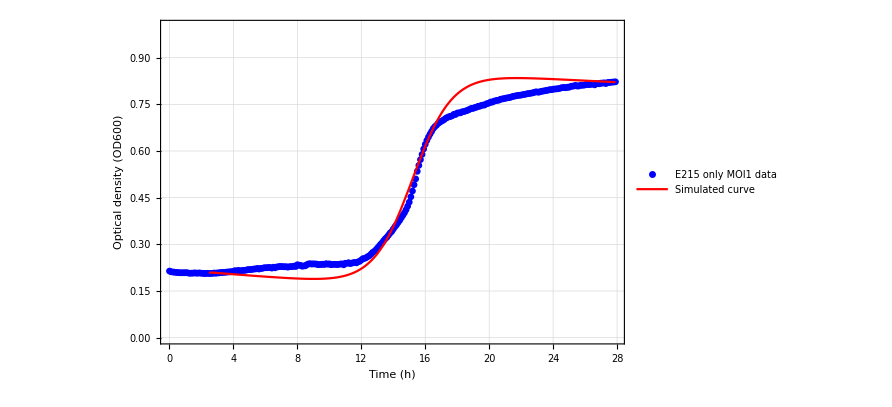
```mathematica
{{(A), (B), (C)}, {-Graphics-, -Graphics-, -Graphics-}}
```

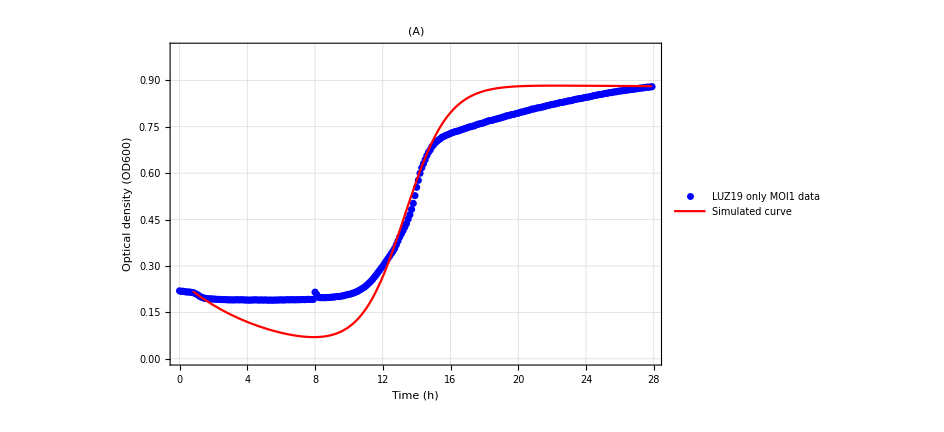

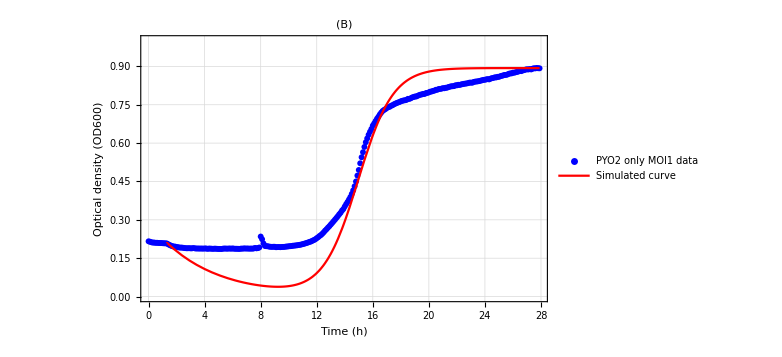

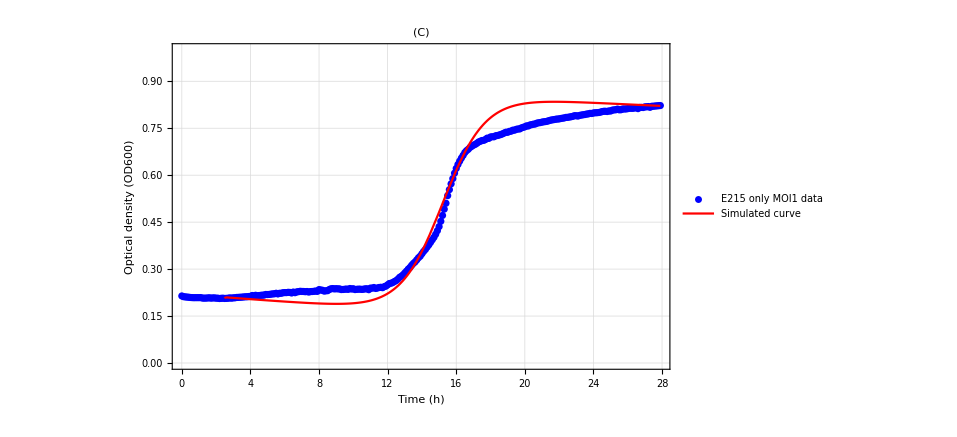

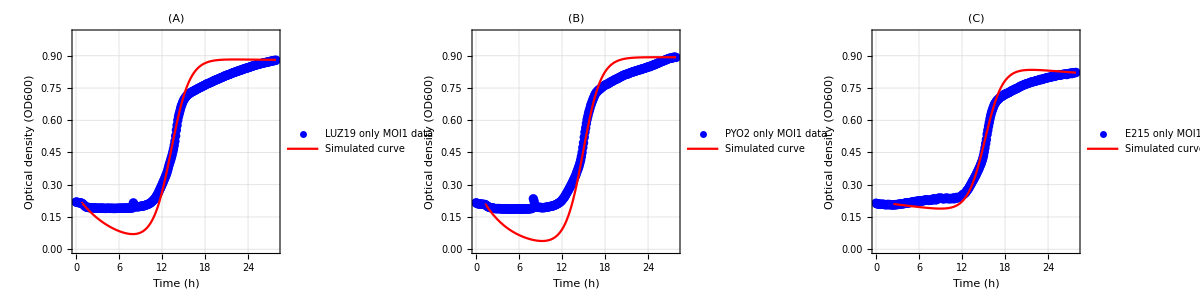

## MOI1 early

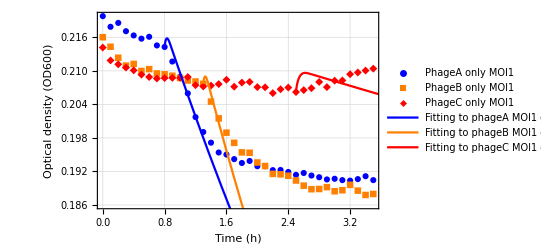

```mathematica
Show[ListPlot[{Select[phageAMOI1,0<=#[[1]]≤3.5&],Select[phageBMOI1,0<=#[[1]]≤3.5&],Select[phageCMOI1,0<=#[[1]]≤3.5&]},PlotMarkers->Automatic,PlotLegends->Placed[PointLegend[{"PhageA only MOI1","PhageB only MOI1","PhageC only MOI1"}],{0.2,0.5}],Frame->True,PlotTheme->"Detailed",PlotStyle->{Blue,Orange,Red},BaseStyle->{Bold,14},GridLines->Automatic,FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotRange->All],GphageAMOI1Early,GphageBMOI1Early,GphageCMOI1Early,ImageSize->Full,FrameLabel->{"Time (h)","Optical density (OD600)"}]
```

## Delayed differential equation

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

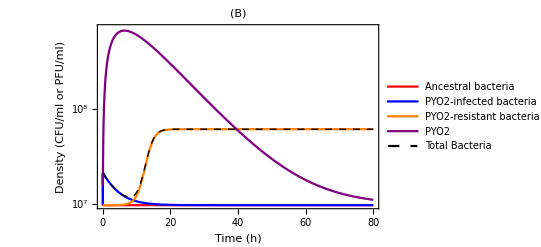

```mathematica
PH2[k_,a_]={0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B+a*Br,-0.25*Bi+460*B*P,0.005*B+0.8*Br*(1-(B+Br)/k)-a*Br,-0.09*P+100*0.25*Bi-460*B*P,0.8772547720626924*B*(1-(B+Br)/k)-460*B*P-0.005*B-0.25*Bi+460*B*P+0.005*B+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
parameterValues={k->0.9,a->0};
sol=NDSolveValue[{{X'[t]==(PH2[k,a]/.Thread[stateVar->X[t]])}/.parameterValues,X[0]=={0.2,0,0,0.2,0.2}},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,80}];
Plot[Evaluate[sol],{t,0,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},PlotLegends->Placed[LineLegend[{"Ancestral bacteria","PYO2-infected bacteria","PYO2-resistant bacteria","PYO2","Total Bacteria"}],{0.74,0.73}],PlotTheme->"Detailed",FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotStyle->{{Red},{Blue},{Orange},{Purple},{Black,Dashed,Thick}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

```mathematica
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
PHdelayearly[rn_,a_,k_,b_,h_,p_,rc_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,b*B*P-Bi*0.05,a*B+rc*Br*(1-(B+Br)/k),-p*P-b*B*P,rn*B*(1-(B+Br)/k)-b*B*P-a*B+b*B*P-Bi*0.05+a*B+rc*Br*(1-(B+Br)/k)}/.Thread[stateVar->X[t]];
X'[t]==PHdelay[rn,a,k,b,h,p,rc]
PHdelay[rn_,a_,k_,b_,h_,p_,rc_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,-delay+b*B*P-Bi*0,a*B+rc*Br*(1-(B+Br)/k),-p*P+h*delay-b*B*P,rn*B*(1-(B+Br)/k)-b*B*P-a*B-delay+b*B*P-Bi*0+a*B+rc*Br*(1-(B+Br)/k)}/.Thread[stateVar->X[t]]/.{delay->b*B[t-τ]*P[t-τ]};
X'[t]==PHdelay[rn,a,k,b,h,p,rc]
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=-1]=={0,0,0,0,0},WhenEvent[t==0,{B[t]->B0,P[t]->B0*MOI,Bt[t]->B0}]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,-1,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}==PHdelay[rn,a,k,b,h,p,rc]

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}=={-a B[t]+rn B[t] (1-(B[t]+Br[t])/k)-b B[t] P[t],b B[t] P[t]-b B[t-τ] P[t-τ],a B[t]+rc Br[t] (1-(B[t]+Br[t])/k),-p P[t]-b B[t] P[t]+b h B[t-τ] P[t-τ],rn B[t] (1-(B[t]+Br[t])/k)+rc Br[t] (1-(B[t]+Br[t])/k)-b B[t-τ] P[t-τ]}

ParametricFunction[<>]

ParametricFunction[<>]

```mathematica
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=-1]=={0,0,0,0,0},WhenEvent[t==0,{B[t]->B0,P[t]->B0*MOI,Bt[t]->B0}]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,-1,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

ParametricFunction[<>]

```mathematica
soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
X'[t]==PHdelayearly[rn,a,k,b,h,p,rc]
```

{B'[t],Bi'[t],Br'[t],P'[t],Bt'[t]}=={-a B[t]+rn B[t] (1-(B[t]+Br[t])/k)-b B[t] P[t],b B[t] P[t],a B[t]+rc Br[t] (1-(B[t]+Br[t])/k),-p P[t]-b B[t] P[t],rn B[t] (1-(B[t]+Br[t])/k)+rc Br[t] (1-(B[t]+Br[t])/k)}

```mathematica
soldelay=ParametricNDSolveValue[{X'[t]==PHdelay[rn,a,k,b,h,p,rc],X[t/;t<=0]=={0,0,0,0,0},WhenEvent[t==0,B[t]->B0;Bt[t]->B0;P[t]->B0*MOI]},Apply[CFU[#]&,{{B[t]},{Bi[t]},{Br[t]},{P[t]},{Bt[t]}},{1}],{t,0,100},{rn,a,k,b,h,τ,p,rc,B0,MOI}]
```

```mathematica
26/60//N
```

0.433333

```mathematica
1/0.25
```

4.

```mathematica
Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]]/.t->0.5
```

{9.78547×10^6,1.17841×10^7,9.78921×10^6,9.93024×10^8,1.17879×10^7}

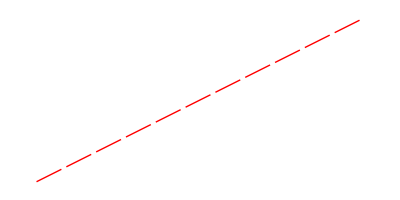

Dashing[{0.05,0.01}]

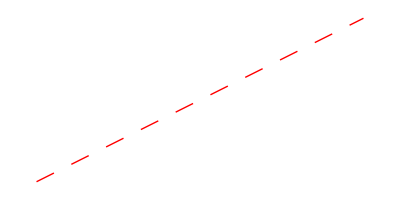

Dashing[Large]

-Graphics-

{Dashing[{0.002,0.003}],Thickness[Large]}

-Graphics-

Dashing[None]

-Graphics-

Dashing[{0,Small,Small,Small}]

-Graphics-

Dashing[None]

```mathematica
(* Total *)
Graphics[{Dashing[{0.05,0.01}],Red,Line[{{0,0},{2,1}}]}]
totLine=Dashing[{0.05,0.01}]
(* Ancestral *)
Graphics[{Dashing[Large],Red,Line[{{0,0},{2,1}}]}]
ansLine=Dashing[Large]
(* Infected *)
Graphics[{Dashing[{0.002,0.003}],Thick,Red,Line[{{0,0},{2,1}}]}]
infLine={Dashing[{0.002,0.003}],Thick}
(* Single mutant *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
smLine=Dashing[None]
(* Double mutant *)
Graphics[{DotDashed,Red,Line[{{0,0},{2,1}}]}]
dmLine=DotDashed
(* Phage *)
Graphics[{Dashing[None],Red,Line[{{0,0},{2,1}}]}]
pline=Dashing[None]
```

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.017,0.9,460,100,26/60,0.09,0.77,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},Frame->True,FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","LUZ19-infected\nBacteria","LUZ19-resistant\nSingle Mutant","LUZ19","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["lightgreen"],infLine,AbsoluteThickness[5]},{RGBColor["mediumseagreen"],smLine,AbsoluteThickness[5]},{RGBColor["darkgreen"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(A)"]
```

-Graphics-

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,100,26/60,0.09,0.8,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","PYO2-infected\nBacteria","PYO2-resistant\nSingle Mutant","PYO2","Total Bacteria"}],{0.76,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["powderblue"],infLine,AbsoluteThickness[5]},{RGBColor["mediumslateblue"],smLine,AbsoluteThickness[5]},{RGBColor["navy"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(B)"]
```

-Graphics-

```mathematica
Plot[Evaluate[soldelay[0.8772547720626924,0.005,0.9,460,200,30.000000001/60,0.09,0.81,0.2,1]],{t,-1,80},PlotRange->{{0,80},{0,7*10^8}},GridLines->Automatic,BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Time (h)","Density (CFU/ml or PFU/ml)"},Frame->True,PlotLegends->Placed[LineLegend[{"Ancestral Bacteria","E215-infected\nBacteria","E215-resistant\nSingle Mutant","E215","Total Bacteria"}],{0.79,0.6}],PlotStyle->{{Black,ansLine,AbsoluteThickness[5]},{RGBColor["thistle"],infLine,AbsoluteThickness[5]},{RGBColor["magenta"],smLine,AbsoluteThickness[5]},{RGBColor["darkmagenta"],pline,AbsoluteThickness[5]},{Red,totLine,AbsoluteThickness[5]}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->Full,ScalingFunctions->"Log10",PlotLabel->"(C)"]
```

-Graphics-

```mathematica
{{-Graphics-, -Graphics-, -Graphics-}}
```

```mathematica
Minimize[a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t),t]
```

Minimize[(a B0 ⅇ^(rr t))/(a+b P0)+(b B0 ⅇ^(-s t) P0)/(a+b P0),t]

```mathematica
Plot[Evaluate[a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t)/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}],{t,0,20},PlotRange->{{6,10},{0,0.1}},Epilog->{Line[{{0,0.033415402351083756},{20,0.033415402351083756}}]}]
```

-Graphics-

```mathematica
f[t_]:=a/(b*P0+a)*B0*E^(rr*t)+(b*P0)/(b*P0+a)*B0*E^(-s*t)
```

```mathematica
(f[t]/.Solve[f'[t]==0,t])/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.0334154}

```mathematica
Solve[f'[t]==0,t]/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.8,s->0.25}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→8.24472}}

```mathematica
Solve[f'[t]==0,t]/.{a->0.027,b->460,P0->0.2,B0->0.2,rr->0.77,s->0.19}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→7.01494}}

```mathematica
Solve[f'[t]==0,t]/.{a->0.005,b->460,P0->0.2,B0->0.2,rr->0.81,s->0.02}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→7.37205}}

```mathematica
FullSimplify[f[t]/.Solve[f'[t]==0,t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(a B0 ((a rr)/(b P0 s))^(-rr/(rr+s)) (rr+s))/((a+b P0) s)}

```mathematica
Solve[f'[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-Log[(a rr)/(b P0 s)]/(rr+s)}}

```mathematica
f'[t]
```

(a B0 ⅇ^(rr t) rr)/(a+b P0)-(b B0 ⅇ^(-s t) P0 s)/(a+b P0)

```mathematica
PH2[a_,k_,b_,h_,s_,p_,ra_]={rn*B*(1-(B+Br)/k)-b*B*P-a*B,-s*Bi+b*B*P,a*B+ra*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)};
```

```mathematica
FullSimplify[rn*B*(1-(B+Br)/k)-b*B*P-a*B-s*Bi+b*B*P+a*B+ra*Br*(1-(B+Br)/k)==0]
```

((B+Br-k) (Br ra+B rn))/k+Bi s==0

## Lowest bacteria concentration

```mathematica
FullSimplify[0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B+a*Br-s*Bi+b*B*P+0.005*B+0.8*Br*(1-(B+Br)/k)-a*Br]
```

0.-(0.877255 B (B+Br-1. k))/k-(0.8 Br (B+Br-1. k))/k-Bi s

### s and h

```mathematica
CFU[x_]:=57115528.37x+9785470.84
```

```mathematica
Module[{i,j,l,parameterValues,sol},
PH2[k_,b_,s_,h_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B,-s*Bi+b*B*P,0.005*B+0.8*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-s*Bi+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
result=Table[Table[NA,10],10];
For[i=0,i<10,i=i+1,
For[j=0,j<10,j=j+1,
parameterValues={k->0.9,b->460,s->0.001+0.05*j,h->40+i*30,p->0.09};
sol=NDSolveValue[{{X'[t]==(PH2[k,b,s,h,p]/.Thread[stateVar->X[t]])/.parameterValues},X[0]=={0.2,0,0,0.2,0.2}},CFU[Bt[t]],{t,0,50}];
totMin=FindMinimum[{sol,0<=t<=30},{t,10}];
result[[i+1,j+1]]=totMin[[1]]
]
];
result
]
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},10],10];
finalResult={};
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,
heatResult[[i,j,1]]=10+(i-1)*30;
heatResult[[i,j,2]]=0.001+0.005*(j-1)*10;
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤10,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
g1=Show[ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Burst size (h)","Lysis rate (s)"},ImageSize->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Minimal total bacterial density (CFU/ml)",LabelStyle->{Italic,Bold,Black,FontFamily->"Helvetica"}],Above],ColorFunction->"TemperatureMap",FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},PlotRange->All,Epilog->{Text["LUZ19",{86,0.19}],Text["PYO2",{88,0.25}],Text["E215",{189,0.02}]},PlotLabel->"(A)"],Graphics[{PointSize[0.01],Point[{{100,0.19},{100,0.25},{200,0.02}}]}]]
```

{{2.12086×10^7,1.83612×10^7,1.57713×10^7,1.40022×10^7,1.28093×10^7,1.19974×10^7,1.14355×10^7,1.10397×10^7,1.07555×10^7,1.05479×10^7},{2.12086×10^7,1.82871×10^7,1.56858×10^7,1.39191×10^7,1.27344×10^7,1.19321×10^7,1.13797×10^7,1.09921×10^7,1.0715×10^7,1.05134×10^7},{2.17419×10^7,1.82403×10^7,1.56307×10^7,1.38656×10^7,1.26862×10^7,1.18902×10^7,1.13438×10^7,1.09616×10^7,1.06892×10^7,1.04914×10^7},{2.1689×10^7,1.82059×10^7,1.559×10^7,1.38259×10^7,1.26505×10^7,1.18592×10^7,1.13174×10^7,1.09392×10^7,1.06702×10^7,1.04753×10^7},{2.16557×10^7,1.81786×10^7,1.55576×10^7,1.37942×10^7,1.2622×10^7,1.18346×10^7,1.12964×10^7,1.09214×10^7,1.06551×10^7,1.04625×10^7},{2.16321×10^7,1.81559×10^7,1.55306×10^7,1.37678×10^7,1.25983×10^7,1.18141×10^7,1.12789×10^7,1.09067×10^7,1.06427×10^7,1.0452×10^7},{2.16141×10^7,1.81366×10^7,1.55074×10^7,1.37452×10^7,1.2578×10^7,1.17966×10^7,1.1264×10^7,1.08941×10^7,1.06321×10^7,1.04431×10^7},{2.15997×10^7,1.81197×10^7,1.54871×10^7,1.37255×10^7,1.25603×10^7,1.17812×10^7,1.12511×10^7,1.08832×10^7,1.06229×10^7,1.04353×10^7},{2.15878×10^7,1.81046×10^7,1.54691×10^7,1.37078×10^7,1.25446×10^7,1.17676×10^7,1.12395×10^7,1.08735×10^7,1.06147×10^7,1.04284×10^7},{2.15777×10^7,1.80911×10^7,1.54527×10^7,1.3692×10^7,1.25304×10^7,1.17554×10^7,1.12292×10^7,1.08647×10^7,1.06074×10^7,1.04222×10^7}}

{{10,0.001,2.12086×10^7},{10,0.051,1.83612×10^7},{10,0.101,1.57713×10^7},{10,0.151,1.40022×10^7},{10,0.201,1.28093×10^7},{10,0.251,1.19974×10^7},{10,0.301,1.14355×10^7},{10,0.351,1.10397×10^7},{10,0.401,1.07555×10^7},{10,0.451,1.05479×10^7},{40,0.001,2.12086×10^7},{40,0.051,1.82871×10^7},{40,0.101,1.56858×10^7},{40,0.151,1.39191×10^7},{40,0.201,1.27344×10^7},{40,0.251,1.19321×10^7},{40,0.301,1.13797×10^7},{40,0.351,1.09921×10^7},{40,0.401,1.0715×10^7},{40,0.451,1.05134×10^7},{70,0.001,2.17419×10^7},{70,0.051,1.82403×10^7},{70,0.101,1.56307×10^7},{70,0.151,1.38656×10^7},{70,0.201,1.26862×10^7},{70,0.251,1.18902×10^7},{70,0.301,1.13438×10^7},{70,0.351,1.09616×10^7},{70,0.401,1.06892×10^7},{70,0.451,1.04914×10^7},{100,0.001,2.1689×10^7},{100,0.051,1.82059×10^7},{100,0.101,1.559×10^7},{100,0.151,1.38259×10^7},{100,0.201,1.26505×10^7},{100,0.251,1.18592×10^7},{100,0.301,1.13174×10^7},{100,0.351,1.09392×10^7},{100,0.401,1.06702×10^7},{100,0.451,1.04753×10^7},{130,0.001,2.16557×10^7},{130,0.051,1.81786×10^7},{130,0.101,1.55576×10^7},{130,0.151,1.37942×10^7},{130,0.201,1.2622×10^7},{130,0.251,1.18346×10^7},{130,0.301,1.12964×10^7},{130,0.351,1.09214×10^7},{130,0.401,1.06551×10^7},{130,0.451,1.04625×10^7},{160,0.001,2.16321×10^7},{160,0.051,1.81559×10^7},{160,0.101,1.55306×10^7},{160,0.151,1.37678×10^7},{160,0.201,1.25983×10^7},{160,0.251,1.18141×10^7},{160,0.301,1.12789×10^7},{160,0.351,1.09067×10^7},{160,0.401,1.06427×10^7},{160,0.451,1.0452×10^7},{190,0.001,2.16141×10^7},{190,0.051,1.81366×10^7},{190,0.101,1.55074×10^7},{190,0.151,1.37452×10^7},{190,0.201,1.2578×10^7},{190,0.251,1.17966×10^7},{190,0.301,1.1264×10^7},{190,0.351,1.08941×10^7},{190,0.401,1.06321×10^7},{190,0.451,1.04431×10^7},{220,0.001,2.15997×10^7},{220,0.051,1.81197×10^7},{220,0.101,1.54871×10^7},{220,0.151,1.37255×10^7},{220,0.201,1.25603×10^7},{220,0.251,1.17812×10^7},{220,0.301,1.12511×10^7},{220,0.351,1.08832×10^7},{220,0.401,1.06229×10^7},{220,0.451,1.04353×10^7},{250,0.001,2.15878×10^7},{250,0.051,1.81046×10^7},{250,0.101,1.54691×10^7},{250,0.151,1.37078×10^7},{250,0.201,1.25446×10^7},{250,0.251,1.17676×10^7},{250,0.301,1.12395×10^7},{250,0.351,1.08735×10^7},{250,0.401,1.06147×10^7},{250,0.451,1.04284×10^7},{280,0.001,2.15777×10^7},{280,0.051,1.80911×10^7},{280,0.101,1.54527×10^7},{280,0.151,1.3692×10^7},{280,0.201,1.25304×10^7},{280,0.251,1.17554×10^7},{280,0.301,1.12292×10^7},{280,0.351,1.08647×10^7},{280,0.401,1.06074×10^7},{280,0.451,1.04222×10^7}}

-Graphics-

```mathematica
minDense[0.005,0.8,0.01,460,0.2,0.2]
```

2.05998×10^7

```mathematica
minDense[a_,rr_,s_,b_,B0_,P0_]:=CFU[(a B0 ((a rr)/(b P0 s))^(-rr/(rr+s)) (rr+s))/((a+b P0) s)]
Module[{i,j,l,parameterValues,sol},
PH2[k_,b_,s_,h_,p_]={0.8772547720626924*B*(1-(B+Br)/k)-b*B*P-0.005*B,-s*Bi+b*B*P,0.005*B+0.8*Br*(1-(B+Br)/k),-p*P+h*s*Bi-b*B*P,0.8772547720626924*B*(1-(B+Br)/k)-s*Bi+0.8*Br*(1-(B+Br)/k)};
stateVar={B,Bi,Br,P,Bt};
X[t_]=Through[stateVar[t]];
result=Table[Table[NA,10],10];
For[i=0,i<10,i=i+1,
For[j=0,j<10,j=j+1,
parameterValues={k->0.9,b->460,s->0.001+0.05*j,h->40+i*30,p->0.09,rr->0.8,a->0.005};
totMin=minDense[a,rr,0.001+0.05*j,b,0.2,0.2]/.parameterValues;
result[[i+1,j+1]]=totMin
]
];
result
]
Module[{i,j,k},
heatResult=Table[Table[{NA,NA,NA},10],10];
finalResult={};
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,
heatResult[[i,j,1]]=10+(i-1)*30;
heatResult[[i,j,2]]=0.001+0.005*(j-1)*10;
heatResult[[i,j,3]]=result[[i,j]];
]
];
For[k=1,k≤10,k++,
finalResult=Join[finalResult,heatResult[[k]]]
];
finalResult
]
g2=Show[ListDensityPlot[finalResult,Mesh->All,PlotTheme->"Detailed",BaseStyle->{Bold,25},FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},LabelStyle->{Bold,Black},FrameLabel->{"Burst size (h)","Lysis rate (s)"},ImageSize->Full,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Minimal total bacterial density (CFU/ml)",LabelStyle->{Italic,Bold,Black,FontFamily->"Helvetica"}],Above],ColorFunction->"TemperatureMap",FrameStyle->{{{Black,Bold},{Black,Bold}},{{Black,Bold},{Black,Bold}}},FrameTicks->{{Table[0.001+0.005*j,{j,0,90,10}],None},{Table[40+i*30,{i,-1,9,1}],None}},PlotRange->All,Epilog->{Text["LUZ19",{86,0.19}],Text["PYO2",{88,0.25}],Text["E215",{189,0.02}]},PlotLabel->"(B)"],Graphics[{PointSize[0.01],Point[{{100,0.19},{100,0.25},{200,0.02}}]}]]
```

{{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7},{2.11776×10^7,1.77408×10^7,1.51814×10^7,1.35064×10^7,1.24108×10^7,1.16821×10^7,1.11869×10^7,1.0843×10^7,1.0599×10^7,1.04225×10^7}}

{{10,0.001,2.11776×10^7},{10,0.051,1.77408×10^7},{10,0.101,1.51814×10^7},{10,0.151,1.35064×10^7},{10,0.201,1.24108×10^7},{10,0.251,1.16821×10^7},{10,0.301,1.11869×10^7},{10,0.351,1.0843×10^7},{10,0.401,1.0599×10^7},{10,0.451,1.04225×10^7},{40,0.001,2.11776×10^7},{40,0.051,1.77408×10^7},{40,0.101,1.51814×10^7},{40,0.151,1.35064×10^7},{40,0.201,1.24108×10^7},{40,0.251,1.16821×10^7},{40,0.301,1.11869×10^7},{40,0.351,1.0843×10^7},{40,0.401,1.0599×10^7},{40,0.451,1.04225×10^7},{70,0.001,2.11776×10^7},{70,0.051,1.77408×10^7},{70,0.101,1.51814×10^7},{70,0.151,1.35064×10^7},{70,0.201,1.24108×10^7},{70,0.251,1.16821×10^7},{70,0.301,1.11869×10^7},{70,0.351,1.0843×10^7},{70,0.401,1.0599×10^7},{70,0.451,1.04225×10^7},{100,0.001,2.11776×10^7},{100,0.051,1.77408×10^7},{100,0.101,1.51814×10^7},{100,0.151,1.35064×10^7},{100,0.201,1.24108×10^7},{100,0.251,1.16821×10^7},{100,0.301,1.11869×10^7},{100,0.351,1.0843×10^7},{100,0.401,1.0599×10^7},{100,0.451,1.04225×10^7},{130,0.001,2.11776×10^7},{130,0.051,1.77408×10^7},{130,0.101,1.51814×10^7},{130,0.151,1.35064×10^7},{130,0.201,1.24108×10^7},{130,0.251,1.16821×10^7},{130,0.301,1.11869×10^7},{130,0.351,1.0843×10^7},{130,0.401,1.0599×10^7},{130,0.451,1.04225×10^7},{160,0.001,2.11776×10^7},{160,0.051,1.77408×10^7},{160,0.101,1.51814×10^7},{160,0.151,1.35064×10^7},{160,0.201,1.24108×10^7},{160,0.251,1.16821×10^7},{160,0.301,1.11869×10^7},{160,0.351,1.0843×10^7},{160,0.401,1.0599×10^7},{160,0.451,1.04225×10^7},{190,0.001,2.11776×10^7},{190,0.051,1.77408×10^7},{190,0.101,1.51814×10^7},{190,0.151,1.35064×10^7},{190,0.201,1.24108×10^7},{190,0.251,1.16821×10^7},{190,0.301,1.11869×10^7},{190,0.351,1.0843×10^7},{190,0.401,1.0599×10^7},{190,0.451,1.04225×10^7},{220,0.001,2.11776×10^7},{220,0.051,1.77408×10^7},{220,0.101,1.51814×10^7},{220,0.151,1.35064×10^7},{220,0.201,1.24108×10^7},{220,0.251,1.16821×10^7},{220,0.301,1.11869×10^7},{220,0.351,1.0843×10^7},{220,0.401,1.0599×10^7},{220,0.451,1.04225×10^7},{250,0.001,2.11776×10^7},{250,0.051,1.77408×10^7},{250,0.101,1.51814×10^7},{250,0.151,1.35064×10^7},{250,0.201,1.24108×10^7},{250,0.251,1.16821×10^7},{250,0.301,1.11869×10^7},{250,0.351,1.0843×10^7},{250,0.401,1.0599×10^7},{250,0.451,1.04225×10^7},{280,0.001,2.11776×10^7},{280,0.051,1.77408×10^7},{280,0.101,1.51814×10^7},{280,0.151,1.35064×10^7},{280,0.201,1.24108×10^7},{280,0.251,1.16821×10^7},{280,0.301,1.11869×10^7},{280,0.351,1.0843×10^7},{280,0.401,1.0599×10^7},{280,0.451,1.04225×10^7}}

-Graphics-

```mathematica
colorbar[cf_]:=DensityPlot[x,{x,0,370},{y,0,50},ColorFunction->cf,ColorFunctionScaling->True,AspectRatio->Automatic,PlotRangePadding->10,FrameTicks->{{None,None},{Transpose[{Subdivide[370,5],N@Subdivide[5]}],None}}]
cf=ColorData["TemperatureMap",Rescale[#,{0,1},{0.25,1}]]&;
colorbar[cf]
```

-Graphics-

```mathematica
g2[[2,1]]
```

```mathematica
GraphicsGrid[{{g1,g2}},ImageSize->2000]
```

-Graphics-

### Countour s, a, b,rr

```mathematica
minDense[a_,rr_,s_,b_,B0_,P0_]
```

```mathematica
ContourPlot[minDense[a,0.8,s,460,0.2,0.2],{a,0,0.5},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-

```mathematica
ContourPlot[minDense[0.005,0.8,s,b,0.2,0.2],{b,0,1000},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-

```mathematica
ContourPlot[minDense[0.005,rr,s,460,0.2,0.2],{rr,0,1},{s,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-

```mathematica
ContourPlot[minDense[a,0.8,0.252,b,0.2,0.2],{a,0,0.5},{b,0,1000},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-

```mathematica
ContourPlot[minDense[a,rr,0.252,460,0.2,0.2],{a,0,0.5},{rr,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-

```mathematica
ContourPlot[minDense[0.005,rr,0.252,b,0.2,0.2],{b,0,1000},{rr,0,1},PlotLegends->Automatic,FrameLabel->Automatic]
```

-Graphics-